### Goal

The goal of the project is to enable the user to visualize the Fourier Series for a function and in 2D with nth degree accuracy. There will be two parts to the project concerning the inputs given. The first will allow the user to input a function and create a visualization of a Fourier series that creates a graph approximately close to the given function. The second option is to input an image and get back a visualization of the process and generating a pair of Fourier Series that generates the given curve in a 2D plane. For the image, I will use image processing in order to pull out a curve and then use it to give them back a result. With both inputs, the user will be able to specify the accuracy of the resulting Fourier Series.

### Steps

#### Fort the Image

Step 1: Input form: Image 
	I will need to use image processing in order to separate a curve form the image
	Method?:
		Binarize, edge detect
Step 2: Extract the x-values and create a graph/function
	Step 2a : convert the graph’s values to a function (maybe a piecewise function)
Step 3 :Create a Fourier Series/Transform for the resulting function
Step 4 : Repeat for the y-values
Step 5 :Place the two resulting circles at the corresponding place and create infinite line (vertical, and horizontal) lines for the x-values and y-values respectably
Step 6 :  Where the two infinite lines intersect, I want a point to be plotted

#### For the function

Step 1: use the built in function to input the given function
	Inputs include: number of circles, the function of the graph/curve,
Step 2 : take the results and plug it into my graphics function

#### For the Graph/Visualization

Step 1 : create a function that takes in inputs and generates the rotating circles
Step 2 : create a extension line form the end of the last circle to an arbitrary point (horizontal line) that traces out a graph
Step 3 : Connect it with the previous functions

```mathematica
?FourierTransform
```

WolframAlphaQueryParseResults//FullForm

Graphics[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[-372.04,811.481],List[-378.431,809.435],List[-384.672,808.352],List[-390.437,808.134],List[-395.406,808.615],List[-399.289,809.584],List[-401.86,810.81],List[-402.976,812.068],List[-402.593,813.165],List[-400.768,813.961],List[-397.654,814.385],List[-393.481,814.445],List[-388.538,814.224],List[-383.137,813.872],List[-377.59,813.59],List[-372.175,813.601],List[-367.111,814.126],List[-362.549,815.354],List[-358.554,817.416],List[-355.112,820.362],List[-352.141,824.15],List[-349.502,828.647],List[-347.025,833.63],List[-344.53,838.811],List[-341.846,843.857],List[-338.837,848.431],List[-335.406,852.221],List[-331.508,854.973],List[-327.145,856.527],List[-322.363,856.827],List[-317.242,855.936],List[-311.88,854.032],List[-306.38,851.39],List[-300.841,848.354],List[-295.346,845.305],List[-289.957,842.622],List[-284.714,840.639],List[-279.641,839.613],List[-274.747,839.698],List[-270.035,840.927],List[-265.51,843.21],List[-261.181,846.348],List[-257.065,850.055],List[-253.187,853.99],List[-249.573,857.796],List[-246.245,861.138],List[-243.212,863.744],List[-240.465,865.428],List[-237.966,866.116],List[-235.648,865.843],List[-233.417,864.754],List[-231.155,863.079],List[-228.726,861.11],List[-225.997,859.161],List[-222.842,857.539],List[-219.161,856.505],List[-214.887,856.249],List[-209.999,856.876],List[-204.52,858.395],List[-198.516,860.724],List[-192.086,863.709],List[-185.355,867.142],List[-178.454,870.789],List[-171.51,874.418],List[-164.627,877.824],List[-157.323,881.078],List[-150.227,883.749],List[-143.341,885.784],List[-136.624,887.198],List[-130.013,888.052],List[-123.438,888.429],List[-116.846,888.405],List[-110.218,888.028],List[-103.574,887.307],List[-96.9802,886.214],List[-90.5354,884.69],List[-84.3567,882.672],List[-78.556,880.116],List[-73.2154,877.024],List[-68.3648,873.466],List[-63.9668,869.588],List[-59.9107,865.611],List[-56.0193,861.814],List[-52.0671,858.5],List[-47.8081,855.96],List[-43.0097,854.427],List[-37.4879,854.038],List[-31.1372,854.807],List[-23.952,856.608],List[-16.0336,859.186],List[-7.58262,862.176],List[1.12417,865.152],List[9.76903,867.677],List[18.0362,869.363],List[25.6567,869.923],List[32.4477,869.216],List[38.3417,867.268],List[43.3991,864.272],List[47.8035,860.567],List[51.8387,856.59],List[55.8497,852.818],List[60.1943,849.699],List[65.1908,847.59],List[71.0695,846.7],List[77.9355,847.06],List[85.7475,848.509],List[94.3166,850.717],List[103.326,853.22],List[112.37,855.485],List[121.003,856.979],List[128.799,857.242],List[135.406,855.947],List[140.597,852.946],List[144.3,848.293],List[146.607,842.233],List[147.768,835.173],List[148.162,827.628],List[148.245,820.155],List[148.497,813.276],List[149.36,807.419],List[151.19,802.863],List[154.207,799.705],List[158.478,797.863],List[163.91,797.086],List[170.27,797.005],List[177.222,797.185],List[184.371,797.192],List[191.321,796.654],List[197.73,795.311],List[203.006,793.232],List[207.498,790.388],List[211.213,786.928],List[214.269,783.094],List[216.868,779.185],List[219.282,775.521],List[221.81,772.402],List[224.745,770.067],List[228.341,768.668],List[232.777,768.246],List[238.136,768.728],List[244.391,769.934],List[251.404,771.595],List[258.939,773.382],List[266.676,774.939],List[274.25,775.922],List[281.276,776.03],List[287.39,775.034],List[292.284,772.796],List[295.73,769.277],List[297.608,764.534],List[297.911,758.715],List[296.755,752.034],List[294.363,744.751],List[291.053,737.149],List[287.209,729.507],List[283.254,722.084],List[279.615,715.098],List[276.694,708.721],List[274.838,703.078],List[274.311,698.239],List[275.285,694.236],List[277.821,691.063],List[281.875,688.685],List[287.302,687.048],List[293.868,686.082],List[301.274,685.703],List[309.172,685.815],List[317.197,686.312],List[324.986,687.07],List[332.204,687.952],List[338.564,688.806],List[343.838,689.47],List[347.867,689.774],List[350.566,689.554],List[351.92,688.66],List[351.978,686.965],List[350.842,684.383],List[348.655,680.871],List[345.588,676.445],List[337.567,665.192],List[332.994,658.673],List[328.294,651.839],List[319.201,638.226],List[315.135,631.962],List[311.6,626.38],List[308.748,621.678],List[306.728,618.012],List[305.681,615.48],List[305.731,614.127],List[306.978,613.936],List[309.488,614.838],List[313.189,616.669],List[318.077,619.286],List[330.938,626.138],List[338.509,629.958],List[346.476,633.752],List[354.51,637.309],List[362.259,640.427],List[369.373,642.927],List[375.53,644.657],List[380.459,645.497],List[383.965,645.368],List[385.949,644.236],List[386.413,642.114],List[385.47,639.067],List[383.329,635.206],List[380.286,630.691],List[376.698,625.721],List[372.951,620.521],List[369.431,615.338],List[366.491,610.419],List[364.42,605.997],List[363.417,602.276],List[363.579,599.416],List[364.895,597.515],List[367.244,596.608],List[370.415,596.653],List[374.121,597.536],List[378.034,599.078],List[381.81,601.042],List[385.121,603.152],List[387.685,605.111],List[389.284,606.626],List[389.788,607.427],List[389.153,607.293],List[387.43,606.066],List[384.748,603.667],List[381.309,600.108],List[377.36,595.486],List[373.177,589.984],List[369.043,583.855],List[365.229,577.404],List[361.973,570.967],List[359.473,564.88],List[357.878,559.458],List[357.282,554.965],List[357.727,551.592],List[359.207,549.446],List[361.67,548.532],List[365.027,548.76],List[369.157,549.947],List[373.912,551.833],List[379.122,554.107],List[384.604,556.429],List[390.16,558.463],List[395.591,559.909],List[400.698,560.529],List[405.293,560.17],List[409.208,558.78],List[412.307,556.415],List[414.493,553.234],List[415.72,549.488],List[416.002,545.496],List[415.409,541.616],List[413.932,537.956],List[411.818,535.28],List[409.357,533.926],List[406.867,534.104],List[404.662,535.875],List[403.022,539.14],List[402.157,543.65],List[402.191,549.04],List[403.14,554.864],List[404.912,560.654],List[407.322,565.971],List[410.11,570.458],List[412.978,573.883],List[415.631,576.165],List[417.815,577.378],List[419.353,577.746],List[420.176,577.604],List[420.333,577.358],List[419.988,577.426],List[419.403,578.183],List[418.903,579.908],List[418.833,582.743],List[419.51,586.674],List[421.175,591.526],List[423.949,596.984],List[427.817,602.628],List[432.609,607.992],List[438.013,612.617],List[443.608,616.111],List[448.902,618.206],List[453.388,618.787],List[456.604,617.912],List[458.183,615.809],List[457.901,612.843],List[455.703,609.477],List[451.709,606.21],List[446.209,603.517],List[439.621,601.79],List[432.457,601.287],List[425.255,602.105],List[418.529,604.166],List[412.708,607.232],List[408.098,610.939],List[404.855,614.845],List[402.97,618.49],List[402.29,621.463],List[402.54,623.45],List[403.369,624.286],List[404.398,623.973],List[405.271,622.688],List[405.701,620.761],List[405.505,618.64],List[404.621,616.839],List[403.115,615.873],List[401.166,616.202],List[399.036,618.179],List[397.038,622.003],List[395.489,627.703],List[394.674,635.133],List[394.805,643.989],List[396.005,653.842],List[398.286,664.185],List[401.559,674.483],List[405.641,684.23],List[409.961,692.438],List[414.536,699.508],List[419.124,705.257],List[423.499,709.604],List[427.465,712.56],List[430.866,714.216],List[433.598,714.724],List[435.6,714.271],List[436.856,713.058],List[437.378,711.281],List[437.2,709.108],List[436.362,706.676],List[434.901,704.079],List[432.842,701.377],List[430.197,698.6],List[426.963,695.758],List[423.131,692.856],List[418.686,689.908],List[413.628,686.94],List[407.97,684.007],List[401.757,681.188],List[395.064,678.585],List[388.003,676.318],List[380.719,674.517],List[373.386,673.304],List[366.197,672.786],List[359.354,673.039],List[353.057,674.103],List[347.489,675.974],List[342.809,678.598],List[339.141,681.88],List[336.572,685.683],List[335.15,689.841],List[334.88,694.164],List[335.73,698.459],List[337.637,702.531],List[340.506,706.205],List[344.217,709.327],List[348.629,711.776],List[353.578,713.472],List[358.887,714.374],List[364.359,714.485],List[369.785,713.851],List[374.948,712.562],List[379.627,710.741],List[383.607,708.546],List[386.691,706.162],List[388.713,703.792],List[389.549,701.65],List[389.136,699.948],List[387.482,698.888],List[384.671,698.649],List[380.866,699.373],List[376.306,701.156],List[371.294,704.039],List[366.176,707.997],List[361.32,712.939],List[357.086,718.706],List[353.796,725.081],List[351.707,731.794],List[350.988,738.54],List[351.701,744.997],List[353.792,750.849],List[357.101,755.808],List[361.753,759.895],List[367.091,762.438],List[372.62,763.338],List[377.833,762.623],List[382.267,760.447],List[385.545,757.082],List[387.42,752.894],List[387.789,748.313],List[386.704,743.797],List[384.357,739.795],List[381.055,736.706],List[377.182,734.853],List[373.157,734.457],List[369.385,735.626],List[366.223,738.351],List[363.95,742.518],List[362.75,747.925],List[362.706,754.305],List[363.814,761.357],List[365.996,768.77],List[369.124,776.248],List[373.049,783.528],List[377.614,790.395],List[382.673,796.679],List[388.095,802.258],List[393.76,807.047],List[399.549,810.99],List[405.328,814.046],List[410.937,816.184],List[416.177,817.38],List[420.808,817.614],List[424.559,816.878],List[427.144,815.187],List[428.291,812.59],List[427.773,809.179],List[425.448,805.103],List[421.285,800.561],List[415.389,795.804],List[408.007,791.117],List[399.517,786.798],List[390.408,783.134],List[381.234,780.368],List[372.563,778.669],List[364.918,778.114],List[358.726,778.669],List[354.266,780.185],List[351.638,782.409],List[350.754,785.01],List[351.345,787.605],List[352.991,789.808],List[355.174,791.268],List[357.334,791.717],List[358.933,790.998],List[359.523,789.09],List[358.791,786.112],List[356.597,782.314],List[352.985,778.046],List[348.173,773.717],List[342.525,769.746],List[336.5,766.505],List[330.599,764.275],List[325.297,763.199],List[320.993,763.267],List[317.956,764.306],List[316.322,765.963],List[315.977,767.847],List[316.731,769.5],List[318.277,770.463],List[320.225,770.335],List[322.157,768.827],List[323.666,765.798],List[324.412,761.287],List[324.151,755.515],List[322.765,748.87],List[320.268,741.871],List[316.806,735.123],List[312.632,729.248],List[308.079,724.829],List[303.522,722.343],List[299.338,722.119],List[295.869,724.298],List[293.386,728.828],List[292.069,735.464],List[291.995,743.804],List[293.133,753.326],List[295.355,763.449],List[298.458,773.585],List[302.183,783.199],List[306.245,791.854],List[310.36,799.238],List[314.267,805.183],List[317.747,809.659],List[320.631,812.75],List[322.809,814.63],List[324.216,815.513],List[324.833,815.621],List[324.665,815.144],List[323.728,814.217],List[322.038,812.907],List[319.594,811.213],List[316.382,809.089],List[312.367,806.463],List[301.759,799.502],List[295.105,795.197],List[287.562,790.495],List[279.205,785.621],List[270.174,780.874],List[260.687,776.603],List[251.033,773.171],List[241.561,770.906],List[232.663,770.061],List[224.739,770.777],List[218.17,773.057],List[213.278,776.756],List[210.295,781.591],List[209.336,787.17],List[210.381,793.03],List[213.274,798.693],List[217.73,803.721],List[223.358,807.763],List[229.698,810.599],List[236.261,812.161],List[242.574,812.54],List[248.229,811.965],List[252.914,810.773],List[256.442,809.357],List[258.761,808.111],List[259.903,807.405],List[260.216,807.345],List[259.913,808.029],List[259.244,809.45],List[258.459,811.489],List[257.783,813.944],List[257.388,816.549],List[257.376,819.015],List[257.772,821.071],List[258.522,822.5],List[259.508,823.17],List[260.566,823.059],List[261.514,822.26],List[262.177,820.973],List[262.413,819.485],List[262.139,818.135],List[261.34,817.276],List[260.077,817.224],List[258.481,818.226],List[256.735,820.417],List[255.053,823.807],List[253.652,828.265],List[252.725,833.539],List[252.409,839.274],List[252.774,845.051],List[253.8,850.439],List[255.388,855.037],List[257.36,858.527],List[259.486,860.709],List[261.505,861.529],List[263.16,861.084],List[264.227,859.621],List[264.544,857.504],List[264.032,855.183],List[262.701,853.142],List[260.658,851.848],List[258.091,851.703],List[255.248,853.001],List[252.416,855.898],List[249.884,860.4],List[247.918,866.366],List[246.733,873.526],List[246.476,881.511],List[247.215,889.899],List[248.94,898.259],List[251.572,906.191],List[254.979,913.367],List[258.998,919.554],List[263.457,924.627],List[268.193,928.566],List[273.068,931.441],List[277.974,933.388],List[282.836,934.57],List[287.6,935.153],List[292.221,935.27],List[296.646,935.],List[300.798,934.357],List[304.56,933.295],List[307.776,931.715],List[310.246,929.495],List[311.745,926.516],List[312.041,922.697],List[310.925,918.021],List[308.239,912.556],List[303.471,905.933],List[296.821,898.908],List[288.51,891.913],List[278.925,885.429],List[268.602,879.934],List[258.176,875.834],List[248.323,873.404],List[239.679,872.747],List[232.776,873.772],List[227.967,876.19],List[225.386,879.554],List[224.929,883.305],List[226.257,886.845],List[228.845,889.61],List[232.036,891.146],List[235.13,891.162],List[237.468,889.573],List[238.511,886.497],List[237.911,882.244],List[235.547,877.264],List[231.532,872.08],List[226.197,867.215],List[220.033,863.114],List[213.623,860.085],List[207.556,858.254],List[202.35,857.55],List[198.378,857.718],List[195.823,858.362],List[194.657,859.001],List[194.652,859.14],List[195.421,858.349],List[196.476,856.318],List[197.3,852.91],List[197.421,848.181],List[196.483,842.37],List[194.283,835.875],List[190.803,829.2],List[186.201,822.893],List[180.781,817.483],List[174.952,813.414],List[169.159,811.007],List[163.826,810.43],List[159.3,811.694],List[155.81,814.673],List[153.448,819.133],List[152.171,824.778],List[151.823,831.295],List[152.172,838.394],List[152.96,845.837],List[153.945,853.455],List[155.862,868.849],List[156.689,876.538],List[157.503,884.176],List[158.438,891.69],List[159.65,898.959],List[161.274,905.802],List[163.389,911.985],List[165.989,917.248],List[168.969,921.333],List[172.128,924.022],List[175.188,925.171],List[177.827,924.74],List[179.72,922.803],List[180.559,919.8],List[180.321,915.879],List[178.908,911.316],List[176.304,906.411],List[172.58,901.448],List[167.876,896.669],List[162.387,892.244],List[156.332,888.264],List[149.931,884.728],List[143.378,881.558],List[136.823,878.617],List[130.357,875.737],List[105.389,862.206],List[99.0937,858.228],List[92.6673,854.273],List[86.1102,850.608],List[79.4757,847.54],List[72.8722,845.384],List[66.4576,844.424],List[60.4265,844.879],List[54.9926,846.871],List[50.3681,850.411],List[46.7437,855.39],List[44.2711,861.588],List[43.0503,868.694],List[43.1229,876.331],List[44.4711,884.098],List[47.0226,891.6],List[50.6587,898.483],List[55.2252,904.463],List[60.5429,909.341],List[66.4163,913.011],List[72.6407,915.458],List[79.0055,916.741],List[85.2953,916.982],List[91.2902,916.336],List[96.766,914.977],List[101.497,913.076],List[105.262,910.791],List[107.855,908.261],List[109.1,905.607],List[108.869,902.939],List[107.101,900.365],List[103.819,898.001],List[99.1459,895.977],List[93.3074,894.436],List[86.6288,893.534],List[79.5199,893.43],List[72.4486,894.262],List[65.9056,896.137],List[60.3625,899.103],List[56.2281,903.137],List[53.8074,908.133],List[53.2684,913.899],List[54.621,920.164],List[57.7114,926.6],List[62.2326,932.847],List[67.7522,938.545],List[73.7531,943.372],List[79.6837,947.079],List[85.0128,949.516],List[89.2105,950.639],List[92.0658,950.596],List[93.3915,949.58],List[93.1503,947.877],List[91.4517,945.836],List[88.5334,943.837],List[84.7306,942.256],List[80.434,941.428],List[76.0457,941.62],List[71.9348,943.009],List[68.4005,945.671],List[65.6454,949.585],List[63.7629,954.642],List[62.7387,960.662],List[62.4669,967.424],List[62.7769,974.69],List[63.4675,982.23],List[64.3432,989.845],List[66.09,1004.72],List[66.8585,1011.79],List[67.6232,1018.58],List[68.524,1025.06],List[69.7469,1031.22],List[71.4925,1037.02],List[73.9405,1042.42],List[77.2153,1047.32],List[81.3574,1051.61],List[86.3051,1055.15],List[91.8891,1057.81],List[97.8414,1059.44],List[103.817,1059.97],List[109.427,1059.35],List[114.276,1057.6],List[118.007,1054.84],List[120.336,1051.21],List[121.083,1046.94],List[120.189,1042.27],List[117.725,1037.47],List[113.873,1032.77],List[108.914,1028.37],List[103.186,1024.38],List[97.0512,1020.87],List[90.853,1017.79],List[84.8844,1015.05],List[79.3598,1012.48],List[74.3997,1009.9],List[70.0294,1007.12],List[66.189,1003.99],List[62.7546,1000.42],List[59.5672,996.393],List[56.4646,991.976],List[53.3114,987.33],List[50.0247,982.685],List[46.5892,978.318],List[43.0628,974.523],List[39.5696,971.574],List[36.2828,969.69],List[33.3998,969.007],List[31.1131,969.558],List[29.5807,971.258],List[28.9004,973.912],List[29.0925,977.226],List[30.0909,980.836],List[31.9114,984.613],List[34.2239,987.74],List[36.6855,989.748],List[38.9347,990.265],List[40.6362,989.052],List[41.5209,986.019],List[41.4163,981.225],List[40.2609,974.863],List[38.103,967.234],List[35.084,958.707],List[31.4096,949.683],List[27.3143,940.561],List[23.0254,931.707],List[18.7323,923.441],List[14.566,916.025],List[10.5917,909.664],List[6.81475,904.512],List[3.19863,900.681],List[-0.309652,898.245],List[-3.75164,897.246],List[-7.13284,897.691],List[-10.4064,899.541],List[-13.4686,902.707],List[-16.168,907.031],List[-18.3265,912.287],List[-19.7695,918.176],List[-20.3603,924.339],List[-20.0326,930.377],List[-18.8147,935.883],List[-16.8417,940.482],List[-14.3514,943.87],List[-11.6647,945.853],List[-9.15161,946.378],List[-7.18776,945.548],List[-6.10689,943.618],List[-6.15663,940.979],List[-7.46376,938.119],List[-10.014,935.567],List[-13.6498,933.841],List[-18.0858,933.384],List[-22.9416,934.514],List[-27.7848,937.384],List[-32.1814,941.964],List[-35.7439,948.042],List[-38.173,955.247],List[-39.2863,963.091],List[-39.0316,971.021],List[-37.4836,978.481],List[-34.826,984.966],List[-31.3221,990.07],List[-27.2795,993.522],List[-23.0136,995.201],List[-18.8165,995.132],List[-14.9336,993.467],List[-11.5512,990.454],List[-8.79519,986.397],List[-6.73894,981.612],List[-5.41756,976.395],List[-4.84431,970.99],List[-5.02532,965.576],List[-5.96922,960.256],List[-7.68972,955.07],List[-10.2008,950.005],List[-13.5055,945.015],List[-17.2864,940.373],List[-21.6916,935.697],List[-26.6365,930.95],List[-31.9969,926.111],List[-37.6129,921.175],List[-43.2988,916.15],List[-48.8585,911.054],List[-54.1054,905.912],List[-58.8828,900.754],List[-63.0836,895.612],List[-66.6656,890.53],List[-69.6589,885.559],List[-72.1654,880.773],List[-74.3491,876.268],List[-76.417,872.166],List[-78.5939,868.619],List[-81.0932,865.798],List[-84.0877,863.887],List[-87.6832,863.064],List[-91.8997,863.486],List[-96.6619,865.267],List[-101.8,868.46],List[-107.065,873.041],List[-112.146,878.909],List[-116.707,885.875],List[-120.417,893.683],List[-122.983,902.022],List[-124.184,910.553],List[-123.892,918.936],List[-122.086,926.863],List[-118.852,934.08],List[-114.377,940.41],List[-108.93,945.758],List[-102.837,950.115],List[-96.4516,953.545],List[-90.1255,956.163],List[-84.1843,958.111],List[-78.9055,959.528],List[-74.5061,960.523],List[-71.137,961.156],List[-68.8854,961.428],List[-67.7824,961.28],List[-67.8145,960.607],List[-68.9362,959.282],List[-71.0805,957.187],List[-74.1677,954.246],List[-82.8024,945.923],List[-88.136,940.846],List[-93.9744,935.546],List[-100.156,930.431],List[-106.49,925.967],List[-112.756,922.631],List[-118.709,920.863],List[-124.095,921.011],List[-128.668,923.286],List[-132.207,927.728],List[-134.546,934.189],List[-135.587,942.338],List[-135.321,951.686],List[-133.834,961.624],List[-131.307,971.488],List[-128.004,980.618],List[-124.252,988.427],List[-120.099,994.874],List[-116.307,998.891],List[-113.291,1000.41],List[-111.374,999.65],List[-110.752,997.065],List[-111.481,993.296],List[-113.472,989.076],List[-116.519,985.136],List[-120.327,982.119],List[-124.562,980.503],List[-128.898,980.555],List[-133.062,982.322],List[-136.868,985.645],List[-140.234,990.21],List[-143.185,995.609],List[-145.836,1001.42],List[-148.356,1007.27],List[-150.934,1012.9],List[-153.733,1018.18],List[-156.852,1023.14],List[-160.298,1027.93],List[-163.979,1032.78],List[-167.702,1037.93],List[-171.201,1043.59],List[-174.169,1049.9],List[-176.299,1056.84],List[-177.325,1064.27],List[-177.067,1071.92],List[-175.446,1079.41],List[-172.505,1086.33],List[-168.398,1092.26],List[-163.373,1096.87],List[-157.743,1099.92],List[-151.845,1101.31],List[-146.009,1101.1],List[-140.523,1099.44],List[-135.612,1096.58],List[-131.431,1092.81],List[-128.066,1088.4],List[-125.548,1083.55],List[-123.874,1078.39],List[-123.026,1072.94],List[-122.99,1067.13],List[-123.768,1060.86],List[-125.376,1054.02],List[-127.836,1046.53],List[-131.16,1038.42],List[-135.323,1029.84],List[-140.244,1021.05],List[-145.769,1012.46],List[-151.668,1004.51],List[-157.636,997.68],List[-163.322,992.394],List[-168.36,988.939],List[-172.41,987.423],List[-175.212,987.738],List[-176.616,989.555],List[-176.62,992.349],List[-175.377,995.462],List[-173.193,998.18],List[-170.491,999.823],List[-167.77,999.84],List[-165.543,997.881],List[-164.274,993.849],List[-164.301,988.039],List[-165.775,980.791],List[-168.708,972.68],List[-172.929,964.392],List[-178.107,956.627],List[-183.782,950.016],List[-189.424,945.037],List[-194.49,941.956],List[-198.493,940.796],List[-201.053,941.337],List[-201.943,943.148],List[-201.113,945.649],List[-198.689,948.179],List[-194.957,950.09],List[-190.326,950.814],List[-185.279,949.935],List[-180.32,947.23],List[-175.919,942.678],List[-172.472,936.457],List[-170.266,928.903],List[-169.469,920.461],List[-170.127,911.629],List[-172.18,902.898],List[-175.489,894.701],List[-179.864,887.385],List[-185.095,881.189],List[-190.974,876.25],List[-197.313,872.614],List[-203.946,870.266],List[-210.729,869.153],List[-217.525,869.209],List[-224.191,870.372],List[-230.567,872.583],List[-236.463,875.781],List[-241.662,879.885],List[-245.933,884.773],List[-249.045,890.261],List[-250.798,896.093],List[-251.054,901.937],List[-249.763,907.402],List[-246.985,912.069],List[-242.906,915.532],List[-237.826,917.448],List[-232.148,917.587],List[-226.342,915.869],List[-220.902,912.395],List[-216.298,907.447],List[-212.93,901.475],List[-211.086,895.05],List[-210.916,888.811],List[-212.416,883.396],List[-215.438,879.369],List[-219.713,877.16],List[-224.882,877.018],List[-230.548,878.992],List[-236.315,882.93],List[-241.837,888.51],List[-246.848,895.293],List[-251.18,902.78],List[-254.767,910.486],List[-257.635,917.994],List[-259.874,925.01],List[-261.609,931.378],List[-262.965,937.089],List[-263.973,941.914],List[-264.774,946.408],List[-265.361,950.736],List[-265.685,955.042],List[-265.666,959.413],List[-265.212,963.846],List[-264.238,968.242],List[-262.693,972.404],List[-260.574,976.055],List[-257.944,978.873],List[-254.934,980.53],List[-251.739,980.735],List[-248.605,979.282],List[-245.803,976.079],List[-243.6,971.167],List[-242.234,964.728],List[-241.884,957.068],List[-242.643,948.586],List[-244.512,939.734],List[-247.396,930.963],List[-251.109,922.676],List[-255.401,915.182],List[-259.983,908.665],List[-264.56,903.168],List[-268.867,898.593],List[-272.7,894.728],List[-275.937,891.28],List[-278.554,887.927],List[-280.619,884.369],List[-282.285,880.379],List[-283.763,875.847],List[-285.29,870.805],List[-287.094,865.435],List[-289.355,860.055],List[-292.179,855.089],List[-295.574,851.017],List[-299.439,848.32],List[-303.572,847.412],List[-307.689,848.594],List[-311.451,851.999],List[-314.506,857.571],List[-316.532,865.057],List[-317.273,874.024],List[-316.583,883.894],List[-314.442,893.997],List[-310.974,903.642],List[-306.435,912.174],List[-301.201,919.047],List[-295.727,923.873],List[-290.51,926.457],List[-286.038,926.812],List[-282.743,925.155],List[-280.96,921.875],List[-280.892,917.494],List[-282.592,912.605],List[-285.96,907.816],List[-290.756,903.687],List[-296.623,900.679],List[-303.127,899.116],List[-309.795,899.163],List[-316.169,900.819],List[-321.839,903.936],List[-326.486,908.24],List[-329.9,913.373],List[-332.114,919.414],List[-332.833,925.457],List[-332.262,931.06],List[-330.714,935.888],List[-328.572,939.738],List[-326.234,942.545],List[-324.076,944.374],List[-322.405,945.392],List[-321.449,945.834],List[-321.338,945.964],List[-322.115,946.044],List[-323.749,946.303],List[-326.164,946.917],List[-329.255,948.007],List[-332.92,949.632],List[-337.068,951.806],List[-341.634,954.504],List[-346.572,957.68],List[-357.423,965.241],List[-363.24,969.515],List[-369.202,974.048],List[-375.169,978.791],List[-380.956,983.689],List[-386.334,988.68],List[-391.057,993.69],List[-394.874,998.636],List[-397.566,1003.43],List[-398.963,1007.97],List[-398.973,1012.16],List[-397.594,1015.91],List[-394.918,1019.13],List[-391.125,1021.75],List[-386.472,1023.69],List[-381.264,1024.87],List[-375.829,1025.22],List[-370.493,1024.66],List[-365.547,1023.1],List[-361.233,1020.47],List[-357.731,1016.7],List[-355.15,1011.76],List[-353.538,1005.67],List[-352.889,998.505],List[-353.153,990.42],List[-354.253,981.649],List[-356.092,972.506],List[-358.564,963.362],List[-361.555,954.626],List[-364.942,946.704],List[-368.587,939.964],List[-372.335,934.692],List[-376.013,931.057],List[-379.429,929.085],List[-382.386,928.646],List[-384.688,929.464],List[-386.171,931.134],List[-386.715,933.164],List[-386.272,935.026],List[-384.884,936.212],List[-382.687,936.289],List[-379.913,934.951],List[-376.876,932.055],List[-373.939,927.632],List[-371.48,921.893],List[-369.926,915.666],List[-369.318,908.991],List[-369.796,902.299],List[-371.393,896.026],List[-374.023,890.573],List[-377.484,886.267],List[-381.471,883.329],List[-385.601,881.858],List[-389.453,881.825],List[-392.606,883.074],List[-394.687,885.343],List[-395.413,888.29],List[-394.619,891.522],List[-392.285,894.633],List[-388.543,897.237],List[-383.666,898.998],List[-378.043,899.654],List[-372.148,899.032],List[-366.488,897.058],List[-361.561,893.754],List[-357.801,889.233],List[-355.54,883.687],List[-354.981,877.368],List[-356.176,870.575],List[-359.031,863.631],List[-363.323,856.868],List[-368.722,850.613],List[-374.839,845.17],List[-381.264,840.811],List[-387.611,837.762],List[-393.558,836.195],List[-398.874,836.22],List[-403.438,837.876],List[-407.238,841.124],List[-410.363,845.849],List[-412.976,851.858],List[-415.288,858.884],List[-417.517,866.599],List[-419.859,874.627],List[-422.453,882.566],List[-425.365,890.01],List[-428.575,896.578],List[-431.981,901.937],List[-435.412,905.827],List[-438.652,908.08],List[-441.466,908.633],List[-443.635,907.532],List[-444.982,904.922],List[-445.398,901.039],List[-444.853,896.183],List[-443.406,890.689],List[-441.195,884.898],List[-438.427,879.124],List[-435.35,873.627],List[-432.232,868.59],List[-429.332,864.105],List[-426.876,860.172],List[-425.037,856.706],List[-423.925,853.553],List[-423.582,850.514],List[-423.989,847.374],List[-425.071,843.933],List[-426.717,840.035],List[-428.798,835.592],List[-431.388,830.155],List[-434.177,824.179],List[-437.039,817.891],List[-439.881,811.606],List[-442.647,805.703],List[-445.303,800.574],List[-447.827,796.583],List[-450.202,794.023],List[-452.405,793.081],List[-454.406,793.814],List[-456.168,796.147],List[-457.662,799.873],List[-458.873,804.686],List[-459.817,810.202],List[-460.547,816.01],List[-461.159,821.71],List[-461.79,826.957],List[-462.597,831.493],List[-463.747,835.169],List[-465.388,837.962],List[-467.623,839.97],List[-470.494,841.397],List[-473.962,842.526],List[-477.915,843.691],List[-482.169,845.236],List[-486.5,847.478],List[-490.668,850.672],List[-494.456,854.983],List[-497.709,860.469],List[-500.354,867.069],List[-502.421,874.61],List[-504.042,882.814],List[-505.433,891.325],List[-506.862,899.737],List[-508.608,907.623],List[-510.913,914.577],List[-513.935,920.238],List[-517.718,924.323],List[-522.17,926.646],List[-527.066,927.129],List[-532.07,925.804],List[-536.774,922.807],List[-540.755,918.359],List[-543.63,912.747],List[-545.118,906.296],List[-545.078,899.338],List[-543.536,892.189],List[-540.691,885.123],List[-536.887,878.358],List[-532.571,872.044],List[-528.236,866.264],List[-524.352,861.037],List[-521.302,856.334],List[-519.333,852.089],List[-518.525,848.219],List[-518.783,844.64],List[-519.861,841.279],List[-521.405,838.084],List[-523.009,835.027],List[-524.288,832.103],List[-524.94,829.32],List[-524.795,826.696],List[-523.844,824.241],List[-522.246,821.958],List[-520.333,819.862],List[-518.449,817.873],List[-516.985,815.932],List[-516.294,813.97],List[-516.625,811.912],List[-518.076,809.687],List[-520.569,807.241],List[-523.846,804.543],List[-527.498,801.587],List[-531.012,798.401],List[-533.842,795.033],List[-535.481,791.554],List[-535.538,788.042],List[-533.797,784.572],List[-530.256,781.208],List[-525.141,777.992],List[-518.884,774.939],List[-512.078,772.041],List[-505.41,769.264],List[-499.583,766.564],List[-495.224,763.893],List[-492.819,761.214],List[-492.652,758.513],List[-494.779,755.807],List[-499.02,753.153],List[-504.998,750.645],List[-512.182,748.409],List[-519.962,746.598],List[-527.725,745.371],List[-534.929,744.881],List[-541.163,745.258],List[-546.188,746.592],List[-549.954,748.922],List[-552.586,752.229],List[-554.354,756.43],List[-555.618,761.387],List[-556.771,766.914],List[-558.174,772.787],List[-560.107,778.759],List[-562.727,784.581],List[-566.054,790.01],List[-569.968,794.828],List[-574.239,798.85],List[-578.557,801.93],List[-582.584,803.965],List[-585.999,804.897],List[-588.545,804.707],List[-590.056,803.412],List[-590.478,801.06],List[-589.865,797.725],List[-588.372,793.5],List[-586.222,788.491],List[-583.677,782.815],List[-581.002,776.598],List[-578.434,769.966],List[-576.161,763.049],List[-574.309,755.971],List[-572.944,748.855],List[-572.077,741.814],List[-571.685,734.95],List[-571.728,728.355],List[-572.166,722.103],List[-572.978,716.253],List[-574.16,710.847],List[-575.611,706.229],List[-577.418,702.029],List[-579.596,698.248],List[-582.14,694.876],List[-585.015,691.897],List[-588.144,689.289],List[-591.405,687.031],List[-594.632,685.096],List[-597.623,683.46],List[-600.153,682.103],List[-601.995,681.005],List[-602.94,680.154],List[-602.814,679.543],List[-601.503,679.171],List[-598.959,679.046],List[-595.209,679.183],List[-590.353,679.602],List[-584.555,680.329],List[-578.025,681.393],List[-571.004,682.824],List[-563.736,684.647],List[-556.45,686.881],List[-549.34,689.533],List[-542.549,692.598],List[-536.164,696.053],List[-530.216,699.861],List[-524.681,703.964],List[-519.493,708.295],List[-514.559,712.773],List[-509.775,717.313],List[-500.262,726.258],List[-495.385,730.526],List[-490.372,734.593],List[-479.942,742.068],List[-474.575,745.502],List[-469.159,748.782],List[-458.327,755.1],List[-452.961,758.252],List[-447.635,761.464],List[-437.056,768.168],List[-415.61,782.273],List[-410.129,785.672],List[-404.621,788.903],List[-399.11,791.922],List[-393.621,794.701],List[-388.175,797.234],List[-382.781,799.535],List[-372.113,803.6],List[-366.78,805.474],List[-361.388,807.323],List[-350.222,811.15],List[-325.517,819.782],List[-318.348,822.193],List[-311.111,824.508],List[-303.905,826.654],List[-296.825,828.57],List[-289.946,830.213],List[-283.314,831.57],List[-276.931,832.651],List[-270.761,833.489],List[-264.73,834.136],List[-258.741,834.648],List[-252.686,835.08],List[-246.466,835.478],List[-240.008,835.868],List[-233.277,836.257],List[-226.279,836.635],List[-219.065,836.974],List[-211.72,837.241],List[-204.349,837.401],List[-197.056,837.429],List[-189.93,837.315],List[-183.022,837.067],List[-176.341,836.71],List[-169.846,836.285],List[-163.451,835.842],List[-157.042,835.43],List[-150.492,835.091],List[-143.682,834.85],List[-136.528,834.711],List[-128.992,834.657],List[-121.094,834.65],List[-112.914,834.637],List[-104.579,834.561],List[-96.2505,834.366],List[-88.0963,834.01],List[-80.2687,833.468],List[-72.8784,832.74],List[-65.9769,831.848],List[-59.5471,830.835],List[-53.5038,829.754],List[-47.7058,828.665],List[6.80601,822.262],List[14.8614,821.461],List[22.7669,820.57],List[30.3617,819.599],List[37.5356,818.581],List[44.2483,817.56],List[50.5379,816.587],List[56.5156,815.705],List[62.3498,814.942],List[68.2395,814.296],List[74.3817,813.734],List[80.9371,813.186],List[88.,812.555],List[95.5762,811.722],List[103.572,810.563],List[111.798,808.964],List[119.983,806.842],List[127.301,804.349],List[134.017,801.37],List[139.862,797.956],List[144.599,794.203],List[148.047,790.242],List[150.094,786.234],List[150.708,782.355],List[149.925,778.781],List[147.849,775.676],List[144.633,773.179],List[140.458,771.392],List[135.517,770.374],List[129.991,770.141],List[124.037,770.663],List[117.781,771.874],List[111.308,773.674],List[104.668,775.948],List[97.8832,778.566],List[83.8902,784.335],List[76.6844,787.261],List[69.3588,790.092],List[61.9515,792.763],List[54.5203,795.226],List[47.1387,797.453],List[39.8886,799.43],List[32.8494,801.154],List[26.0878,802.634],List[19.6481,803.885],List[13.5449,804.928],List[7.76004,805.793],List[2.24438,806.511],List[-3.07702,807.122],List[-8.29561,807.667],List[-13.508,808.192],List[-18.8041,808.742],List[-24.2564,809.361],List[-29.9122,810.083],List[-35.7889,810.935],List[-41.8749,811.927],List[-48.1334,813.057],List[-54.511,814.304],List[-67.386,816.989],List[-73.7852,818.32],List[-80.1237,819.563],List[-86.4054,820.659],List[-92.6586,821.559],List[-98.931,822.224],List[-105.282,822.633],List[-111.772,822.782],List[-118.452,822.682],List[-125.353,822.357],List[-132.483,821.838],List[-139.816,821.161],List[-147.301,820.358],List[-154.861,819.454],List[-162.408,818.465],List[-169.849,817.395],List[-177.101,816.239],List[-184.1,814.984],List[-190.812,813.613],List[-197.234,812.115],List[-203.396,810.483],List[-209.241,808.759],List[-214.966,806.929],List[-226.376,803.089],List[-232.202,801.169],List[-238.17,799.315],List[-244.296,797.573],List[-250.563,795.977],List[-256.934,794.547],List[-263.349,793.282],List[-269.744,792.159],List[-276.056,791.139],List[-282.238,790.162],List[-288.265,789.162],List[-294.143,788.066],List[-299.907,786.809],List[-305.62,785.336],List[-311.363,783.613],List[-317.224,781.627],List[-323.283,779.393],List[-329.596,776.95],List[-336.183,774.356],List[-350.012,769.036],List[-357.038,766.485],List[-363.913,764.119],List[-370.417,762.014],List[-376.313,760.227],List[-381.365,758.802],List[-385.355,757.764],List[-388.104,757.12],List[-389.488,756.867],List[-389.449,756.992],List[-387.996,757.473],List[-385.209,758.288],List[-381.226,759.413],List[-376.234,760.823],List[-370.447,762.493],List[-357.395,766.497],List[-350.545,768.763],List[-343.705,771.148],List[-330.47,776.066],List[-324.168,778.483],List[-318.067,780.794],List[-312.125,782.947],List[-306.279,784.903],List[-300.462,786.636],List[-294.611,788.142],List[-288.68,789.438],List[-282.637,790.559],List[-276.474,791.56],List[-270.203,792.507],List[-263.848,793.469],List[-257.448,794.516],List[-251.042,795.704],List[-244.668,797.075],List[-238.356,798.649],List[-232.124,800.42],List[-225.976,802.36],List[-219.905,804.42],List[-207.914,808.64],List[-201.434,810.822],List[-194.928,812.825],List[-188.369,814.589],List[-181.739,816.083],List[-175.034,817.304],List[-168.255,818.273],List[-161.414,819.033],List[-154.524,819.635],List[-147.6,820.131],List[-140.653,820.561],List[-133.69,820.95],List[-126.716,821.296],List[-119.732,821.58],List[-112.738,821.761],List[-105.738,821.787],List[-98.7402,821.608],List[-91.756,821.18],List[-84.8014,820.478],List[-77.8941,819.501],List[-71.0495,818.275],List[-64.2776,816.853],List[-57.5783,815.305],List[-44.3397,812.163],List[-37.7426,810.725],List[-31.1092,809.453],List[-24.4001,808.373],List[-17.5833,807.483],List[-10.6411,806.752],List[-3.57528,806.122],List[3.59005,805.523],List[10.8095,804.874],List[18.021,804.097],List[25.154,803.124],List[32.1399,801.904],List[38.9236,800.406],List[45.4743,798.621],List[51.7932,796.559],List[57.9175,794.25],List[63.9183,791.735],List[69.8934,789.07],List[75.954,786.316],List[82.2083,783.543],List[88.7421,780.827],List[95.601,778.254],List[102.775,775.916],List[110.187,773.911],List[117.693,772.341],List[125.086,771.309],List[132.107,770.906],List[138.472,771.206],List[143.886,772.256],List[148.083,774.065],List[150.839,776.598],List[152.004,779.775],List[151.509,783.468],List[149.38,787.512],List[145.726,791.717],List[140.737,795.883],List[134.657,799.817],List[127.766,803.354],List[120.351,806.371],List[112.679,808.8],List[104.978,810.628],List[97.9201,811.834],List[91.0781,812.635],List[84.4934,813.133],List[78.1617,813.446],List[72.0423,813.692],List[66.0687,813.978],List[60.1612,814.384],List[54.2395,814.964],List[48.2334,815.735],List[42.0909,816.682],List[35.7832,817.762],List[29.3064,818.916],List[22.6794,820.074],List[15.939,821.173],List[9.13369,822.162],List[2.31573,823.009],List[-4.4658,823.711],List[-11.1714,824.287],List[-17.7756,824.777],List[-24.2689,825.236],List[-30.6581,825.723],List[-36.9634,826.292],List[-43.215,826.982],List[-49.448,827.81],List[-55.6975,828.769],List[-61.9937,829.826],List[-68.3581,830.93],List[-74.8019,832.012],List[-81.3249,833.003],List[-87.9163,833.838],List[-94.5576,834.468],List[-101.225,834.867],List[-107.894,835.036],List[-114.54,835.005],List[-121.147,834.826],List[-127.702,834.568],List[-134.201,834.308],List[-140.649,834.118],List[-147.055,834.06],List[-153.435,834.169],List[-159.805,834.458],List[-166.184,834.908],List[-172.585,835.477],List[-179.021,836.102],List[-185.498,836.71],List[-192.018,837.227],List[-198.577,837.591],List[-205.169,837.755],List[-211.783,837.698],List[-218.408,837.423],List[-225.031,836.959],List[-231.64,836.35],List[-238.225,835.651],List[-244.777,834.918],List[-257.76,833.51],List[-264.184,832.867],List[-270.563,832.246],List[-276.9,831.606],List[-283.2,830.889],List[-289.47,830.029],List[-295.716,828.965],List[-301.949,827.647],List[-308.178,826.048],List[-314.933,823.998],List[-321.703,821.653],List[-328.491,819.082],List[-335.297,816.378],List[-362.462,806.017],List[-369.134,803.759],List[-375.71,801.582],List[-382.171,799.397],List[-388.508,797.096],List[-394.72,794.57],List[-400.82,791.732],List[-406.83,788.527],List[-412.781,784.948],List[-418.709,781.037],List[-424.646,776.88],List[-436.65,768.307],List[-461.081,753.028],List[-504.596,722.465],List[-509.628,717.287],List[-514.816,712.015],List[-520.252,706.839],List[-526.012,701.954],List[-532.144,697.532],List[-538.655,693.701],List[-545.507,690.53],List[-552.616,688.021],List[-559.853,686.114],List[-567.052,684.702],List[-574.02,683.652],List[-580.55,682.831],List[-586.433,682.13],List[-591.478,681.488],List[-595.522,680.902],List[-598.442,680.431],List[-600.167,680.188],List[-600.678,680.324],List[-600.019,681.001],List[-598.288,682.368],List[-595.637,684.536],List[-592.265,687.558],List[-588.405,691.417],List[-584.314,696.032],List[-580.259,701.262],List[-576.498,706.932],List[-573.269,712.854],List[-570.771,718.856],List[-569.152,724.805],List[-568.495,730.623],List[-568.813,736.295],List[-570.045,741.861],List[-572.02,747.303],List[-574.571,752.818],List[-577.474,758.493],List[-580.483,764.379],List[-583.344,770.472],List[-585.823,776.7],List[-587.724,782.914],List[-588.906,788.9],List[-589.295,794.396],List[-588.887,799.115],List[-587.746,802.781],List[-585.989,805.152],List[-583.773,806.056],List[-581.268,805.411],List[-578.63,803.23],List[-575.985,799.632],List[-573.402,794.823],List[-570.885,789.083],List[-568.372,782.737],List[-565.741,776.13],List[-562.826,769.598],List[-559.448,763.442],List[-555.44,757.914],List[-550.681,753.205],List[-545.124,749.439],List[-538.814,746.68],List[-531.902,744.94],List[-524.64,744.187],List[-517.364,744.357],List[-510.467,745.366],List[-504.362,747.117],List[-499.441,749.5],List[-496.025,752.402],List[-494.337,755.703],List[-494.464,759.279],List[-496.349,763.005],List[-499.791,766.758],List[-504.458,770.426],List[-509.922,773.915],List[-515.701,777.157],List[-521.304,780.121],List[-526.278,782.818],List[-530.257,785.299],List[-532.987,787.652],List[-534.352,789.991],List[-534.372,792.443],List[-533.196,795.126],List[-531.077,798.134],List[-528.336,801.519],List[-525.322,805.279],List[-522.374,809.359],List[-519.786,813.648],List[-517.781,818.004],List[-516.493,822.264],List[-515.97,826.277],List[-516.177,829.925],List[-517.018,833.151],List[-518.358,835.969],List[-520.047,838.473],List[-521.943,840.833],List[-523.932,843.272],List[-525.934,846.044],List[-527.906,849.397],List[-529.835,853.537],List[-531.598,858.229],List[-533.329,863.754],List[-535.02,870.059],List[-536.644,877.002],List[-538.147,884.364],List[-539.449,891.864],List[-540.448,899.185],List[-541.033,905.996],List[-541.089,911.988],List[-540.52,916.896],List[-539.26,920.525],List[-537.285,922.757],List[-534.621,923.563],List[-531.347,922.997],List[-527.594,921.182],List[-523.53,918.297],List[-519.347,914.548],List[-515.246,910.154],List[-511.412,905.319],List[-507.998,900.223],List[-505.106,895.005],List[-502.781,889.768],List[-501.004,884.579],List[-499.693,879.476],List[-498.716,874.486],List[-497.905,869.63],List[-497.076,864.943],List[-496.046,860.474],List[-494.661,856.288],List[-492.807,852.466],List[-490.425,849.091],List[-487.516,846.236],List[-484.144,843.947],List[-480.427,842.229],List[-476.523,841.035],List[-472.613,840.258],List[-468.885,839.738],List[-465.514,839.27],List[-462.64,838.621],List[-460.362,837.555],List[-458.723,835.863],List[-457.71,833.387],List[-457.258,830.045],List[-457.253,825.849],List[-457.549,820.912],List[-457.977,815.445],List[-458.366,809.743],List[-458.552,804.162],List[-458.393,799.083],List[-457.78,794.881],List[-456.647,791.888],List[-454.966,790.358],List[-452.757,790.447],List[-450.078,792.192],List[-447.026,795.519],List[-443.726,800.244],List[-440.324,806.098],List[-436.98,812.756],List[-433.857,819.873],List[-431.113,827.116],List[-428.891,834.195],List[-427.313,840.89],List[-426.467,847.068],List[-426.403,852.68],List[-427.224,858.169],List[-428.915,863.163],List[-431.35,867.843],List[-434.342,872.401],List[-437.65,876.997],List[-440.994,881.727],List[-444.08,886.597],List[-446.624,891.517],List[-448.38,896.307],List[-449.163,900.714],List[-448.872,904.452],List[-447.5,907.231],List[-445.141,908.797],List[-441.977,908.962],List[-438.263,907.63],List[-434.292,904.807],List[-430.365,900.598],List[-426.747,895.196],List[-423.637,888.863],List[-421.137,881.905],List[-419.237,874.645],List[-417.811,867.399],List[-416.633,860.463],List[-415.407,854.098],List[-413.801,848.526],List[-411.502,843.932],List[-408.257,840.467],List[-403.918,838.249],List[-398.474,837.366],List[-392.064,837.873],List[-384.972,839.785],List[-377.608,843.065],List[-370.462,847.615],List[-364.056,853.267],List[-358.884,859.773],List[-355.354,866.817],List[-353.738,874.02],List[-354.139,880.966],List[-356.473,887.236],List[-360.479,892.442],List[-365.737,896.27],List[-371.722,898.517],List[-377.852,899.114],List[-383.554,898.15],List[-388.324,895.863],List[-391.775,892.629],List[-393.674,888.924],List[-393.963,885.281],List[-392.75,882.233],List[-390.291,880.259],List[-386.955,879.731],List[-383.173,880.875],List[-379.389,883.747],List[-376.009,888.228],List[-373.362,894.036],List[-371.668,900.76],List[-371.025,907.904],List[-371.41,914.945],List[-372.689,921.385],List[-374.645,926.806],List[-377.009,930.914],List[-379.488,933.563],List[-381.803,934.771],List[-383.705,934.708],List[-384.939,933.771],List[-385.536,932.318],List[-385.439,930.72],List[-384.634,929.361],List[-383.149,928.602],List[-381.045,928.756],List[-378.408,930.065],List[-375.346,932.679],List[-371.98,936.658],List[-368.443,941.959],List[-364.88,948.456],List[-361.439,955.944],List[-358.277,964.161],List[-355.552,972.806],List[-353.418,981.562],List[-352.017,990.115],List[-351.472,998.172],List[-351.872,1005.48],List[-353.268,1011.83],List[-355.656,1017.09],List[-358.977,1021.15],List[-363.111,1024.01],List[-367.881,1025.68],List[-373.061,1026.25],List[-378.39,1025.83],List[-383.583,1024.57],List[-388.36,1022.62],List[-392.459,1020.13],List[-395.657,1017.25],List[-397.785,1014.07],List[-398.741,1010.7],List[-398.492,1007.17],List[-397.073,1003.52],List[-394.581,999.718],List[-391.159,995.75],List[-386.984,991.579],List[-382.244,987.179],List[-377.128,982.543],List[-366.422,972.685],List[-361.088,967.626],List[-355.884,962.65],List[-350.863,957.924],List[-346.06,953.629],List[-341.5,949.943],List[-337.213,947.025],List[-333.237,944.986],List[-329.629,943.883],List[-326.462,943.698],List[-323.824,944.337],List[-321.807,945.627],List[-320.496,947.331],List[-319.956,949.161],List[-320.215,950.803],List[-321.254,951.944],List[-322.994,952.304],List[-325.3,951.659],List[-327.975,949.865],List[-330.777,946.879],List[-333.429,942.761],List[-335.647,937.672],List[-337.154,931.868],List[-337.713,925.673],List[-337.147,919.457],List[-335.404,913.71],List[-332.474,908.648],List[-328.44,904.565],List[-323.467,901.681],List[-317.798,900.128],List[-311.737,899.934],List[-305.622,901.025],List[-299.807,903.229],List[-294.628,906.286],List[-290.382,909.872],List[-287.3,913.62],List[-285.535,917.148],List[-285.145,920.086],List[-286.092,922.101],List[-288.246,922.924],List[-291.394,922.361],List[-295.261,920.313],List[-299.529,916.776],List[-303.863,911.844],List[-307.938,905.702],List[-311.46,898.614],List[-314.19,890.901],List[-315.958,882.927],List[-316.673,875.072],List[-316.324,867.709],List[-314.977,861.18],List[-312.763,855.778],List[-309.861,851.726],List[-306.479,849.168],List[-302.835,848.163],List[-299.13,848.682],List[-295.534,850.619],List[-292.173,853.801],List[-289.113,858.004],List[-286.366,862.979],List[-283.887,868.47],List[-281.589,874.241],List[-279.356,880.09],List[-277.059,885.869],List[-274.579,891.494],List[-271.821,896.941],List[-268.735,902.247],List[-265.32,907.494],List[-261.634,912.794],List[-257.789,918.265],List[-253.944,924.008],List[-250.29,930.087],List[-247.031,936.511],List[-244.363,943.224],List[-242.458,950.101],List[-241.436,956.952],List[-241.362,963.537],List[-242.229,969.586],List[-243.962,974.822],List[-246.421,978.993],List[-249.416,981.888],List[-252.72,983.368],List[-256.095,983.37],List[-259.307,981.923],List[-262.152,979.133],List[-264.468,975.181],List[-266.144,970.293],List[-267.13,964.722],List[-267.429,958.716],List[-267.034,951.967],List[-265.995,945.189],List[-264.437,938.523],List[-262.483,932.021],List[-260.229,925.666],List[-257.731,919.392],List[-255.002,913.124],List[-252.015,906.812],List[-248.718,900.467],List[-245.056,894.184],List[-240.998,888.154],List[-236.558,882.653],List[-231.815,878.016],List[-226.922,874.597],List[-222.104,872.721],List[-217.644,872.627],List[-213.856,874.422],List[-211.052,878.053],List[-209.502,883.284],List[-209.4,889.709],List[-210.831,896.783],List[-213.751,903.872],List[-217.984,910.317],List[-223.227,915.507],List[-229.078,918.943],List[-235.073,920.297],List[-240.724,919.445],List[-245.572,916.48],List[-249.226,911.695],List[-251.396,905.548],List[-251.918,898.603],List[-250.755,891.468],List[-247.998,884.724],List[-243.835,878.87],List[-238.53,874.273],List[-232.383,871.15],List[-225.699,869.565],List[-218.759,869.449],List[-211.803,870.634],List[-205.018,872.902],List[-198.542,876.025],List[-192.473,879.81],List[-186.891,884.118],List[-181.869,888.877],List[-177.49,894.069],List[-173.86,899.708],List[-171.098,905.802],List[-169.333,912.319],List[-168.682,919.153],List[-169.222,926.109],List[-170.97,932.896],List[-173.855,939.154],List[-177.708,944.489],List[-182.257,948.523],List[-187.143,950.959],List[-191.943,951.632],List[-196.211,950.556],List[-199.523,947.943],List[-201.528,944.205],List[-201.983,939.914],List[-200.794,935.754],List[-198.03,932.436],List[-193.915,930.617],List[-188.817,930.811],List[-183.58,933.079],List[-178.307,937.41],List[-173.409,943.641],List[-169.256,951.412],List[-166.133,960.201],List[-164.221,969.379],List[-163.579,978.27],List[-164.139,986.227],List[-165.721,992.7],List[-168.055,997.294],List[-170.812,999.808],List[-173.64,1000.26],List[-176.201,998.86],List[-178.208,996.023],List[-179.445,992.281],List[-179.785,988.24],List[-179.195,984.512],List[-177.73,981.648],List[-175.511,980.082],List[-172.708,980.094],List[-169.508,981.786],List[-166.09,985.093],List[-162.603,989.796],List[-159.153,995.568],List[-155.789,1002.02],List[-152.513,1008.76],List[-149.288,1015.44],List[-146.056,1021.79],List[-142.757,1027.67],List[-139.356,1033.03],List[-135.857,1037.95],List[-132.315,1042.59],List[-128.843,1047.17],List[-125.606,1051.89],List[-122.808,1056.93],List[-120.668,1062.4],List[-119.401,1068.28],List[-119.188,1074.47],List[-120.151,1080.77],List[-122.338,1086.87],List[-125.707,1092.45],List[-130.131,1097.14],List[-135.398,1100.65],List[-141.238,1102.71],List[-147.336,1103.2],List[-153.367,1102.08],List[-159.023,1099.44],List[-164.035,1095.47],List[-168.197,1090.42],List[-171.379,1084.61],List[-173.524,1078.34],List[-174.651,1071.88],List[-174.839,1065.43],List[-174.206,1059.14],List[-172.896,1053.03],List[-171.049,1047.1],List[-168.792,1041.25],List[-166.219,1035.38],List[-163.392,1029.39],List[-160.337,1023.24],List[-157.052,1016.91],List[-153.521,1010.52],List[-149.729,1004.21],List[-145.673,998.245],List[-141.012,992.474],List[-136.159,987.783],List[-131.253,984.485],List[-126.482,982.783],List[-122.069,982.727],List[-118.244,984.185],List[-115.224,986.844],List[-113.178,990.228],List[-112.213,993.75],List[-112.352,996.774],List[-113.53,998.693],List[-115.599,998.999],List[-118.34,997.346],List[-121.484,993.594],List[-124.739,987.826],List[-127.813,980.338],List[-130.436,971.605],List[-132.382,962.223],List[-133.476,952.846],List[-133.603,944.108],List[-132.704,936.562],List[-130.769,930.629],List[-127.832,926.561],List[-123.964,924.436],List[-119.263,924.166],List[-113.854,925.529],List[-107.89,928.208],List[-101.549,931.835],List[-95.0405,936.041],List[-88.6016,940.487],List[-77.0052,949.039],List[-72.4106,952.782],List[-68.9773,956.023],List[-66.9294,958.704],List[-66.4267,960.779],List[-67.5431,962.204],List[-70.2515,962.922],List[-74.4169,962.863],List[-79.8,961.948],List[-86.0714,960.102],List[-92.8363,957.265],List[-99.6661,953.414],List[-106.135,948.569],List[-111.854,942.802],List[-116.506,936.236],List[-119.866,929.041],List[-121.814,921.418],List[-122.341,913.587],List[-121.534,905.769],List[-119.561,898.176],List[-116.641,891.004],List[-113.021,884.421],List[-108.942,878.577],List[-104.625,873.604],List[-100.245,869.616],List[-95.9289,866.72],List[-91.7516,865.007],List[-87.7426,864.552],List[-83.8954,865.401],List[-80.1789,867.557],List[-76.5486,870.969],List[-72.9549,875.522],List[-69.3487,881.028],List[-65.9286,886.813],List[-62.4205,892.975],List[-58.7885,899.256],List[-54.9977,905.406],List[-51.0149,911.207],List[-46.8121,916.497],List[-42.3731,921.193],List[-37.701,925.301],List[-32.8267,928.921],List[-27.8171,932.232],List[-22.7806,935.473],List[-17.8679,938.91],List[-13.268,942.793],List[-9.19751,947.322],List[-5.88368,952.602],List[-3.54303,958.618],List[-2.35663,965.22],List[-2.44544,972.123],List[-3.84861,978.926],List[-6.50787,985.153],List[-10.2609,990.293],List[-14.8451,993.866],List[-19.9133,995.478],List[-25.0594,994.873],List[-29.8527,991.975],List[-33.878,986.906],List[-36.7763,979.99],List[-38.2814,971.726],List[-38.2499,962.742],List[-36.678,953.739],List[-33.7051,945.414],List[-29.6023,938.393],List[-24.7461,933.16],List[-19.581,930.007],List[-14.5738,929.003],List[-10.1663,929.992],List[-6.72909,932.606],List[-4.52473,936.311],List[-3.68194,940.469],List[-4.18514,944.406],List[-5.87999,947.49],List[-8.49394,949.198],List[-11.6695,949.169],List[-15.0056,947.239],List[-18.103,943.453],List[-20.6066,938.051],List[-22.2413,931.433],List[-22.8372,924.11],List[-22.3395,916.644],List[-20.806,909.586],List[-18.3892,903.419],List[-15.3093,898.517],List[-11.8201,895.118],List[-8.17269,893.314],List[-4.58331,893.069],List[-1.20758,894.238],List[1.87401,896.608],List[4.65872,899.939],List[7.21195,904.002],List[9.64761,908.608],List[12.1013,913.631],List[14.7008,919.005],List[20.6481,930.797],List[23.9277,937.128],List[27.3352,943.824],List[30.7137,950.826],List[33.868,958.011],List[36.5896,965.178],List[38.6856,972.063],List[40.006,978.357],List[40.4678,983.739],List[40.0704,987.909],List[38.9013,990.636],List[37.1311,991.785],List[34.9971,991.349],List[32.7793,989.457],List[30.7699,986.375],List[29.2416,982.484],List[28.4184,978.245],List[28.4516,974.156],List[29.4062,970.7],List[31.2573,968.297],List[33.8984,967.257],List[37.1599,967.751],List[40.8345,969.794],List[44.7077,973.25],List[48.5882,977.851],List[52.3332,983.233],List[55.8673,988.98],List[59.1902,994.679],List[62.3736,999.967],List[65.5462,1004.57],List[68.8703,1008.35],List[72.5119,1011.29],List[76.6089,1013.5],List[81.2415,1015.2],List[86.4097,1016.68],List[92.0203,1018.28],List[97.8865,1020.29],List[103.739,1022.93],List[109.251,1026.36],List[114.07,1030.58],List[117.854,1035.47],List[120.314,1040.8],List[121.242,1046.26],List[120.545,1051.45],List[118.248,1055.99],List[114.504,1059.52],List[109.576,1061.76],List[103.808,1062.53],List[97.5978,1061.74],List[91.3475,1059.46],List[85.4299,1055.84],List[80.1499,1051.1],List[75.7188,1045.54],List[72.2396,1039.42],List[69.7064,1033.02],List[68.0169,1026.53],List[66.9968,1020.08],List[66.4321,1013.74],List[66.1049,1007.48],List[65.8284,1001.25],List[65.4761,994.956],List[65.0007,988.527],List[64.4406,981.927],List[63.9138,975.181],List[63.5986,968.391],List[63.7392,961.185],List[64.634,954.447],List[66.4815,948.537],List[69.3713,943.814],List[73.2505,940.576],List[77.9104,939.01],List[82.9974,939.147],List[88.0461,940.84],List[92.5321,943.765],List[95.9367,947.446],List[97.8152,951.306],List[97.8598,954.73],List[95.9464,957.133],List[92.1614,958.036],List[86.8013,957.117],List[80.3469,954.252],List[73.414,949.526],List[66.687,943.219],List[60.8437,935.769],List[56.4809,927.719],List[54.0493,919.648],List[53.8071,912.106],List[55.7955,905.555],List[59.8399,900.33],List[65.5748,896.61],List[72.4886,894.421],List[79.982,893.653],List[87.4317,894.093],List[94.2519,895.47],List[99.9466,897.494],List[104.146,899.898],List[106.628,902.459],List[107.318,905.011],List[106.274,907.444],List[103.664,909.684],List[99.7333,911.672],List[94.7668,913.34],List[89.0648,914.59],List[82.9171,915.282],List[76.5905,915.242],List[70.3231,914.273],List[64.3262,912.187],List[58.7905,908.837],List[53.892,904.157],List[49.7965,898.19],List[46.6592,891.106],List[44.6187,883.205],List[43.7864,874.898],List[44.2327,866.673],List[45.9732,859.046],List[48.959,852.505],List[53.0718,847.45],List[58.1291,844.153],List[63.8978,842.717],List[70.1163,843.074],List[76.522,844.992],List[82.8815,848.108],List[89.0178,851.985],List[94.8301,856.166],List[100.304,860.242],List[105.509,863.902],List[110.58,866.977],List[115.692,869.449],List[121.026,871.45],List[126.334,873.114],List[132.034,874.847],List[138.123,876.922],List[144.525,879.582],List[151.081,882.998],List[157.571,887.242],List[163.725,892.268],List[169.258,897.914],List[173.899,903.913],List[177.424,909.92],List[179.68,915.554],List[180.611,920.439],List[180.261,924.244],List[178.774,926.72],List[176.38,927.726],List[173.368,927.239],List[170.055,925.347],List[166.754,922.238],List[163.735,918.161],List[161.203,913.397],List[159.277,908.217],List[157.981,902.847],List[157.254,897.442],List[156.965,892.072],List[156.939,886.725],List[156.987,881.317],List[156.945,875.719],List[156.697,869.795],List[156.202,863.437],List[155.499,856.597],List[154.711,849.321],List[154.03,841.757],List[153.688,834.159],List[153.926,826.868],List[154.96,820.284],List[156.942,814.82],List[159.937,810.86],List[163.901,808.708],List[168.68,808.546],List[174.018,810.406],List[179.583,814.155],List[185.,819.502],List[189.896,826.017],List[193.942,833.174],List[196.892,840.402],List[198.618,847.143],List[199.127,852.905],List[198.561,857.32],List[197.19,860.173],List[195.376,861.429],List[193.539,861.226],List[192.107,859.864],List[191.465,857.758],List[191.914,855.396],List[193.634,853.277],List[196.662,851.858],List[200.885,851.495],List[206.058,852.414],List[211.826,854.677],List[217.767,858.186],List[223.439,862.695],List[228.428,867.842],List[232.398,873.19],List[235.125,878.284],List[236.578,883.027],List[236.553,886.541],List[235.321,888.556],List[233.303,888.999],List[231.02,887.991],List[229.026,885.831],List[227.839,882.951],List[227.889,879.851],List[229.464,877.039],List[232.692,874.962],List[237.529,873.961],List[243.782,874.229],List[251.135,875.809],List[259.199,878.594],List[267.55,882.363],List[275.782,886.821],List[283.537,891.649],List[290.531,896.548],List[296.562,901.283],List[301.511,905.702],List[305.323,909.75],List[307.99,913.452],List[309.531,916.892],List[309.97,920.176],List[309.334,923.395],List[307.64,926.585],List[304.91,929.703],List[301.181,932.613],List[296.52,935.093],List[291.041,936.851],List[284.917,937.565],List[278.383,936.926],List[271.725,934.686],List[265.268,930.7],List[259.348,924.963],List[254.277,917.625],List[250.315,908.989],List[247.639,899.491],List[246.319,889.664],List[246.314,880.082],List[247.47,871.303],List[249.541,863.813],List[252.213,857.97],List[255.145,853.971],List[257.999,851.833],List[260.485,851.391],List[262.382,852.323],List[263.562,854.186],List[263.993,856.471],List[263.734,858.66],List[262.915,860.279],List[261.715,860.952],List[260.329,860.436],List[258.94,858.637],List[257.699,855.614],List[256.704,851.558],List[256.,846.766],List[255.578,841.593],List[255.39,836.409],List[255.367,831.553],List[255.437,827.296],List[255.543,823.817],List[255.659,821.186],List[255.789,819.375],List[255.968,818.282],List[256.25,817.699],List[256.695,817.434],List[257.345,817.297],List[258.215,817.126],List[259.273,816.811],List[260.437,816.3],List[261.574,815.599],List[262.508,814.764],List[263.038,813.879],List[262.961,813.04],List[262.096,812.323],List[260.309,811.77],List[257.537,811.373],List[253.799,811.067],List[249.208,810.735],List[243.962,810.221],List[238.333,809.354],List[232.648,807.97],List[227.261,805.945],List[222.521,803.211],List[218.746,799.781],List[216.195,795.753],List[215.051,791.308],List[215.408,786.695],List[217.265,782.208],List[220.54,778.158],List[225.076,774.836],List[230.66,772.482],List[237.051,771.263],List[243.993,771.25],List[251.243,772.416],List[258.585,774.641],List[265.839,777.727],List[272.872,781.427],List[279.593,785.473],List[285.949,789.609],List[291.919,793.617],List[302.691,800.682],List[307.49,803.625],List[311.878,806.198],List[315.816,808.465],List[319.243,810.495],List[322.078,812.335],List[324.229,813.984],List[325.603,815.378],List[326.115,816.382],List[325.709,816.797],List[324.365,816.383],List[322.116,814.885],List[319.053,812.072],List[315.326,807.774],List[311.146,801.922],List[306.771,794.572],List[302.492,785.921],List[298.615,776.302],List[295.429,766.172],List[293.187,756.072],List[292.079,746.582],List[292.209,738.27],List[293.584,731.632],List[296.106,727.047],List[299.576,724.734],List[303.42,724.657],List[307.566,726.473],List[311.714,729.933],List[315.567,734.678],List[318.859,740.275],List[321.378,746.251],List[322.99,752.14],List[323.653,757.521],List[323.42,762.053],List[322.441,765.506],List[320.945,767.772],List[319.225,768.873],List[317.603,768.948],List[316.405,768.233],List[315.922,767.036],List[316.383,765.695],List[317.931,764.544],List[320.601,763.88],List[324.319,763.927],List[328.904,764.822],List[334.086,766.595],List[339.528,769.177],List[344.863,772.403],List[349.727,776.038],List[353.8,779.798],List[356.836,783.386],List[358.689,786.519],List[359.333,788.961],List[358.864,790.541],List[357.493,791.175],List[355.529,790.868],List[353.348,789.716],List[351.359,787.891],List[349.966,785.627],List[349.53,783.192],List[350.335,780.867],List[352.562,778.917],List[356.275,777.57],List[361.414,776.998],List[367.807,777.304],List[375.18,778.52],List[383.187,780.603],List[391.441,783.452],List[399.544,786.913],List[407.12,790.799],List[413.841,794.909],List[419.45,799.041],List[423.769,803.009],List[426.705,806.653],List[428.247,809.846],List[428.451,812.494],List[427.43,814.535],List[425.33,815.934],List[422.316,816.672],List[418.556,816.741],List[414.21,816.136],List[409.424,814.849],List[404.326,812.868],List[399.034,810.176],List[393.657,806.76],List[388.306,802.614],List[383.099,797.754],List[378.165,792.22],List[373.646,786.093],List[369.392,778.921],List[365.994,771.41],List[363.627,763.832],List[362.421,756.503],List[362.442,749.762],List[363.673,743.945],List[366.002,739.355],List[369.214,736.228],List[373.009,734.71],List[377.013,734.83],List[380.819,736.497],List[384.017,739.492],List[386.241,743.484],List[387.207,748.053],List[386.745,752.724],List[384.821,757.006],List[381.55,760.433],List[377.181,762.606],List[372.081,763.228],List[366.701,762.129],List[361.525,759.282],List[357.03,754.799],List[353.634,748.926],List[351.656,742.011],List[351.284,734.48],List[352.561,726.791],List[355.378,719.399],List[359.49,712.715],List[364.541,707.076],List[370.095,702.721],List[375.685,699.777],List[380.847,698.256],List[385.162,698.061],List[388.291,699.006],List[389.996,700.832],List[390.149,703.238],List[388.742,705.903],List[385.87,708.516],List[381.723,710.794],List[376.558,712.502],List[370.683,713.463],List[364.425,713.563],List[358.119,712.754],List[352.081,711.05],List[346.601,708.523],List[341.929,705.29],List[338.271,701.506],List[335.789,697.351],List[334.595,693.024],List[334.753,688.727],List[336.28,684.657],List[339.148,680.996],List[343.281,677.902],List[348.561,675.503],List[354.833,673.887],List[361.906,673.101],List[369.564,673.152],List[377.573,674.005],List[385.697,675.587],List[393.705,677.801],List[401.383,680.527],List[408.546,683.636],List[415.043,687.],List[420.762,690.499],List[425.332,693.792],List[429.126,697.032],List[432.133,700.153],List[434.359,703.096],List[435.821,705.801],List[436.544,708.203],List[436.553,710.23],List[435.879,711.79],List[434.552,712.78],List[432.608,713.081],List[430.094,712.567],List[427.073,711.114],List[423.626,708.613],List[419.858,704.983],List[415.896,700.19],List[411.891,694.255],List[408.007,687.269],List[404.412,679.391],List[401.269,670.853],List[398.719,661.945],List[396.87,653.003],List[395.781,644.38],List[395.46,636.43],List[395.852,629.467],List[396.85,623.748],List[398.296,619.442],List[400.,616.619],List[401.756,615.234],List[403.363,615.135],List[404.65,616.074],List[405.494,617.726],List[405.835,619.719],List[405.689,621.673],List[405.148,623.23],List[404.372,624.093],List[403.578,624.053],List[403.018,623.01],List[402.95,620.984],List[403.613,618.106],List[405.197,614.613],List[407.82,610.813],List[411.511,607.059],List[416.199,603.706],List[421.717,601.074],List[427.808,599.415],List[434.149,598.88],List[440.376,599.505],List[446.116,601.203],List[451.018,603.773],List[454.787,606.919],List[457.208,610.278],List[458.166,613.461],List[457.652,616.086],List[455.766,617.825],List[452.702,618.432],List[448.731,617.77],List[444.173,615.823],List[439.368,612.697],List[434.643,608.608],List[430.285,603.856],List[426.516,598.791],List[423.479,593.778],List[421.23,589.151],List[419.736,585.182],List[418.903,582.101],List[418.537,579.888],List[418.448,578.494],List[418.435,577.773],List[418.308,577.49],List[417.909,577.356],List[417.129,577.056],List[415.916,576.291],List[414.286,574.812],List[412.313,572.449],List[410.125,569.138],List[407.889,564.931],List[405.793,559.994],List[404.026,554.596],List[402.758,549.083],List[402.12,543.844],List[402.189,539.273],List[402.981,535.726],List[404.439,533.482],List[406.438,532.713],List[408.793,533.466],List[411.269,535.646],List[413.599,539.031],List[415.504,543.286],List[416.716,547.999],List[417.003,552.715],List[416.182,556.989],List[414.144,560.426],List[410.862,562.724],List[406.401,563.707],List[400.913,563.345],List[394.632,561.757],List[387.862,559.203],List[380.955,556.059],List[374.287,552.778],List[368.23,549.847],List[363.126,547.736],List[359.259,546.85],List[356.832,547.486],List[355.95,549.804],List[356.607,553.805],List[358.692,559.333],List[361.986,566.085],List[366.186,573.643],List[370.923,581.514],List[375.792,589.176],List[384.333,601.942],List[387.313,606.3],List[389.098,609.023],List[389.568,610.089],List[388.717,609.629],List[386.653,607.912],List[383.592,605.319],List[379.834,602.297],List[375.736,599.323],List[371.684,596.85],List[368.05,595.266],List[365.166,594.866],List[363.29,595.82],List[362.583,598.165],List[363.095,601.81],List[364.761,606.548],List[367.406,612.082],List[371.068,618.573],List[375.126,625.103],List[379.089,631.21],List[382.457,636.499],List[384.775,640.672],List[385.672,643.546],List[384.893,645.061],List[382.323,645.263],List[377.989,644.289],List[372.057,642.336],List[364.812,639.639],List[356.627,636.439],List[323.183,622.953],List[316.654,620.305],List[311.451,618.251],List[307.724,616.931],List[305.535,616.485],List[304.862,617.041],List[305.616,618.708],List[307.648,621.56],List[310.767,625.614],List[314.751,630.819],List[319.362,637.043],List[329.465,651.61],List[334.463,659.319],List[339.109,666.822],List[343.182,673.75],List[346.482,679.773],List[348.834,684.637],List[350.094,688.186],List[350.157,690.379],List[348.959,691.295],List[346.487,691.116],List[342.782,690.111],List[337.936,688.599],List[332.097,686.917],List[325.464,685.38],List[318.279,684.256],List[310.818,683.741],List[303.38,683.954],List[296.273,684.935],List[289.794,686.662],List[284.217,689.072],List[279.772,692.081],List[276.629,695.614],List[274.885,699.616],List[274.553,704.062],List[275.553,708.958],List[277.715,714.326],List[280.782,720.184],List[284.426,726.526],List[288.267,733.297],List[291.898,740.377],List[294.919,747.577],List[296.962,754.643],List[297.728,761.276],List[297.011,767.165],List[294.717,772.018],List[290.876,775.61],List[285.633,777.817],List[279.699,778.624],List[273.035,778.331],List[265.947,777.143],List[258.749,775.35],List[251.74,773.297],List[245.166,771.348],List[239.208,769.851],List[233.96,769.096],List[229.426,769.283],List[225.519,770.501],List[222.081,772.719],List[218.895,775.786],List[215.72,779.456],List[212.319,783.418],List[208.489,787.334],List[204.085,790.886],List[199.047,793.814],List[193.403,795.958],List[187.27,797.273],List[180.847,797.847],List[174.387,797.882],List[168.177,797.682],List[162.494,797.608],List[157.581,798.035],List[153.614,799.307],List[150.676,801.684],List[148.747,805.314],List[147.702,810.202],List[147.322,816.206],List[147.309,823.048],List[147.326,830.338],List[147.022,837.62],List[146.074,844.418],List[144.219,850.292],List[141.281,854.883],List[137.185,857.957],List[131.967,859.431],List[125.766,859.379],List[118.806,858.027],List[111.369,855.724],List[103.763,852.899],List[96.2898,850.02],List[89.2086,847.532],List[82.7128,845.816],List[76.9098,845.141],List[71.8142,845.644],List[67.3502,847.314],List[63.3656,850.],List[59.6526,853.434],List[55.9755,857.264],List[52.099,861.101],List[47.8165,864.563],List[42.9724,867.322],List[37.4782,869.136],List[31.3197,869.877],List[24.5548,869.543],List[17.3039,868.247],List[9.73251,866.209],List[2.0309,863.717],List[-5.60876,861.1],List[-13.0132,858.685],List[-20.0452,856.762],List[-26.6155,855.559],List[-32.6874,855.216],List[-38.8961,855.909],List[-44.5863,857.672],List[-49.8883,860.329],List[-54.9542,863.627],List[-59.9337,867.279],List[-64.9537,871.008],List[-70.1051,874.582],List[-75.4387,877.836],List[-80.9682,880.678],List[-86.681,883.081],List[-92.5512,885.062],List[-98.554,886.659],List[-104.677,887.902],List[-110.926,888.791],List[-117.325,889.292],List[-123.912,889.331],List[-130.726,888.812],List[-137.796,887.638],List[-145.129,885.743],List[-152.7,883.114],List[-160.448,879.817],List[-168.279,876.001],List[-183.688,867.801],List[-190.995,864.033],List[-197.872,860.902],List[-204.226,858.665],List[-209.999,857.486],List[-215.172,857.406],List[-219.764,858.334],List[-223.823,860.051],List[-227.421,862.232],List[-230.64,864.487],List[-233.571,866.409],List[-236.304,867.626],List[-238.927,867.852],List[-241.528,866.925],List[-244.196,864.828],List[-247.024,861.699],List[-250.109,857.808],List[-253.548,853.531],List[-257.432,849.298],List[-261.837,845.542],List[-266.808,842.642],List[-272.349,840.878],List[-278.412,840.394],List[-284.893,841.176],List[-291.635,843.058],List[-298.44,845.735],List[-305.093,848.803],List[-311.384,851.801],List[-317.138,854.267],List[-322.245,855.788],List[-326.676,856.049],List[-330.5,854.866],List[-333.875,852.204],List[-337.034,848.183],List[-340.256,843.059],List[-343.823,837.196],List[-347.981,831.024],List[-352.896,824.992],List[-358.62,819.514],List[-365.073,814.934],List[-372.04,811.481]]]],"Charting`Private`Tag$4608105#1"],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[112.112,-203.511],List[112.112,-203.509],List[112.113,-203.505],List[112.117,-203.495],List[112.129,-203.458],List[112.175,-203.327],List[112.347,-202.828],List[113.009,-200.911],List[115.709,-192.957],List[119.32,-181.959],List[123.308,-169.409],List[127.686,-155.568],List[127.749,-155.372],List[127.813,-155.176],List[127.939,-154.786],List[128.192,-154.008],List[128.696,-152.465],List[129.705,-149.44],List[131.729,-143.657],List[131.798,-143.468],List[131.868,-143.279],List[132.006,-142.903],List[132.283,-142.156],List[132.841,-140.684],List[133.972,-137.827],List[134.044,-137.652],List[134.116,-137.478],List[134.259,-137.131],List[134.548,-136.441],List[135.13,-135.084],List[136.323,-132.448],List[136.397,-132.29],List[136.472,-132.132],List[136.622,-131.817],List[136.923,-131.192],List[137.534,-129.958],List[138.792,-127.554],List[141.468,-122.951],List[141.55,-122.821],List[141.631,-122.69],List[141.795,-122.429],List[142.126,-121.908],List[142.797,-120.873],List[144.178,-118.822],List[147.099,-114.747],List[154.06,-105.654],List[160.969,-96.3724],List[161.075,-96.2228],List[161.181,-96.0731],List[161.393,-95.7728],List[161.815,-95.1696],List[162.658,-93.9527],List[164.325,-91.4779],List[167.564,-86.3793],List[167.671,-86.2033],List[167.778,-86.0271],List[167.991,-85.6743],List[168.414,-84.9665],List[169.249,-83.5432],List[170.871,-80.6693],List[173.901,-74.8495],List[173.985,-74.679],List[174.068,-74.5085],List[174.235,-74.1674],List[174.563,-73.4851],List[175.207,-72.1206],List[176.442,-69.3947],List[176.516,-69.2246],List[176.591,-69.0546],List[176.739,-68.7146],List[177.032,-68.0353],List[177.603,-66.6797],List[178.692,-63.9824],List[178.764,-63.8005],List[178.834,-63.6187],List[178.975,-63.2554],List[179.253,-62.5302],List[179.793,-61.0856],List[180.815,-58.2222],List[182.641,-52.6073],List[182.693,-52.4374],List[182.744,-52.2677],List[182.847,-51.9287],List[183.05,-51.2522],List[183.445,-49.9058],List[184.197,-47.2364],List[185.582,-41.9696],List[187.925,-32.1736],List[190.455,-20.9751],List[193.008,-9.39294],List[195.952,4.51058],List[198.78,18.7762],List[201.073,31.2073],List[202.89,41.7156],List[202.91,41.8358],List[202.93,41.955],List[202.969,42.19],List[203.045,42.6467],List[203.188,43.5058],List[203.435,44.9983],List[203.448,45.0813],List[203.462,45.1631],List[203.488,45.3229],List[203.538,45.6275],List[203.628,46.176],List[203.766,47.0248],List[203.773,47.0659],List[203.779,47.1057],List[203.791,47.1815],List[203.813,47.3177],List[203.847,47.5282],List[203.851,47.5487],List[203.854,47.5679],List[203.859,47.6024],List[203.868,47.6558],List[203.869,47.6659],List[203.871,47.6747],List[203.873,47.6884],List[203.874,47.6933],List[203.874,47.6968],List[203.874,47.6991],List[203.875,47.7001],List[203.874,47.6998],List[203.874,47.6981],List[203.873,47.691],List[203.868,47.661],List[203.848,47.5385],List[203.767,47.0453],List[203.759,47.],List[203.752,46.9531],List[203.736,46.855],List[203.701,46.6408],List[203.619,46.1416],List[203.408,44.8661],List[202.808,41.2711],List[201.104,31.4469],List[198.589,17.8542],List[195.744,3.58422],List[193.045,-9.14138],List[190.295,-21.6013],List[187.92,-32.0889],List[185.586,-41.8523],List[185.544,-42.0171],List[185.503,-42.1819],List[185.419,-42.5118],List[185.251,-43.1719],List[184.908,-44.4949],List[184.196,-47.1555],List[182.635,-52.5601],List[182.586,-52.7197],List[182.537,-52.8794],List[182.439,-53.1992],List[182.24,-53.8403],List[181.831,-55.1284],List[180.969,-57.7288],List[180.914,-57.8924],List[180.858,-58.0562],List[180.745,-58.384],List[180.516,-59.041],List[180.047,-60.361],List[179.058,-63.0225],List[178.988,-63.2038],List[178.918,-63.3852],List[178.778,-63.7484],List[178.493,-64.4761],List[177.907,-65.9364],List[176.673,-68.8736],List[173.949,-74.7822],List[173.865,-74.9547],List[173.78,-75.1271],List[173.61,-75.472],List[173.266,-76.1614],List[172.565,-77.5382],List[171.112,-80.2801],List[168.023,-85.6858],List[167.925,-85.8492],List[167.827,-86.0125],List[167.63,-86.3386],List[167.233,-86.9888],List[166.433,-88.2814],List[164.801,-90.8318],List[161.45,-95.7761],List[154.081,-105.713],List[147.579,-114.172],List[147.475,-114.312],List[147.371,-114.451],List[147.164,-114.729],List[146.752,-115.285],List[145.939,-116.396],List[144.36,-118.617],List[144.263,-118.756],List[144.167,-118.895],List[143.975,-119.174],List[143.594,-119.732],List[142.844,-120.853],List[141.391,-123.12],List[141.304,-123.261],List[141.217,-123.401],List[141.044,-123.683],List[140.7,-124.249],List[140.024,-125.392],List[138.714,-127.725],List[138.634,-127.874],List[138.554,-128.022],List[138.394,-128.32],List[138.078,-128.919],List[137.455,-130.134],List[136.243,-132.629],List[136.174,-132.778],List[136.105,-132.926],List[135.967,-133.225],List[135.692,-133.826],List[135.149,-135.045],List[134.083,-137.552],List[132.017,-142.857],List[131.948,-143.043],List[131.879,-143.23],List[131.742,-143.606],List[131.467,-144.362],List[130.92,-145.895],List[129.83,-149.045],List[127.654,-155.64],List[123.547,-168.636],List[119.558,-181.228],List[115.708,-192.982],List[113.156,-200.504],List[113.123,-200.597],List[113.092,-200.689],List[113.03,-200.869],List[112.911,-201.212],List[112.698,-201.829],List[112.368,-202.779],List[112.352,-202.825],List[112.336,-202.87],List[112.306,-202.956],List[112.253,-203.109],List[112.171,-203.342],List[112.164,-203.364],List[112.156,-203.385],List[112.144,-203.421],List[112.124,-203.476],List[112.121,-203.486],List[112.118,-203.494],List[112.114,-203.506],List[112.112,-203.509],List[112.111,-203.511],List[112.111,-203.512],List[112.112,-203.511]]]],"Charting`Private`Tag$4608105#2"],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[65.415,-213.432],List[65.415,-213.43],List[65.4149,-213.424],List[65.4149,-213.413],List[65.4149,-213.398],List[65.4149,-213.378],List[65.4149,-213.354],List[65.4149,-213.326],List[65.415,-213.293],List[65.415,-213.255],List[65.4151,-213.214],List[65.4153,-213.117],List[65.4154,-213.062],List[65.4155,-213.003],List[65.4158,-212.871],List[65.4159,-212.798],List[65.4161,-212.722],List[65.4165,-212.555],List[65.4175,-212.171],List[65.4203,-211.203],List[65.4207,-211.064],List[65.4212,-210.92],List[65.4221,-210.621],List[65.4243,-209.977],List[65.4297,-208.508],List[65.4304,-208.309],List[65.4312,-208.105],List[65.4329,-207.688],List[65.4366,-206.814],List[65.4451,-204.913],List[65.4464,-204.64],List[65.4477,-204.365],List[65.4504,-203.803],List[65.4562,-202.643],List[65.4691,-200.184],List[65.4993,-194.817],List[65.5013,-194.466],List[65.5033,-194.114],List[65.5073,-193.404],List[65.5153,-191.97],List[65.5173,-191.609],List[65.5193,-191.246],List[65.5232,-190.518],List[65.5308,-189.052],List[65.5327,-188.684],List[65.5345,-188.315],List[65.5381,-187.576],List[65.5398,-187.205],List[65.5415,-186.835],List[65.5447,-186.092],List[65.5462,-185.72],List[65.5477,-185.348],List[65.5506,-184.603],List[65.5519,-184.231],List[65.5531,-183.858],List[65.5555,-183.113],List[65.5564,-182.766],List[65.5574,-182.418],List[65.5582,-182.071],List[65.559,-181.723],List[65.5597,-181.376],List[65.5603,-181.029],List[65.5608,-180.683],List[65.5613,-180.337],List[65.5617,-179.991],List[65.562,-179.645],List[65.5621,-179.3],List[65.5622,-178.955],List[65.5622,-178.61],List[65.5621,-178.266],List[65.5619,-177.923],List[65.5616,-177.58],List[65.5611,-177.237],List[65.5606,-176.896],List[65.5599,-176.554],List[65.5591,-176.214],List[65.5582,-175.873],List[65.5571,-175.534],List[65.556,-175.195],List[65.5546,-174.857],List[65.5532,-174.52],List[65.5516,-174.183],List[65.5499,-173.847],List[65.548,-173.512],List[65.5459,-173.178],List[65.5437,-172.844],List[65.5389,-172.179],List[65.5362,-171.848],List[65.5334,-171.518],List[65.5272,-170.86],List[65.5238,-170.532],List[65.5203,-170.205],List[65.5126,-169.554],List[65.5085,-169.23],List[65.5042,-168.907],List[65.495,-168.264],List[65.4901,-167.943],List[65.485,-167.624],List[65.4741,-166.988],List[65.4684,-166.672],List[65.4624,-166.356],List[65.4498,-165.728],List[65.4432,-165.415],List[65.4363,-165.104],List[65.4218,-164.483],List[65.4142,-164.175],List[65.4064,-163.867],List[65.39,-163.254],List[65.3542,-162.04],List[65.3448,-161.745],List[65.3352,-161.451],List[65.3151,-160.865],List[65.2718,-159.704],List[65.2603,-159.416],List[65.2486,-159.128],List[65.2243,-158.556],List[65.1724,-157.421],List[65.1587,-157.14],List[65.1448,-156.859],List[65.116,-156.299],List[65.0551,-155.188],List[64.9196,-152.997],List[64.9014,-152.726],List[64.8829,-152.455],List[64.8449,-151.916],List[64.7656,-150.842],List[64.5934,-148.713],List[64.5706,-148.449],List[64.5475,-148.184],List[64.5005,-147.656],List[64.4033,-146.603],List[64.1964,-144.503],List[64.1671,-144.219],List[64.1375,-143.935],List[64.0775,-143.366],List[63.9543,-142.227],List[63.6959,-139.943],List[63.1404,-135.318],List[63.1044,-135.025],List[63.0683,-134.732],List[62.9957,-134.144],List[62.8494,-132.963],List[62.5542,-130.573],List[61.9651,-125.681],List[61.9313,-125.391],List[61.8975,-125.1],List[61.8304,-124.517],List[61.6974,-123.346],List[61.4383,-120.98],List[61.4066,-120.682],List[61.3751,-120.384],List[61.3127,-119.786],List[61.1903,-118.586],List[60.9559,-116.166],List[60.9277,-115.862],List[60.8997,-115.558],List[60.8445,-114.949],List[60.7372,-113.726],List[60.536,-111.27],List[60.5121,-110.962],List[60.4885,-110.654],List[60.4423,-110.037],List[60.3534,-108.802],List[60.1905,-106.328],List[60.1699,-105.992],List[60.1498,-105.657],List[60.1105,-104.986],List[60.0365,-103.645],List[60.0189,-103.309],List[60.0017,-102.974],List[59.9683,-102.304],List[59.9058,-100.965],List[59.8911,-100.63],List[59.8767,-100.296],List[59.849,-99.6281],List[59.7977,-98.2939],List[59.7857,-97.9609],List[59.774,-97.6281],List[59.7516,-96.963],List[59.7104,-95.6358],List[59.7009,-95.3047],List[59.6916,-94.9737],List[59.674,-94.3127],List[59.6656,-93.9826],List[59.6574,-93.6528],List[59.6419,-92.994],List[59.6345,-92.665],List[59.6273,-92.3364],List[59.6137,-91.68],List[59.5891,-90.3708],List[59.5834,-90.0443],List[59.578,-89.7181],List[59.5675,-89.0667],List[59.5486,-87.7678],List[59.5442,-87.4439],List[59.5399,-87.1203],List[59.5317,-86.474],List[59.5162,-85.1855],List[59.5126,-84.87],List[59.509,-84.5548],List[59.502,-83.9254],List[59.488,-82.6702],List[59.4845,-82.3571],List[59.4809,-82.0443],List[59.4737,-81.4197],List[59.4584,-80.1738],List[59.4544,-79.863],List[59.4502,-79.5525],List[59.4415,-78.9323],List[59.4369,-78.6227],List[59.4322,-78.3132],List[59.4223,-77.6952],List[59.4171,-77.3865],List[59.4116,-77.0781],List[59.4001,-76.462],List[59.3742,-75.2328],List[59.367,-74.9261],List[59.3596,-74.6196],List[59.3438,-74.0073],List[59.3355,-73.7015],List[59.3268,-73.3959],List[59.3083,-72.7853],List[59.2985,-72.4804],List[59.2884,-72.1756],List[59.2669,-71.5667],List[59.2187,-70.3514],List[59.2055,-70.0481],List[59.1919,-69.745],List[59.1631,-69.1393],List[59.1479,-68.8368],List[59.1322,-68.5344],List[59.0992,-67.9303],List[59.0819,-67.6286],List[59.064,-67.327],List[59.0263,-66.7245],List[58.9436,-65.5218],List[58.9228,-65.2418],List[58.9014,-64.9619],List[58.8568,-64.4028],List[58.7601,-63.2869],List[58.7343,-63.0084],List[58.7079,-62.7301],List[58.6529,-62.174],List[58.5344,-61.0645],List[58.503,-60.7877],List[58.4708,-60.5111],List[58.4041,-59.9586],List[58.2612,-58.8566],List[58.2235,-58.5817],List[58.1849,-58.3071],List[58.1052,-57.7588],List[57.9353,-56.6657],List[57.8906,-56.3932],List[57.845,-56.121],List[57.7509,-55.5777],List[57.5514,-54.4954],List[57.4991,-54.2257],List[57.4457,-53.9564],List[57.3361,-53.4191],List[57.1043,-52.3497],List[57.0438,-52.0834],List[56.9821,-51.8177],List[56.8556,-51.2876],List[56.5891,-50.2335],List[56.0007,-48.1523],List[55.9151,-47.8732],List[55.828,-47.5949],List[55.6494,-47.0406],List[55.2745,-45.9418],List[55.177,-45.6692],List[55.078,-45.3976],List[54.8752,-44.8569],List[54.4509,-43.787],List[54.3408,-43.522],List[54.2291,-43.258],List[54.0009,-42.733],List[53.5245,-41.696],List[52.4904,-39.6763],List[52.3533,-39.4293],List[52.2145,-39.1835],List[51.9315,-38.6956],List[51.3442,-37.7354],List[51.1929,-37.4987],List[51.0397,-37.2633],List[50.728,-36.7966],List[50.0824,-35.8797],List[49.9164,-35.6541],List[49.7486,-35.4298],List[49.4073,-34.9856],List[48.7023,-34.1146],List[47.2021,-32.4441],List[47.0191,-32.2555],List[46.8345,-32.0682],List[46.4605,-31.6975],List[45.6926,-30.9722],List[45.4965,-30.7941],List[45.2988,-30.6175],List[44.8985,-30.2681],List[44.0783,-29.5853],List[43.8692,-29.4179],List[43.6586,-29.2518],List[43.2324,-28.9235],List[42.3609,-28.2825],List[40.543,-27.0614],List[40.3089,-26.9143],List[40.0733,-26.7684],List[39.5976,-26.4802],List[38.6285,-25.9177],List[36.6226,-24.8459],List[36.3657,-24.7166],List[36.1076,-24.5884],List[35.5873,-24.3347],List[34.5317,-23.8387],List[32.3636,-22.8875],List[32.0931,-22.7743],List[31.8215,-22.6618],List[31.2754,-22.4387],List[30.172,-21.9998],List[27.9246,-21.146],List[23.3067,-19.4951],List[23.0143,-19.3928],List[22.7216,-19.2905],List[22.1354,-19.0855],List[20.9606,-18.6741],List[18.6075,-17.8397],List[13.9358,-16.0826],List[13.6228,-15.9574],List[13.3105,-15.8313],List[12.6881,-15.5763],List[11.4532,-15.0541],List[9.03025,-13.9555],List[8.73247,-13.8126],List[8.43592,-13.6685],List[7.84667,-13.3762],List[6.68449,-12.7753],List[4.43234,-11.5036],List[4.15817,-11.3378],List[3.88572,-11.1705],List[3.34613,-10.831],List[2.28881,-10.1327],List[2.02919,-9.95402],List[1.7715,-9.77371],List[1.26199,-9.4081],List[0.26711,-8.65674],List[0.0235366,-8.46467],List[-0.217939,-8.2709],List[-0.694527,-7.87825],List[-1.62178,-7.0724],List[-3.36942,-5.37852],List[-3.56377,-5.17384],List[-3.75612,-4.9677],List[-4.13477,-4.55101],List[-4.86777,-3.70017],List[-5.04594,-3.48385],List[-5.22208,-3.26611],List[-5.56825,-2.82637],List[-6.23616,-1.9301],List[-6.39806,-1.70259],List[-6.55794,-1.47372],List[-6.87164,-1.01195],List[-7.47497,-0.0725685],List[-8.58714,1.86674],List[-8.71751,2.11456],List[-8.84599,2.36355],List[-9.09737,2.86491],List[-9.5782,3.88082],List[-9.69394,4.13744],List[-9.80793,4.39509],List[-10.0307,4.9134],List[-10.4562,5.96156],List[-10.5585,6.2259],List[-10.6593,6.49113],List[-10.856,7.02415],List[-11.2317,8.09996],List[-11.9176,10.2863],List[-12.0044,10.5856],List[-12.0899,10.8857],List[-12.2571,11.4876],List[-12.5772,12.6984],List[-13.1704,15.1414],List[-14.2533,20.0668],List[-14.3199,20.3746],List[-14.3867,20.6822],List[-14.5209,21.2969],List[-14.7937,22.5233],List[-14.8632,22.8291],List[-14.9331,23.1346],List[-15.0751,23.7445],List[-15.3681,24.9593],List[-15.4435,25.2618],List[-15.52,25.5638],List[-15.676,26.1661],List[-16.0019,27.3638],List[-16.7193,29.7268],List[-16.8143,30.0135],List[-16.9108,30.2994],List[-17.109,30.8687],List[-17.5268,31.9975],List[-17.6358,32.2776],List[-17.7468,32.5567],List[-17.9748,33.1123],List[-18.4551,34.2123],List[-18.5805,34.4849],List[-18.708,34.7565],List[-18.9697,35.2966],List[-19.5201,36.3647],List[-20.734,38.4497],List[-20.8966,38.7053],List[-21.0618,38.9598],List[-21.3995,39.4654],List[-22.1049,40.4628],List[-22.2876,40.7092],List[-22.4727,40.9545],List[-22.8507,41.4413],List[-23.6368,42.4007],List[-23.8396,42.6375],List[-24.045,42.8731],List[-24.4631,43.3406],List[-25.329,44.2606],List[-27.176,46.0405],List[-27.4009,46.2427],List[-27.6279,46.4437],List[-28.0875,46.8425],List[-29.0291,47.6266],List[-30.9962,49.1403],List[-31.2494,49.3244],List[-31.504,49.5073],List[-32.0178,49.8697],List[-33.0618,50.5806],List[-35.2075,51.9461],List[-35.4802,52.1115],List[-35.7539,52.2757],List[-36.3037,52.6005],List[-37.4117,53.2358],List[-39.6506,54.4482],List[-44.1266,56.6343],List[-44.4257,56.7707],List[-44.7238,56.9055],List[-45.317,57.1706],List[-46.4887,57.6821],List[-48.7572,58.6291],List[-49.0323,58.7402],List[-49.3054,58.8497],List[-49.8448,59.0637],List[-50.895,59.4717],List[-52.8659,60.2061],List[-53.0988,60.2901],List[-53.3285,60.3723],List[-53.7779,60.5315],List[-54.6355,60.8283],List[-56.1723,61.3341],List[-56.3466,61.3889],List[-56.5168,61.4418],List[-56.8445,61.542],List[-57.4483,61.7193],List[-57.5882,61.7588],List[-57.7236,61.7963],List[-57.9808,61.8655],List[-58.4395,61.98],List[-58.5357,62.0021],List[-58.6277,62.0225],List[-58.7155,62.0411],List[-58.7991,62.058],List[-58.8785,62.0731],List[-58.9536,62.0864],List[-59.0244,62.0979],List[-59.0909,62.1077],List[-59.1531,62.1157],List[-59.211,62.1218],List[-59.2645,62.1262],List[-59.3137,62.1288],List[-59.3585,62.1296],List[-59.3989,62.1285],List[-59.4349,62.1257],List[-59.4664,62.121],List[-59.4936,62.1145],List[-59.5163,62.1062],List[-59.5345,62.096],List[-59.5484,62.084],List[-59.5577,62.0702],List[-59.5627,62.0545],List[-59.5631,62.037],List[-59.5591,62.0176],List[-59.5506,61.9964],List[-59.5377,61.9733],List[-59.5203,61.9484],List[-59.4984,61.9216],List[-59.4721,61.893],List[-59.4414,61.8625],List[-59.3665,61.7959],List[-59.3225,61.7598],List[-59.274,61.7218],List[-59.1638,61.6402],List[-58.891,61.4545],List[-58.1392,60.9931],List[-55.8574,59.7112],List[-55.6679,59.6073],List[-55.4743,59.5012],List[-55.0748,59.2825],List[-54.2284,58.8196],List[-52.3608,57.7931],List[-48.0528,55.3516],List[-47.7637,55.1826],List[-47.4727,55.0116],List[-46.8856,54.6641],List[-45.6928,53.9473],List[-43.2531,52.4287],List[-38.3151,49.0775],List[-38.0156,48.8593],List[-37.7171,48.6397],List[-37.1232,48.1964],List[-35.95,47.2941],List[-33.6794,45.4299],List[-33.4041,45.1916],List[-33.1311,44.9522],List[-32.5917,44.47],List[-31.542,43.4928],List[-29.5736,41.4907],List[-29.3411,41.2363],List[-29.1118,40.9809],List[-28.6631,40.4678],List[-27.8067,39.4316],List[-27.6015,39.1705],List[-27.3999,38.9088],List[-27.0078,38.3831],List[-26.2696,37.3233],List[-26.0948,37.0567],List[-25.924,36.7894],List[-25.5947,36.2531],List[-25.4362,35.9841],List[-25.2819,35.7145],List[-24.9858,35.1737],List[-24.8442,34.9024],List[-24.7068,34.6307],List[-24.4451,34.0858],List[-23.9743,32.9904],List[-23.8748,32.734],List[-23.7791,32.4772],List[-23.5997,31.9626],List[-23.5159,31.7049],List[-23.436,31.4469],List[-23.2883,30.93],List[-23.2204,30.6711],List[-23.1565,30.412],List[-23.0967,30.1527],List[-23.0409,29.8932],List[-22.9891,29.6334],List[-22.9414,29.3735],List[-22.8977,29.1133],List[-22.858,28.853],List[-22.8224,28.5925],List[-22.7908,28.3319],List[-22.7633,28.0711],List[-22.7398,27.8102],List[-22.7204,27.5491],List[-22.705,27.288],List[-22.6937,27.0268],List[-22.6864,26.7655],List[-22.6831,26.5041],List[-22.6838,26.2427],List[-22.6886,25.9812],List[-22.6974,25.7196],List[-22.7101,25.4581],List[-22.7269,25.1965],List[-22.7476,24.935],List[-22.7722,24.6735],List[-22.8009,24.4119],List[-22.8334,24.1505],List[-22.8699,23.889],List[-22.9103,23.6276],List[-22.9546,23.3663],List[-23.0027,23.1051],List[-23.1105,22.583],List[-23.1702,22.3221],List[-23.2336,22.0613],List[-23.3717,21.5402],List[-23.4464,21.2799],List[-23.5248,21.0198],List[-23.6925,20.5002],List[-23.7818,20.2407],List[-23.8746,19.9814],List[-24.071,19.4636],List[-24.5056,18.4312],List[-24.6228,18.1739],List[-24.7433,17.9169],List[-24.9942,17.4039],List[-25.5345,16.3824],List[-25.6895,16.1067],List[-25.8481,15.8314],List[-26.1759,15.2825],List[-26.872,14.1914],List[-27.0541,13.9202],List[-27.2394,13.6496],List[-27.6192,13.1104],List[-28.414,12.0403],List[-28.6197,11.7747],List[-28.828,11.5098],List[-29.2524,10.9825],List[-30.1304,9.93787],List[-31.9886,7.89316],List[-32.2292,7.64209],List[-32.4713,7.39209],List[-32.9602,6.89535],List[-33.9542,5.91551],List[-35.9914,4.01451],List[-40.1359,0.481451],List[-40.3759,0.287617],List[-40.6155,0.0952418],List[-41.0927,-0.285068],List[-42.0379,-1.0275],List[-43.8799,-2.43617],List[-47.2772,-4.92232],List[-52.2853,-8.37982],List[-52.3914,-8.45089],List[-52.4944,-8.51979],List[-52.6909,-8.65104],List[-53.0455,-8.88721],List[-53.5972,-9.25292],List[-53.6511,-9.28854],List[-53.7017,-9.32191],List[-53.7925,-9.38186],List[-53.9331,-9.47457],List[-53.9597,-9.49206],List[-53.9828,-9.50727],List[-54.0186,-9.53087],List[-54.0313,-9.53925],List[-54.0406,-9.54534],List[-54.0464,-9.54915],List[-54.0487,-9.55068],List[-54.0476,-9.54992],List[-54.043,-9.54689],List[-54.0233,-9.53396],List[-53.9426,-9.48073],List[-53.6161,-9.26513],List[-52.3224,-8.40334],List[-52.205,-8.32451],List[-52.0839,-8.24314],List[-51.831,-8.07279],List[-51.2831,-7.70197],List[-50.0264,-6.84235],List[-46.9438,-4.67403],List[-46.7293,-4.51965],List[-46.5125,-4.36314],List[-46.0723,-4.0438],List[-45.1673,-3.38035],List[-43.2717,-1.95817],List[-39.2495,1.23504],List[-39.0096,1.43442],List[-38.7696,1.63516],List[-38.289,2.04061],List[-37.3276,2.86703],List[-35.4163,4.57848],List[-35.1796,4.79761],List[-34.9435,5.01783],List[-34.4736,5.46153],List[-33.5444,6.36149],List[-31.7406,8.2082],List[-31.5213,8.44314],List[-31.3036,8.67893],List[-30.873,9.15304],List[-30.033,10.1109],List[-29.8277,10.3523],List[-29.6244,10.5945],List[-29.2239,11.0809],List[-28.4489,12.0621],List[-28.2609,12.3091],List[-28.0752,12.5566],List[-27.7113,13.0536],List[-27.0141,14.0545],List[-26.8464,14.3061],List[-26.6815,14.5582],List[-26.3602,15.0639],List[-25.7525,16.0809],List[-25.5961,16.3577],List[-25.4434,16.6349],List[-25.1491,17.1908],List[-25.0076,17.4694],List[-24.8699,17.7485],List[-24.6062,18.3077],List[-24.4802,18.5878],List[-24.3583,18.8683],List[-24.1267,19.4304],List[-24.017,19.7118],List[-23.9115,19.9936],List[-23.7133,20.5579],List[-23.6205,20.8404],List[-23.5321,21.1231],List[-23.448,21.4061],List[-23.3683,21.6892],List[-23.2931,21.9725],List[-23.2222,22.256],List[-23.094,22.8233],List[-23.0367,23.1072],List[-22.9839,23.3911],List[-22.9357,23.6752],List[-22.8921,23.9593],List[-22.8531,24.2434],List[-22.8188,24.5276],List[-22.7891,24.8118],List[-22.7641,25.096],List[-22.7438,25.3802],List[-22.7282,25.6644],List[-22.7173,25.9486],List[-22.7112,26.2326],List[-22.7098,26.5167],List[-22.7131,26.8006],List[-22.7213,27.0844],List[-22.7342,27.3681],List[-22.7519,27.6517],List[-22.7743,27.9352],List[-22.8016,28.2184],List[-22.8336,28.5015],List[-22.8705,28.7845],List[-22.9121,29.0672],List[-22.9585,29.3496],List[-23.0097,29.6319],List[-23.0656,29.9139],List[-23.1264,30.1956],List[-23.1919,30.4771],List[-23.2621,30.7583],List[-23.3371,31.0391],List[-23.4168,31.3196],List[-23.5904,31.8797],List[-23.6842,32.1591],List[-23.7827,32.4382],List[-23.9937,32.9951],List[-24.4706,34.1037],List[-24.5988,34.3746],List[-24.7313,34.645],List[-25.009,35.1844],List[-25.6151,36.2565],List[-25.7769,36.5232],List[-25.9428,36.7892],List[-26.2866,37.3193],List[-27.0211,38.3717],List[-27.2143,38.633],List[-27.4111,38.8937],List[-27.8158,39.4127],List[-28.6677,40.4415],List[-30.5292,42.4585],List[-30.7755,42.7066],List[-31.0247,42.9536],List[-31.5313,43.4448],List[-32.5756,44.415],List[-34.7731,46.3033],List[-35.0566,46.5342],List[-35.3418,46.7639],List[-35.9171,47.2195],List[-37.0849,48.1158],List[-39.4714,49.8447],List[-39.7526,50.0405],List[-40.0343,50.2351],List[-40.5984,50.6204],List[-41.7285,51.3756],List[-43.9805,52.8217],List[-48.3318,55.4376],List[-48.5923,55.5882],List[-48.8511,55.7372],List[-49.3633,56.0304],List[-50.364,56.5976],List[-52.258,57.653],List[-55.5162,59.436],List[-55.7076,59.5406],List[-55.8948,59.6431],List[-56.257,59.8418],List[-56.9302,60.2138],List[-58.0621,60.8554],List[-58.1827,60.926],List[-58.2986,60.9944],List[-58.5158,61.1247],List[-58.8917,61.3596],List[-58.9734,61.4129],List[-59.0501,61.4641],List[-59.1884,61.56],List[-59.25,61.6047],List[-59.3066,61.6473],List[-59.4045,61.726],List[-59.4458,61.7621],List[-59.482,61.7961],List[-59.5131,61.8279],List[-59.5391,61.8576],List[-59.56,61.8852],List[-59.5757,61.9106],List[-59.5864,61.9339],List[-59.5918,61.955],List[-59.5922,61.9741],List[-59.5874,61.991],List[-59.5776,62.0058],List[-59.5625,62.0185],List[-59.5424,62.0291],List[-59.5172,62.0375],List[-59.4869,62.0439],List[-59.4515,62.0482],List[-59.411,62.0503],List[-59.3655,62.0504],List[-59.3149,62.0484],List[-59.2593,62.0444],List[-59.1987,62.0382],List[-59.1331,62.03],List[-59.0626,62.0197],List[-58.9871,62.0074],List[-58.9067,61.993],List[-58.8213,61.9766],List[-58.6362,61.9377],List[-58.5363,61.9152],List[-58.4317,61.8907],List[-58.2083,61.8356],List[-58.0976,61.8072],List[-57.9828,61.777],List[-57.7413,61.7115],List[-57.211,61.5598],List[-55.9697,61.1757],List[-52.8386,60.0956],List[-52.6175,60.0147],List[-52.3938,59.9324],List[-51.9385,59.763],List[-50.998,59.4063],List[-49.0107,58.6218],List[-44.7145,56.7801],List[-44.4414,56.6558],List[-44.1676,56.5302],List[-43.6177,56.2752],List[-42.5109,55.75],List[-40.2813,54.6392],List[-40.0022,54.4947],List[-39.7231,54.3491],List[-39.1654,54.0541],List[-38.0531,53.4497],List[-35.8522,52.1833],List[-35.5803,52.0197],List[-35.3092,51.8549],List[-34.7697,51.5217],List[-33.7028,50.8415],List[-31.6264,49.4256],List[-31.373,49.2434],List[-31.121,49.0601],List[-30.6217,48.6902],List[-29.6421,47.9367],List[-27.7659,46.3762],List[-27.5204,46.159],List[-27.2772,45.9406],List[-26.7977,45.4999],List[-25.8668,44.603],List[-25.6401,44.3757],List[-25.4158,44.147],List[-24.9744,43.6859],List[-24.1216,42.7486],List[-23.9146,42.5112],List[-23.7102,42.2726],List[-23.3089,41.7916],List[-22.5369,40.815],List[-21.1147,38.8048],List[-20.9483,38.5483],List[-20.7843,38.2907],List[-20.4638,37.7721],List[-19.8522,36.7214],List[-19.7054,36.456],List[-19.5608,36.1896],List[-19.2788,35.6535],List[-18.7423,34.5689],List[-18.6137,34.2952],List[-18.4873,34.0205],List[-18.241,33.4682],List[-17.7733,32.3523],List[-16.9303,30.0777],List[-16.8393,29.8089],List[-16.7498,29.5395],List[-16.575,28.9987],List[-16.2411,27.9095],List[-15.6287,25.7037],List[-15.5566,25.4257],List[-15.4854,25.1472],List[-15.3455,24.589],List[-15.0745,23.4678],List[-14.5589,21.2102],List[-14.4962,20.9269],List[-14.4337,20.6435],List[-14.3093,20.076],List[-14.0619,18.9398],List[-13.563,16.6662],List[-13.4996,16.3823],List[-13.4357,16.0985],List[-13.3067,15.5313],List[-13.0425,14.3994],List[-12.481,12.1498],List[-12.4007,11.8469],List[-12.3193,11.5445],List[-12.153,10.9413],List[-11.8051,9.74269],List[-11.7146,9.44475],List[-11.6228,9.14755],List[-11.4345,8.55549],List[-11.0389,7.38136],List[-10.9359,7.09006],List[-10.8311,6.79971],List[-10.6162,6.22191],List[-10.1642,5.07869],List[-9.16537,2.84682],List[-9.03115,2.57338],List[-8.89478,2.30124],List[-8.6155,1.76096],List[-8.0303,0.696863],List[-7.87836,0.434381],List[-7.72414,0.173351],List[-7.4088,-0.344286],List[-6.75021,-1.36142],List[-6.5797,-1.61183],List[-6.40683,-1.86067],List[-6.054,-2.35356],List[-5.31984,-3.31989],List[-3.73749,-5.17231],List[-3.54293,-5.3814],List[-3.34633,-5.58898],List[-2.94702,-5.99961],List[-2.12418,-6.80261],List[-1.91348,-6.99954],List[-1.7008,-7.19495],List[-1.26954,-7.58116],List[-0.383821,-8.33522],List[-0.157632,-8.51992],List[0.0704312,-8.70309],List[0.53212,-9.06488],List[1.47729,-9.77033],List[3.45073,-11.11],List[3.70481,-11.2709],List[3.96047,-11.4304],List[4.47642,-11.7451],List[5.52621,-12.358],List[7.69188,-13.52],List[7.96828,-13.6595],List[8.24587,-13.7978],List[8.80446,-14.0709],List[9.93456,-14.6032],List[12.2401,-15.6165],List[12.5262,-15.7363],List[12.8131,-15.8553],List[13.3887,-16.0906],List[14.5471,-16.5517],List[16.886,-17.4401],List[21.6015,-19.1227],List[21.8959,-19.2254],List[22.1901,-19.3279],List[22.7779,-19.5327],List[23.9499,-19.9414],List[26.2742,-20.7616],List[30.8009,-22.4555],List[31.1002,-22.5746],List[31.3984,-22.6945],List[31.9914,-22.9366],List[33.1628,-23.4303],List[35.4434,-24.4618],List[35.7222,-24.5953],List[35.9995,-24.7299],List[36.5498,-25.0025],List[37.6321,-25.5617],List[39.7204,-26.74],List[39.974,-26.8932],List[40.2259,-27.0478],List[40.7246,-27.3611],List[41.7011,-28.0046],List[41.9409,-28.1691],List[42.1789,-28.335],List[42.6495,-28.6713],List[43.5691,-29.3617],List[43.7944,-29.538],List[44.0179,-29.7159],List[44.4595,-30.0761],List[45.3204,-30.815],List[46.9529,-32.3666],List[47.1356,-32.554],List[47.3166,-32.7427],List[47.6738,-33.1242],List[48.3685,-33.9031],List[48.5382,-34.1011],List[48.7062,-34.3004],List[49.0373,-34.703],List[49.6802,-35.5235],List[49.8369,-35.7318],List[49.992,-35.9414],List[50.2974,-36.3642],List[50.889,-37.2248],List[51.997,-39.003],List[52.1286,-39.2305],List[52.2586,-39.459],List[52.514,-39.9195],List[53.0068,-40.8533],List[53.1263,-41.0893],List[53.2442,-41.3264],List[53.4758,-41.8036],List[53.9215,-42.7698],List[54.0294,-43.0138],List[54.1358,-43.2586],List[54.3444,-43.7511],List[54.7449,-44.7465],List[55.4811,-46.7769],List[55.5743,-47.0557],List[55.6661,-47.3353],List[55.8451,-47.897],List[56.1855,-49.03],List[56.267,-49.3151],List[56.3471,-49.6009],List[56.5032,-50.1747],List[56.7988,-51.3301],List[56.8693,-51.6206],List[56.9386,-51.9116],List[57.0732,-52.4954],List[57.3272,-53.6695],List[57.3876,-53.9644],List[57.4468,-54.2597],List[57.5616,-54.8517],List[57.7772,-56.0411],List[57.8283,-56.3395],List[57.8783,-56.6382],List[57.9749,-57.2369],List[58.1556,-58.4386],List[58.1982,-58.7398],List[58.2398,-59.0414],List[58.32,-59.6454],List[58.469,-60.8568],List[58.504,-61.1603],List[58.5381,-61.464],List[58.6036,-62.0723],List[58.7244,-63.2916],List[58.7526,-63.5969],List[58.78,-63.9025],List[58.8325,-64.5142],List[58.9286,-65.74],List[58.9504,-66.0413],List[58.9716,-66.3428],List[59.0121,-66.9463],List[59.0314,-67.2483],List[59.0501,-67.5505],List[59.0858,-68.1553],List[59.1027,-68.458],List[59.1191,-68.7608],List[59.1503,-69.3669],List[59.2065,-70.5811],List[59.2194,-70.8851],List[59.2317,-71.1892],List[59.2552,-71.7979],List[59.2663,-72.1025],List[59.2769,-72.4073],List[59.2971,-73.0174],List[59.3066,-73.3228],List[59.3158,-73.6282],List[59.333,-74.2398],List[59.3637,-75.465],List[59.3706,-75.7718],List[59.3773,-76.0788],List[59.3899,-76.6933],List[59.3958,-77.0009],List[59.4015,-77.3087],List[59.4123,-77.9249],List[59.4174,-78.2334],List[59.4223,-78.542],List[59.4316,-79.16],List[59.4486,-80.3987],List[59.4525,-80.7089],List[59.4564,-81.0194],List[59.4638,-81.6412],List[59.4781,-82.8877],List[59.506,-85.3934],List[59.5094,-85.6867],List[59.5128,-85.9803],List[59.5198,-86.5681],List[59.5348,-87.7467],List[59.5388,-88.042],List[59.5428,-88.3375],List[59.5513,-88.9293],List[59.5699,-90.1158],List[59.5749,-90.413],List[59.58,-90.7105],List[59.5908,-91.3062],List[59.5965,-91.6044],List[59.6023,-91.9028],List[59.6145,-92.5004],List[59.6209,-92.7996],List[59.6275,-93.099],List[59.6413,-93.6984],List[59.6715,-94.9],List[59.6796,-95.201],List[59.6879,-95.5021],List[59.7053,-96.105],List[59.7431,-97.3132],List[59.7532,-97.6157],List[59.7636,-97.9184],List[59.7851,-98.5242],List[59.8314,-99.7378],List[59.8437,-100.042],List[59.8563,-100.346],List[59.8823,-100.954],List[59.9378,-102.171],List[60.0632,-104.61],List[60.0817,-104.941],List[60.1006,-105.272],List[60.1394,-105.934],List[60.2213,-107.257],List[60.4023,-109.9],List[60.4265,-110.23],List[60.4511,-110.56],List[60.5012,-111.219],List[60.6055,-112.534],List[60.8297,-115.153],List[60.8591,-115.479],List[60.8888,-115.805],List[60.949,-116.455],List[61.0729,-117.751],List[61.3327,-120.323],List[61.8905,-125.372],List[61.9242,-125.662],List[61.958,-125.952],List[62.0258,-126.529],List[62.1624,-127.679],List[62.4376,-129.953],List[62.9861,-134.406],List[63.0199,-134.68],List[63.0536,-134.954],List[63.1207,-135.5],List[63.2536,-136.589],List[63.5129,-138.748],List[63.9975,-143.017],List[64.0254,-143.278],List[64.0531,-143.538],List[64.1078,-144.059],List[64.2144,-145.1],List[64.4157,-147.187],List[64.4397,-147.448],List[64.4634,-147.71],List[64.5101,-148.234],List[64.6003,-149.285],List[64.7673,-151.404],List[64.7869,-151.671],List[64.8063,-151.938],List[64.8441,-152.474],List[64.9164,-153.552],List[64.9338,-153.823],List[64.9509,-154.094],List[64.9842,-154.639],List[65.0476,-155.736],List[65.0627,-156.012],List[65.0775,-156.289],List[65.1064,-156.844],List[65.1609,-157.964],List[65.1739,-158.246],List[65.1866,-158.529],List[65.2111,-159.097],List[65.2571,-160.242],List[65.2689,-160.555],List[65.2804,-160.869],List[65.3024,-161.501],List[65.313,-161.818],List[65.3233,-162.136],List[65.343,-162.776],List[65.3525,-163.097],List[65.3616,-163.42],List[65.3791,-164.068],List[65.411,-165.378],List[65.4183,-165.708],List[65.4254,-166.039],List[65.4388,-166.705],List[65.4451,-167.04],List[65.4512,-167.375],List[65.4627,-168.05],List[65.4681,-168.389],List[65.4733,-168.729],List[65.483,-169.412],List[65.4875,-169.755],List[65.4918,-170.099],List[65.4999,-170.79],List[65.5036,-171.137],List[65.5071,-171.486],List[65.5105,-171.835],List[65.5136,-172.185],List[65.5166,-172.536],List[65.5194,-172.888],List[65.5245,-173.594],List[65.5268,-173.949],List[65.5289,-174.304],List[65.5309,-174.661],List[65.5327,-175.018],List[65.5343,-175.376],List[65.5359,-175.735],List[65.5372,-176.094],List[65.5385,-176.454],List[65.5396,-176.815],List[65.5405,-177.176],List[65.5414,-177.539],List[65.5421,-177.901],List[65.5427,-178.265],List[65.5431,-178.629],List[65.5435,-178.993],List[65.5437,-179.358],List[65.5439,-179.723],List[65.5439,-180.089],List[65.5439,-180.455],List[65.5437,-180.822],List[65.5435,-181.189],List[65.5431,-181.556],List[65.5427,-181.924],List[65.5422,-182.291],List[65.5416,-182.634],List[65.541,-182.978],List[65.5403,-183.321],List[65.5396,-183.665],List[65.5388,-184.008],List[65.538,-184.352],List[65.5361,-185.039],List[65.5351,-185.382],List[65.534,-185.725],List[65.5318,-186.411],List[65.5268,-187.779],List[65.5255,-188.12],List[65.5242,-188.461],List[65.5214,-189.141],List[65.5155,-190.493],List[65.5032,-193.16],List[65.5016,-193.488],List[65.5,-193.816],List[65.4968,-194.468],List[65.4905,-195.757],List[65.4781,-198.261],List[65.4561,-202.896],List[65.4547,-203.198],List[65.4534,-203.495],List[65.4508,-204.081],List[65.4459,-205.211],List[65.4373,-207.29],List[65.4249,-210.627],List[65.4244,-210.796],List[65.4238,-210.96],List[65.4227,-211.273],List[65.4208,-211.838],List[65.4204,-211.966],List[65.42,-212.089],List[65.4192,-212.32],List[65.4179,-212.717],List[65.4176,-212.803],List[65.4173,-212.883],List[65.4168,-213.028],List[65.4166,-213.092],List[65.4163,-213.15],List[65.416,-213.251],List[65.4158,-213.293],List[65.4156,-213.329],List[65.4155,-213.36],List[65.4154,-213.386],List[65.4153,-213.406],List[65.4152,-213.42],List[65.4151,-213.429],List[65.415,-213.432]]]],"Charting`Private`Tag$4608105#3"],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[-72.8529,16.6124],List[-72.8565,16.6112],List[-72.8627,16.6093],List[-72.883,16.6032],List[-72.9549,16.5819],List[-73.2227,16.503],List[-74.2359,16.2023],List[-74.3194,16.1774],List[-74.405,16.1517],List[-74.583,16.0982],List[-74.965,15.9829],List[-75.8278,15.7195],List[-77.8999,15.0689],List[-78.0547,15.0192],List[-78.2112,14.9689],List[-78.5288,14.8661],List[-79.1815,14.6526],List[-80.548,14.1958],List[-83.4515,13.1751],List[-83.6377,13.107],List[-83.8242,13.0385],List[-84.1981,12.9002],List[-84.9482,12.6185],List[-86.4502,12.0361],List[-89.4073,10.8075],List[-89.5763,10.7336],List[-89.7447,10.6594],List[-90.08,10.5106],List[-90.7439,10.2104],List[-92.0417,9.60151],List[-94.5034,8.35494],List[-94.6509,8.27594],List[-94.7978,8.19682],List[-95.0892,8.03824],List[-95.6631,7.71975],List[-96.7759,7.07762],List[-98.8707,5.77298],List[-98.9939,5.69212],List[-99.1166,5.61115],List[-99.3603,5.44886],List[-99.8418,5.12285],List[-100.783,4.46477],List[-102.597,3.12033],List[-106.106,0.282265],List[-114.151,-6.697],List[-114.276,-6.80429],List[-114.401,-6.91159],List[-114.652,-7.12618],List[-115.157,-7.55499],List[-116.175,-8.40889],List[-118.249,-10.0814],List[-118.38,-10.1835],List[-118.512,-10.2852],List[-118.775,-10.4876],List[-119.303,-10.8874],List[-120.369,-11.6644],List[-120.503,-11.7591],List[-120.637,-11.8533],List[-120.906,-12.0399],List[-121.446,-12.4056],List[-122.536,-13.1045],List[-122.684,-13.1955],List[-122.833,-13.2856],List[-123.131,-13.4631],List[-123.73,-13.8064],List[-123.88,-13.8897],List[-124.031,-13.972],List[-124.333,-14.1335],List[-124.94,-14.4434],List[-125.092,-14.5181],List[-125.245,-14.5916],List[-125.551,-14.7353],List[-126.166,-15.0085],List[-126.32,-15.0738],List[-126.475,-15.1379],List[-126.785,-15.2623],List[-127.409,-15.4961],List[-127.565,-15.5513],List[-127.722,-15.6053],List[-128.037,-15.7093],List[-128.195,-15.7593],List[-128.353,-15.808],List[-128.67,-15.9015],List[-128.828,-15.9462],List[-128.988,-15.9896],List[-129.307,-16.0723],List[-129.948,-16.2215],List[-130.11,-16.2554],List[-130.271,-16.2879],List[-130.595,-16.3489],List[-130.757,-16.3774],List[-130.919,-16.4044],List[-131.245,-16.4545],List[-131.409,-16.4774],List[-131.572,-16.4991],List[-131.736,-16.5193],List[-131.9,-16.5382],List[-132.065,-16.5557],List[-132.23,-16.5719],List[-132.395,-16.5867],List[-132.56,-16.6002],List[-132.722,-16.6121],List[-132.885,-16.6227],List[-133.048,-16.632],List[-133.211,-16.6401],List[-133.374,-16.6469],List[-133.538,-16.6524],List[-133.702,-16.6566],List[-133.866,-16.6596],List[-134.03,-16.6613],List[-134.195,-16.6618],List[-134.36,-16.661],List[-134.525,-16.659],List[-134.69,-16.6558],List[-134.855,-16.6514],List[-135.021,-16.6457],List[-135.186,-16.6389],List[-135.352,-16.6309],List[-135.518,-16.6216],List[-135.685,-16.6112],List[-135.851,-16.5997],List[-136.018,-16.587],List[-136.185,-16.5731],List[-136.519,-16.542],List[-136.686,-16.5248],List[-136.853,-16.5065],List[-137.189,-16.4666],List[-137.357,-16.4451],List[-137.524,-16.4225],List[-137.861,-16.3742],List[-138.029,-16.3485],List[-138.197,-16.3218],List[-138.534,-16.2655],List[-139.209,-16.1414],List[-139.378,-16.1081],List[-139.547,-16.0739],List[-139.884,-16.0028],List[-140.56,-15.8507],List[-140.729,-15.8106],List[-140.898,-15.7698],List[-141.236,-15.6858],List[-141.912,-15.5093],List[-143.26,-15.1251],List[-143.417,-15.0779],List[-143.573,-15.0301],List[-143.886,-14.9334],List[-144.511,-14.7348],List[-145.754,-14.3198],List[-148.208,-13.4379],List[-152.951,-11.5795],List[-153.107,-11.5157],List[-153.264,-11.4519],List[-153.576,-11.3242],List[-154.196,-11.0685],List[-155.426,-10.5548],List[-157.841,-9.5099],List[-157.99,-9.44331],List[-158.139,-9.37651],List[-158.436,-9.24227],List[-159.029,-8.97089],List[-160.204,-8.41417],List[-162.521,-7.22424],List[-162.655,-7.15088],List[-162.788,-7.07704],List[-163.055,-6.92782],List[-163.585,-6.62306],List[-164.638,-5.98627],List[-164.768,-5.90395],List[-164.899,-5.821],List[-165.159,-5.6532],List[-165.676,-5.30972],List[-166.698,-4.58995],List[-166.824,-4.4968],List[-166.95,-4.40293],List[-167.201,-4.21301],List[-167.7,-3.82438],List[-168.68,-3.01144],List[-170.559,-1.24314],List[-170.67,-1.12879],List[-170.781,-1.01377],List[-171.001,-0.781741],List[-171.434,-0.309941],List[-172.275,0.662987],List[-172.378,0.787187],List[-172.48,0.911929],List[-172.682,1.163],List[-173.08,1.67117],List[-173.847,2.70899],List[-173.94,2.84048],List[-174.033,2.97232],List[-174.217,3.23697],List[-174.576,3.76979],List[-175.268,4.84595],List[-176.548,7.01024],List[-176.631,7.15621],List[-176.713,7.30193],List[-176.875,7.59259],List[-177.194,8.17003],List[-177.814,9.30398],List[-177.89,9.44328],List[-177.966,9.58197],List[-178.118,9.85738],List[-178.418,10.3997],List[-179.017,11.445],List[-179.092,11.5715],List[-179.167,11.6971],List[-179.318,11.9451],List[-179.622,12.4283],List[-179.699,12.5463],List[-179.776,12.6631],List[-179.931,12.8933],List[-180.246,13.3387],List[-180.326,13.4469],List[-180.407,13.5538],List[-180.57,13.7635],List[-180.902,14.1664],List[-180.987,14.2636],List[-181.073,14.3594],List[-181.247,14.5465],List[-181.604,14.9027],List[-181.689,14.9823],List[-181.775,15.0605],List[-181.949,15.2129],List[-182.038,15.287],List[-182.127,15.3597],List[-182.309,15.5008],List[-182.401,15.5693],List[-182.494,15.6363],List[-182.683,15.7661],List[-183.073,16.008],List[-183.173,16.0648],List[-183.274,16.1201],List[-183.479,16.2263],List[-183.583,16.2771],List[-183.688,16.3264],List[-183.902,16.4205],List[-184.011,16.4653],List[-184.12,16.5085],List[-184.343,16.5904],List[-184.456,16.629],List[-184.571,16.6661],List[-184.803,16.7356],List[-184.921,16.7681],List[-185.04,16.799],List[-185.16,16.8283],List[-185.281,16.8561],List[-185.404,16.8824],List[-185.528,16.907],List[-185.779,16.9517],List[-185.906,16.9717],List[-186.034,16.9902],List[-186.164,17.0071],List[-186.295,17.0224],List[-186.427,17.0362],List[-186.56,17.0484],List[-186.695,17.0591],List[-186.831,17.0682],List[-186.967,17.0758],List[-187.105,17.0818],List[-187.244,17.0862],List[-187.385,17.0891],List[-187.526,17.0905],List[-187.669,17.0903],List[-187.812,17.0886],List[-187.957,17.0854],List[-188.103,17.0806],List[-188.25,17.0743],List[-188.398,17.0664],List[-188.547,17.0571],List[-188.697,17.0462],List[-188.849,17.0338],List[-189.001,17.0199],List[-189.154,17.0045],List[-189.321,16.9861],List[-189.49,16.9659],List[-189.659,16.944],List[-189.83,16.9203],List[-190.002,16.8949],List[-190.174,16.8677],List[-190.523,16.8083],List[-190.699,16.776],List[-190.876,16.742],List[-191.232,16.6688],List[-191.954,16.5025],List[-192.137,16.4568],List[-192.32,16.4094],List[-192.688,16.3098],List[-193.431,16.0912],List[-193.618,16.0326],List[-193.805,15.9724],List[-194.181,15.8474],List[-194.935,15.5791],List[-195.124,15.5082],List[-195.312,15.4359],List[-195.69,15.2868],List[-196.443,14.9712],List[-196.631,14.8887],List[-196.818,14.8049],List[-197.192,14.633],List[-197.932,14.273],List[-198.115,14.1796],List[-198.298,14.085],List[-198.661,13.8918],List[-199.376,13.4901],List[-200.749,12.6282],List[-200.911,12.5173],List[-201.072,12.4053],List[-201.389,12.1781],List[-202.003,11.7111],List[-202.152,11.5917],List[-202.299,11.4714],List[-202.587,11.2279],List[-203.14,10.7292],List[-203.273,10.6022],List[-203.404,10.4743],List[-203.659,10.2158],List[-204.14,9.68839],List[-204.255,9.55444],List[-204.367,9.41968],List[-204.583,9.14775],List[-204.985,8.59463],List[-205.078,8.45449],List[-205.169,8.31363],List[-205.343,8.02981],List[-205.426,7.88687],List[-205.506,7.74326],List[-205.658,7.45408],List[-205.73,7.30854],List[-205.798,7.16238],List[-205.927,6.86827],List[-205.987,6.72033],List[-206.044,6.57184],List[-206.15,6.2732],List[-206.198,6.12309],List[-206.243,5.97247],List[-206.286,5.82136],List[-206.325,5.66976],List[-206.361,5.51769],List[-206.395,5.36517],List[-206.425,5.2122],List[-206.453,5.05882],List[-206.477,4.90502],List[-206.499,4.75082],List[-206.518,4.59624],List[-206.533,4.4413],List[-206.546,4.286],List[-206.556,4.13037],List[-206.562,3.97442],List[-206.566,3.81816],List[-206.567,3.67217],List[-206.566,3.52593],List[-206.562,3.37948],List[-206.555,3.2328],List[-206.546,3.08593],List[-206.534,2.93886],List[-206.52,2.79163],List[-206.504,2.64423],List[-206.485,2.49668],List[-206.463,2.34899],List[-206.44,2.20119],List[-206.413,2.05328],List[-206.385,1.90527],List[-206.354,1.75718],List[-206.285,1.46082],List[-206.248,1.31258],List[-206.208,1.16431],List[-206.121,0.86776],List[-206.074,0.719508],List[-206.026,0.571289],List[-205.922,0.275013],List[-205.867,0.126985],List[-205.81,-0.0209491],List[-205.69,-0.316476],List[-205.427,-0.905738],List[-205.357,-1.05259],List[-205.285,-1.19923],List[-205.135,-1.49178],List[-204.817,-2.0736],List[-204.113,-3.22044],List[-204.02,-3.3619],List[-203.925,-3.50289],List[-203.733,-3.78337],List[-203.336,-4.33788],List[-202.511,-5.41739],List[-202.396,-5.56036],List[-202.282,-5.70245],List[-202.051,-5.98392],List[-201.589,-6.53543],List[-200.671,-7.58806],List[-198.975,-9.45621],List[-198.879,-9.56115],List[-198.785,-9.6646],List[-198.602,-9.86696],List[-198.256,-10.2531],List[-198.174,-10.3456],List[-198.095,-10.4366],List[-197.941,-10.6136],List[-197.659,-10.9476],List[-197.594,-11.0269],List[-197.531,-11.1045],List[-197.413,-11.2544],List[-197.357,-11.3268],List[-197.304,-11.3974],List[-197.205,-11.5334],List[-197.159,-11.5987],List[-197.116,-11.6622],List[-197.038,-11.7838],List[-197.002,-11.8419],List[-196.97,-11.8982],List[-196.913,-12.0053],List[-196.89,-12.0528],List[-196.869,-12.0986],List[-196.851,-12.1429],List[-196.835,-12.1856],List[-196.822,-12.2266],List[-196.811,-12.2661],List[-196.803,-12.3039],List[-196.797,-12.3401],List[-196.793,-12.3747],List[-196.793,-12.4076],List[-196.794,-12.439],List[-196.798,-12.4687],List[-196.805,-12.4968],List[-196.814,-12.5233],List[-196.826,-12.5482],List[-196.84,-12.5714],List[-196.857,-12.593],List[-196.876,-12.613],List[-196.898,-12.6314],List[-196.922,-12.6482],List[-196.949,-12.6634],List[-196.979,-12.677],List[-197.011,-12.6889],List[-197.045,-12.6993],List[-197.082,-12.7081],List[-197.122,-12.7152],List[-197.164,-12.7208],List[-197.209,-12.7248],List[-197.256,-12.7273],List[-197.305,-12.7281],List[-197.357,-12.7274],List[-197.412,-12.7251],List[-197.469,-12.7213],List[-197.528,-12.716],List[-197.59,-12.7091],List[-197.654,-12.7006],List[-197.721,-12.6907],List[-197.79,-12.6792],List[-197.861,-12.6662],List[-197.935,-12.6518],List[-198.011,-12.6358],List[-198.089,-12.6184],List[-198.253,-12.5791],List[-198.607,-12.4832],List[-198.7,-12.4557],List[-198.796,-12.4267],List[-198.995,-12.3648],List[-199.416,-12.2246],List[-200.35,-11.8823],List[-200.485,-11.8299],List[-200.622,-11.7761],List[-200.902,-11.6643],List[-201.484,-11.425],List[-202.722,-10.8875],List[-205.418,-9.61312],List[-205.592,-9.52608],List[-205.767,-9.43828],List[-206.119,-9.26051],List[-206.825,-8.8968],List[-208.24,-8.14072],List[-211.009,-6.54247],List[-211.173,-6.4416],List[-211.337,-6.34047],List[-211.662,-6.13748],List[-212.301,-5.72873],List[-213.53,-4.90166],List[-213.678,-4.79747],List[-213.826,-4.69311],List[-214.117,-4.48389],List[-214.685,-4.0635],List[-215.758,-3.21481],List[-215.886,-3.10794],List[-216.013,-3.00089],List[-216.263,-2.78622],List[-216.746,-2.35446],List[-216.863,-2.24598],List[-216.979,-2.13727],List[-217.207,-1.91913],List[-217.646,-1.47977],List[-217.753,-1.36923],List[-217.858,-1.25841],List[-218.064,-1.03583],List[-218.461,-0.586702],List[-219.194,0.329873],List[-219.275,0.438554],List[-219.354,0.547645],List[-219.51,0.767096],List[-219.81,1.21135],List[-219.882,1.32359],List[-219.954,1.43633],List[-220.095,1.6633],List[-220.365,2.12358],List[-220.431,2.24004],List[-220.496,2.35706],List[-220.623,2.59285],List[-220.868,3.07174],List[-221.326,4.06073],List[-221.381,4.18745],List[-221.435,4.31488],List[-221.541,4.57193],List[-221.748,5.09491],List[-222.141,6.17779],List[-222.188,6.3167],List[-222.235,6.45642],List[-222.329,6.73828],List[-222.512,7.31173],List[-222.871,8.49775],List[-222.919,8.66248],List[-222.966,8.82816],List[-223.062,9.16232],List[-223.251,9.84176],List[-223.63,11.2432],List[-224.4,14.1931],List[-226.028,20.3596],List[-226.077,20.5372],List[-226.125,20.7143],List[-226.221,21.067],List[-226.413,21.7649],List[-226.792,23.1243],List[-227.507,25.6371],List[-227.549,25.7826],List[-227.591,25.9267],List[-227.673,26.2099],List[-227.833,26.7566],List[-228.128,27.7633],List[-228.61,29.3806],List[-228.634,29.4608],List[-228.657,29.5387],List[-228.702,29.6874],List[-228.783,29.9565],List[-228.909,30.3775],List[-228.922,30.4189],List[-228.933,30.4577],List[-228.954,30.5277],List[-228.987,30.637],List[-228.993,30.6579],List[-228.999,30.6761],List[-229.007,30.7049],List[-229.01,30.7153],List[-229.012,30.7232],List[-229.014,30.7285],List[-229.015,30.7311],List[-229.014,30.7311],List[-229.013,30.7285],List[-229.012,30.7233],List[-229.009,30.7155],List[-228.991,30.6583],List[-228.917,30.4197],List[-228.626,29.4617],List[-228.599,29.3746],List[-228.572,29.2848],List[-228.516,29.0971],List[-228.394,28.6905],List[-228.117,27.7587],List[-227.453,25.4786],List[-225.877,19.7925],List[-225.829,19.6141],List[-225.781,19.4354],List[-225.686,19.077],List[-225.496,18.3577],List[-225.118,16.9149],List[-224.382,14.0588],List[-224.337,13.8833],List[-224.292,13.7082],List[-224.203,13.3595],List[-224.025,12.6685],List[-223.672,11.3156],List[-222.972,8.74732],List[-222.924,8.58062],List[-222.876,8.41488],List[-222.779,8.08631],List[-222.584,7.44082],List[-222.18,6.19658],List[-222.128,6.0454],List[-222.076,5.89517],List[-221.969,5.59757],List[-221.751,5.01359],List[-221.288,3.88889],List[-221.227,3.75219],List[-221.165,3.61632],List[-221.04,3.34702],List[-220.779,2.81791],List[-220.712,2.68753],List[-220.644,2.5579],List[-220.504,2.3008],List[-220.215,1.7949],List[-220.14,1.67008],List[-220.064,1.54589],List[-219.909,1.29938],List[-219.585,0.813403],List[-218.881,-0.133299],List[-218.789,-0.247403],List[-218.696,-0.361095],List[-218.506,-0.587285],List[-218.111,-1.0352],List[-217.258,-1.91551],List[-217.145,-2.02427],List[-217.031,-2.13279],List[-216.799,-2.34908],List[-216.319,-2.77893],List[-215.294,-3.629],List[-215.16,-3.73444],List[-215.025,-3.83971],List[-214.751,-4.04973],List[-214.186,-4.46779],List[-213.001,-5.2958],List[-210.438,-6.913],List[-210.282,-7.00525],List[-210.126,-7.09722],List[-209.811,-7.28033],List[-209.178,-7.64289],List[-207.895,-8.35106],List[-205.328,-9.67789],List[-205.17,-9.7559],List[-205.012,-9.83324],List[-204.699,-9.98587],List[-204.078,-10.2825],List[-202.876,-10.8376],List[-202.73,-10.9032],List[-202.585,-10.9678],List[-202.298,-11.0942],List[-201.739,-11.3354],List[-200.686,-11.7679],List[-200.551,-11.8211],List[-200.417,-11.8729],List[-200.156,-11.9724],List[-199.659,-12.1544],List[-199.54,-12.1962],List[-199.423,-12.2365],List[-199.197,-12.3126],List[-198.771,-12.4461],List[-198.671,-12.4755],List[-198.573,-12.5033],List[-198.385,-12.554],List[-198.295,-12.5768],List[-198.207,-12.598],List[-198.039,-12.6353],List[-197.96,-12.6513],List[-197.883,-12.6657],List[-197.808,-12.6783],List[-197.737,-12.6892],List[-197.668,-12.6984],List[-197.602,-12.7057],List[-197.538,-12.7113],List[-197.478,-12.7152],List[-197.42,-12.7172],List[-197.365,-12.7174],List[-197.313,-12.7159],List[-197.264,-12.7125],List[-197.217,-12.7073],List[-197.174,-12.7003],List[-197.133,-12.6914],List[-197.095,-12.6807],List[-197.061,-12.6682],List[-197.029,-12.6538],List[-197.,-12.6375],List[-196.974,-12.6195],List[-196.95,-12.5995],List[-196.93,-12.5777],List[-196.913,-12.554],List[-196.898,-12.5285],List[-196.886,-12.5011],List[-196.878,-12.4718],List[-196.872,-12.4407],List[-196.869,-12.4076],List[-196.869,-12.3728],List[-196.872,-12.336],List[-196.877,-12.2974],List[-196.886,-12.2569],List[-196.897,-12.2146],List[-196.911,-12.1704],List[-196.928,-12.1243],List[-196.948,-12.0764],List[-196.97,-12.0266],List[-196.995,-11.975],List[-197.054,-11.8663],List[-197.085,-11.813],List[-197.118,-11.7582],List[-197.192,-11.6437],List[-197.365,-11.396],List[-197.814,-10.8268],List[-197.879,-10.7489],List[-197.946,-10.6695],List[-198.085,-10.5064],List[-198.385,-10.1631],List[-199.059,-9.41035],List[-199.149,-9.31032],List[-199.241,-9.209],List[-199.428,-9.00259],List[-199.815,-8.57508],List[-200.631,-7.66457],List[-202.339,-5.6503],List[-202.443,-5.51968],List[-202.548,-5.38831],List[-202.755,-5.12345],List[-203.163,-4.58565],List[-203.263,-4.44961],List[-203.363,-4.31297],List[-203.56,-4.03795],List[-203.945,-3.48141],List[-204.038,-3.34102],List[-204.131,-3.20016],List[-204.312,-2.9171],List[-204.661,-2.34605],List[-204.745,-2.20236],List[-204.827,-2.05833],List[-204.988,-1.76931],List[-205.29,-1.18789],List[-205.361,-1.04193],List[-205.431,-0.895753],List[-205.565,-0.60282],List[-205.629,-0.456096],List[-205.692,-0.30922],List[-205.811,-0.0150732],List[-205.868,0.132167],List[-205.923,0.279499],List[-206.026,0.574377],List[-206.075,0.721895],List[-206.121,0.869445],List[-206.208,1.16458],List[-206.248,1.31215],List[-206.285,1.45968],List[-206.321,1.60718],List[-206.354,1.75463],List[-206.385,1.902],List[-206.414,2.0493],List[-206.441,2.1965],List[-206.465,2.3436],List[-206.486,2.49057],List[-206.506,2.63741],List[-206.523,2.7841],List[-206.537,2.93063],List[-206.549,3.07699],List[-206.559,3.22316],List[-206.566,3.36913],List[-206.571,3.51488],List[-206.574,3.67278],List[-206.573,3.8304],List[-206.57,3.98773],List[-206.563,4.14473],List[-206.554,4.30141],List[-206.541,4.45775],List[-206.526,4.61372],List[-206.508,4.76932],List[-206.486,4.92452],List[-206.462,5.07932],List[-206.435,5.2337],List[-206.405,5.38764],List[-206.371,5.54113],List[-206.335,5.69416],List[-206.253,5.99876],List[-206.208,6.1503],List[-206.16,6.30133],List[-206.055,6.60175],List[-205.998,6.75112],List[-205.937,6.89991],List[-205.809,7.19571],List[-205.74,7.34269],List[-205.668,7.48904],List[-205.516,7.77979],List[-205.178,8.35315],List[-205.087,8.49471],List[-204.993,8.63555],List[-204.797,8.91496],List[-204.373,9.46443],List[-204.26,9.59977],List[-204.146,9.73429],List[-203.909,10.0008],List[-203.406,10.5232],List[-203.275,10.6516],List[-203.141,10.779],List[-202.868,11.0311],List[-202.296,11.5235],List[-201.064,12.4594],List[-200.913,12.5641],List[-200.761,12.6679],List[-200.454,12.8724],List[-199.824,13.2695],List[-199.664,13.3663],List[-199.503,13.462],List[-199.178,13.6502],List[-198.518,14.014],List[-198.351,14.1022],List[-198.183,14.1893],List[-197.846,14.3602],List[-197.165,14.6883],List[-195.785,15.2882],List[-195.612,15.3577],List[-195.439,15.426],List[-195.092,15.5588],List[-194.399,15.8092],List[-194.227,15.8686],List[-194.054,15.9267],List[-193.709,16.0389],List[-193.025,16.2474],List[-192.854,16.2961],List[-192.685,16.3435],List[-192.347,16.4342],List[-192.178,16.4774],List[-192.011,16.5193],List[-191.678,16.5988],List[-191.512,16.6365],List[-191.347,16.6727],List[-191.019,16.7409],List[-190.856,16.7729],List[-190.694,16.8034],List[-190.373,16.86],List[-190.2,16.8883],List[-190.028,16.9149],List[-189.857,16.9397],List[-189.687,16.9628],List[-189.519,16.9842],List[-189.351,17.0038],List[-189.185,17.0216],List[-189.02,17.0377],List[-188.856,17.0521],List[-188.693,17.0646],List[-188.531,17.0754],List[-188.371,17.0844],List[-188.212,17.0917],List[-188.054,17.0971],List[-187.898,17.1007],List[-187.742,17.1026],List[-187.588,17.1026],List[-187.436,17.1009],List[-187.285,17.0973],List[-187.135,17.092],List[-186.986,17.0848],List[-186.839,17.0758],List[-186.693,17.065],List[-186.549,17.0523],List[-186.405,17.0379],List[-186.264,17.0216],List[-186.123,17.0035],List[-185.984,16.9836],List[-185.847,16.9619],List[-185.711,16.9383],List[-185.443,16.8857],List[-185.311,16.8567],List[-185.18,16.8259],List[-185.051,16.7932],List[-184.923,16.7588],List[-184.796,16.7225],List[-184.671,16.6844],List[-184.425,16.6028],List[-184.304,16.5593],List[-184.184,16.514],List[-183.948,16.418],List[-183.833,16.3674],List[-183.718,16.315],List[-183.493,16.2048],List[-183.382,16.1471],List[-183.272,16.0876],List[-183.057,15.9635],List[-182.951,15.8988],List[-182.846,15.8325],List[-182.64,15.6946],List[-182.539,15.6231],List[-182.438,15.5499],List[-182.241,15.3986],List[-181.858,15.0763],List[-181.771,14.9973],List[-181.685,14.917],List[-181.515,14.7522],List[-181.183,14.4065],List[-181.102,14.3168],List[-181.021,14.2257],List[-180.862,14.0399],List[-180.55,13.6533],List[-180.474,13.5536],List[-180.397,13.4528],List[-180.247,13.2476],List[-179.949,12.8237],List[-179.37,11.9255],List[-179.298,11.8088],List[-179.227,11.6912],List[-179.085,11.4534],List[-178.801,10.9675],List[-178.232,9.95903],List[-177.057,7.83114],List[-176.982,7.69734],List[-176.907,7.56326],List[-176.756,7.29435],List[-176.448,6.75405],List[-175.809,5.66772],List[-175.727,5.53175],List[-175.644,5.3958],List[-175.477,5.12405],List[-175.137,4.58158],List[-174.428,3.50459],List[-174.337,3.37103],List[-174.245,3.23776],List[-174.06,2.97215],List[-173.682,2.44503],List[-172.897,1.41036],List[-171.218,-0.559538],List[-171.099,-0.68752],List[-170.98,-0.814739],List[-170.739,-1.06685],List[-170.251,-1.56158],List[-169.249,-2.51173],List[-169.122,-2.62674],List[-168.994,-2.74089],List[-168.737,-2.96665],List[-168.217,-3.40797],List[-167.157,-4.24993],List[-167.023,-4.3514],List[-166.889,-4.45205],List[-166.619,-4.65088],List[-166.076,-5.03883],List[-164.975,-5.7773],List[-162.73,-7.1193],List[-162.597,-7.19267],List[-162.464,-7.26556],List[-162.199,-7.40991],List[-161.665,-7.6932],List[-160.591,-8.24028],List[-158.413,-9.27328],List[-153.924,-11.2112],List[-153.768,-11.2755],List[-153.612,-11.3399],List[-153.299,-11.4684],List[-152.669,-11.7252],List[-151.396,-12.2369],List[-148.793,-13.2473],List[-148.628,-13.3094],List[-148.463,-13.3714],List[-148.131,-13.4949],List[-147.464,-13.7394],List[-146.118,-14.2162],List[-145.948,-14.2744],List[-145.779,-14.3323],List[-145.439,-14.4469],List[-144.757,-14.6713],List[-143.383,-15.0975],List[-143.214,-15.1474],List[-143.044,-15.1968],List[-142.705,-15.2938],List[-142.026,-15.4803],List[-141.855,-15.5253],List[-141.685,-15.5696],List[-141.345,-15.656],List[-140.663,-15.8201],List[-140.492,-15.8591],List[-140.321,-15.8974],List[-139.98,-15.9714],List[-139.298,-16.1091],List[-139.127,-16.1413],List[-138.957,-16.1726],List[-138.616,-16.2323],List[-137.934,-16.3401],List[-137.764,-16.3645],List[-137.594,-16.3879],List[-137.254,-16.4316],List[-137.085,-16.4519],List[-136.915,-16.471],List[-136.576,-16.5061],List[-136.407,-16.5219],List[-136.238,-16.5367],List[-136.069,-16.5503],List[-135.9,-16.5627],List[-135.732,-16.574],List[-135.563,-16.5841],List[-135.395,-16.5931],List[-135.227,-16.6009],List[-135.059,-16.6075],List[-134.891,-16.6128],List[-134.723,-16.617],List[-134.556,-16.62],List[-134.389,-16.6217],List[-134.222,-16.6222],List[-134.055,-16.6214],List[-133.888,-16.6194],List[-133.722,-16.6162],List[-133.556,-16.6117],List[-133.39,-16.6059],List[-133.224,-16.5988],List[-133.059,-16.5905],List[-132.893,-16.5809],List[-132.728,-16.5699],List[-132.564,-16.5577],List[-132.41,-16.5452],List[-132.257,-16.5315],List[-132.104,-16.5167],List[-131.951,-16.5007],List[-131.799,-16.4836],List[-131.646,-16.4654],List[-131.342,-16.4255],List[-131.191,-16.4038],List[-131.039,-16.381],List[-130.737,-16.3319],List[-130.587,-16.3056],List[-130.436,-16.2782],List[-130.136,-16.22],List[-129.987,-16.1891],List[-129.837,-16.1571],List[-129.539,-16.0897],List[-129.39,-16.0543],List[-129.242,-16.0177],List[-128.946,-15.9412],List[-128.798,-15.9013],List[-128.651,-15.8602],List[-128.357,-15.7747],List[-127.772,-15.5904],List[-127.626,-15.5415],List[-127.481,-15.4916],List[-127.191,-15.3885],List[-126.614,-15.1695],List[-126.471,-15.1121],List[-126.327,-15.0537],List[-126.042,-14.9338],List[-125.473,-14.6818],List[-125.331,-14.6164],List[-125.19,-14.5499],List[-124.908,-14.4142],List[-124.347,-14.1314],List[-123.236,-13.523],List[-123.087,-13.4364],List[-122.938,-13.3488],List[-122.641,-13.1709],List[-122.049,-12.8043],List[-120.877,-12.0316],List[-118.582,-10.3575],List[-118.44,-10.2484],List[-118.299,-10.1388],List[-118.017,-9.91831],List[-117.457,-9.4729],List[-116.347,-8.56756],List[-114.175,-6.72524],List[-106.636,-0.133631],List[-106.526,-0.0402643],List[-106.416,0.0528467],List[-106.198,0.238305],List[-105.761,0.606202],List[-104.889,1.33025],List[-103.137,2.735],List[-103.027,2.82105],List[-102.916,2.9069],List[-102.694,3.07805],List[-102.248,3.41817],List[-101.342,4.0903],List[-99.4595,5.40649],List[-99.3276,5.49455],List[-99.1952,5.58248],List[-98.9284,5.75792],List[-98.387,6.10722],List[-97.2706,6.79984],List[-94.889,8.1619],List[-94.7332,8.24598],List[-94.5765,8.32992],List[-94.2607,8.49741],List[-93.6191,8.83072],List[-92.2967,9.49009],List[-89.5092,10.7736],List[-89.3415,10.8467],List[-89.1734,10.9196],List[-88.8359,11.0648],List[-88.1558,11.3523],List[-86.7801,11.9149],List[-84.0054,12.9819],List[-78.7541,14.8022],List[-78.5874,14.8564],List[-78.4222,14.9099],List[-78.0968,15.0149],List[-77.4669,15.216],List[-76.2998,15.5817],List[-74.4102,16.156],List[-74.3144,16.1846],List[-74.2214,16.2122],List[-74.044,16.2649],List[-73.7241,16.3593],List[-73.2298,16.504],List[-73.182,16.5178],List[-73.1375,16.5308],List[-73.0579,16.5538],List[-72.9374,16.5886],List[-72.9154,16.5949],List[-72.8966,16.6002],List[-72.869,16.6081],List[-72.86,16.6106],List[-72.8544,16.6121],List[-72.852,16.6127],List[-72.8529,16.6124]]]],"Charting`Private`Tag$4608105#4"],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[361.762,44.9257],List[361.72,45.1204],List[361.629,45.5081],List[361.307,46.8469],List[360.182,51.582],List[359.825,53.1371],List[359.447,54.8165],List[358.65,58.4939],List[358.243,60.4637],List[357.838,62.5017],List[357.053,66.726],List[356.683,68.8851],List[356.335,71.0585],List[356.01,73.2344],List[355.714,75.4019],List[355.447,77.5515],List[355.212,79.6747],List[355.009,81.7644],List[354.838,83.8147],List[354.698,85.8213],List[354.587,87.7809],List[354.503,89.6918],List[354.441,91.5534],List[354.399,93.3663],List[354.37,95.1322],List[354.348,96.8537],List[354.329,98.5342],List[354.304,100.178],List[354.267,101.789],List[354.209,103.373],List[354.124,104.934],List[354.003,106.478],List[353.839,108.01],List[353.624,109.534],List[353.35,111.054],List[353.011,112.573],List[352.6,114.094],List[352.112,115.62],List[351.54,117.151],List[350.881,118.686],List[350.131,120.226],List[349.287,121.767],List[348.348,123.306],List[347.312,124.84],List[346.182,126.363],List[344.957,127.869],List[343.64,129.351],List[342.235,130.803],List[340.747,132.214],List[339.18,133.579],List[337.543,134.886],List[335.841,136.128],List[334.083,137.296],List[332.279,138.381],List[330.437,139.373],List[328.567,140.267],List[326.681,141.053],List[324.789,141.726],List[322.901,142.279],List[320.874,142.739],List[318.879,143.047],List[316.931,143.202],List[315.045,143.2],List[313.232,143.043],List[311.506,142.732],List[309.878,142.269],List[308.36,141.659],List[306.961,140.909],List[305.69,140.025],List[304.556,139.017],List[303.565,137.895],List[302.723,136.668],List[302.034,135.348],List[301.5,133.947],List[301.125,132.477],List[300.908,130.95],List[300.85,129.379],List[300.947,127.776],List[301.199,126.153],List[301.601,124.521],List[302.149,122.891],List[302.838,121.273],List[303.662,119.676],List[304.614,118.108],List[305.687,116.578],List[306.874,115.092],List[308.168,113.655],List[309.559,112.274],List[311.042,110.951],List[312.606,109.69],List[314.246,108.493],List[315.952,107.364],List[317.717,106.303],List[319.534,105.312],List[321.396,104.39],List[323.296,103.54],List[325.228,102.76],List[327.186,102.051],List[329.165,101.414],List[331.16,100.848],List[333.166,100.354],List[335.179,99.9323],List[337.195,99.583],List[339.21,99.3071],List[341.223,99.1051],List[343.229,98.9782],List[345.226,98.9272],List[347.212,98.9531],List[349.185,99.0571],List[351.143,99.2401],List[353.083,99.5029],List[355.004,99.8464],List[356.904,100.271],List[358.78,100.777],List[360.631,101.365],List[362.455,102.034],List[364.25,102.783],List[366.012,103.611],List[367.739,104.518],List[369.428,105.501],List[371.078,106.557],List[372.683,107.685],List[374.242,108.881],List[375.653,110.057],List[377.017,111.287],List[378.331,112.568],List[379.593,113.898],List[380.8,115.272],List[381.948,116.689],List[383.036,118.146],List[384.059,119.638],List[385.016,121.165],List[385.904,122.722],List[386.72,124.308],List[387.463,125.92],List[388.13,127.557],List[388.72,129.217],List[389.231,130.897],List[389.663,132.598],List[390.014,134.317],List[390.285,136.053],List[390.475,137.807],List[390.584,139.576],List[390.613,141.36],List[390.563,143.158],List[390.436,144.969],List[390.232,146.792],List[389.955,148.626],List[389.605,150.469],List[389.186,152.32],List[388.699,154.175],List[388.149,156.032],List[387.537,157.889],List[386.867,159.74],List[386.142,161.583],List[385.364,163.413],List[384.537,165.223],List[383.664,167.01],List[382.748,168.766],List[381.79,170.485],List[380.795,172.161],List[378.697,175.354],List[377.599,176.856],List[376.47,178.287],List[375.311,179.638],List[374.124,180.904],List[372.908,182.077],List[371.665,183.152],List[370.395,184.123],List[369.097,184.987],List[367.771,185.738],List[366.416,186.374],List[365.033,186.894],List[363.62,187.297],List[362.176,187.582],List[360.702,187.753],List[359.196,187.81],List[357.658,187.759],List[356.087,187.604],List[354.484,187.353],List[352.848,187.011],List[351.18,186.589],List[349.48,186.094],List[347.75,185.539],List[344.204,184.289],List[342.429,183.633],List[340.632,182.963],List[336.987,181.632],List[335.146,180.996],List[333.297,180.394],List[331.446,179.838],List[329.596,179.339],List[327.754,178.908],List[325.923,178.554],List[324.109,178.285],List[322.317,178.109],List[320.554,178.033],List[318.823,178.063],List[317.131,178.203],List[315.483,178.456],List[313.883,178.825],List[312.336,179.31],List[310.846,179.912],List[309.418,180.63],List[308.055,181.46],List[306.76,182.401],List[305.536,183.447],List[304.385,184.595],List[303.309,185.838],List[302.308,187.17],List[301.385,188.586],List[300.538,190.077],List[299.767,191.637],List[299.072,193.258],List[298.451,194.933],List[297.902,196.655],List[297.424,198.416],List[297.014,200.21],List[296.669,202.03],List[296.386,203.87],List[296.162,205.724],List[295.994,207.587],List[295.879,209.455],List[295.813,211.324],List[295.793,213.19],List[295.815,215.051],List[295.878,216.904],List[295.977,218.747],List[296.11,220.58],List[296.276,222.402],List[296.47,224.211],List[296.693,226.01],List[296.942,227.797],List[297.216,229.574],List[297.513,231.341],List[297.834,233.1],List[298.178,234.85],List[298.545,236.595],List[299.346,240.069],List[299.781,241.8],List[300.24,243.528],List[301.23,246.978],List[301.762,248.701],List[302.32,250.421],List[303.511,253.858],List[304.201,255.717],List[304.919,257.573],List[306.443,261.271],List[309.794,268.58],List[310.682,270.385],List[311.586,272.18],List[313.426,275.741],List[317.15,282.761],List[318.074,284.5],List[318.989,286.236],List[320.79,289.706],List[324.253,296.676],List[325.094,298.432],List[325.927,300.195],List[327.586,303.738],List[330.981,310.852],List[331.872,312.62],List[332.791,314.374],List[333.741,316.109],List[334.729,317.821],List[335.758,319.501],List[336.832,321.143],List[339.131,324.284],List[340.36,325.767],List[341.646,327.181],List[342.988,328.519],List[344.387,329.773],List[345.842,330.934],List[347.35,331.997],List[348.908,332.954],List[350.514,333.799],List[352.161,334.526],List[353.845,335.132],List[355.56,335.612],List[357.299,335.962],List[359.053,336.18],List[360.816,336.265],List[362.579,336.217],List[364.334,336.034],List[366.072,335.719],List[367.785,335.273],List[369.464,334.699],List[371.102,334.],List[372.69,333.18],List[374.223,332.244],List[375.692,331.195],List[377.093,330.041],List[378.333,328.872],List[379.507,327.621],List[380.609,326.291],List[381.64,324.889],List[382.596,323.418],List[383.477,321.884],List[384.283,320.292],List[385.015,318.647],List[385.673,316.953],List[386.259,315.214],List[386.774,313.437],List[387.222,311.623],List[387.604,309.779],List[387.925,307.907],List[388.186,306.011],List[388.392,304.096],List[388.544,302.165],List[388.648,300.221],List[388.705,298.267],List[388.718,296.308],List[388.691,294.346],List[388.625,292.385],List[388.523,290.428],List[388.385,288.478],List[388.213,286.539],List[388.009,284.615],List[387.771,282.708],List[387.5,280.822],List[387.195,278.962],List[386.856,277.129],List[386.48,275.329],List[386.066,273.563],List[385.612,271.837],List[385.116,270.153],List[384.574,268.515],List[383.986,266.925],List[383.347,265.386],List[382.655,263.902],List[381.908,262.475],List[381.103,261.106],List[380.238,259.798],List[379.312,258.552],List[378.321,257.369],List[377.267,256.25],List[376.146,255.195],List[374.96,254.203],List[373.707,253.274],List[372.39,252.407],List[371.008,251.6],List[369.563,250.852],List[368.058,250.161],List[366.494,249.523],List[364.875,248.936],List[363.204,248.398],List[361.485,247.904],List[359.721,247.451],List[357.916,247.037],List[356.076,246.658],List[354.204,246.31],List[352.305,245.991],List[350.384,245.697],List[348.446,245.425],List[344.533,244.942],List[342.402,244.709],List[340.271,244.494],List[338.143,244.296],List[336.023,244.114],List[333.913,243.95],List[331.818,243.803],List[329.74,243.677],List[327.68,243.572],List[325.64,243.491],List[323.62,243.438],List[321.623,243.416],List[319.647,243.43],List[317.693,243.482],List[315.76,243.578],List[313.847,243.722],List[311.954,243.918],List[310.079,244.17],List[308.222,244.482],List[306.382,244.857],List[304.558,245.3],List[302.749,245.811],List[300.955,246.395],List[299.177,247.051],List[297.413,247.782],List[295.665,248.587],List[293.934,249.466],List[292.221,250.419],List[290.527,251.444],List[288.854,252.539],List[287.205,253.701],List[283.988,256.216],List[282.425,257.562],List[280.897,258.961],List[277.958,261.904],List[276.554,263.44],List[275.196,265.013],List[272.634,268.256],List[271.435,269.919],List[270.292,271.604],List[269.209,273.311],List[268.186,275.035],List[267.224,276.776],List[266.324,278.531],List[264.709,282.081],List[263.993,283.873],List[263.337,285.678],List[262.738,287.494],List[262.196,289.322],List[261.707,291.162],List[261.269,293.014],List[260.88,294.88],List[260.535,296.76],List[260.233,298.653],List[259.969,300.56],List[259.74,302.483],List[259.543,304.419],List[259.375,306.37],List[259.232,308.334],List[259.111,310.311],List[259.008,312.301],List[258.923,314.265],List[258.851,316.239],List[258.79,318.22],List[258.737,320.209],List[258.69,322.202],List[258.649,324.199],List[258.611,326.198],List[258.575,328.197],List[258.541,330.195],List[258.508,332.191],List[258.441,336.171],List[258.408,338.153],List[258.374,340.13],List[258.309,344.064],List[258.278,346.023],List[258.249,347.976],List[258.224,349.924],List[258.202,351.868],List[258.186,353.81],List[258.176,355.75],List[258.174,357.69],List[258.181,359.63],List[258.199,361.573],List[258.23,363.519],List[258.274,365.468],List[258.335,367.423],List[258.413,369.383],List[258.51,371.349],List[258.629,373.32],List[258.772,375.297],List[258.94,377.278],List[259.135,379.263],List[259.36,381.25],List[259.615,383.237],List[259.903,385.223],List[260.226,387.206],List[260.585,389.183],List[260.981,391.151],List[261.416,393.108],List[261.89,395.051],List[262.404,396.978],List[262.959,398.887],List[263.554,400.775],List[264.189,402.64],List[265.577,406.298],List[266.327,408.09],List[267.112,409.856],List[268.775,413.315],List[272.379,419.997],List[273.312,421.636],List[274.249,423.27],List[276.107,426.543],List[277.017,428.192],List[277.905,429.855],List[279.592,433.243],List[280.326,434.859],List[281.019,436.503],List[281.667,438.176],List[282.264,439.88],List[282.806,441.618],List[283.289,443.388],List[283.707,445.192],List[284.057,447.029],List[284.336,448.896],List[284.54,450.791],List[284.667,452.712],List[284.714,454.653],List[284.679,456.611],List[284.562,458.58],List[284.359,460.554],List[284.072,462.526],List[283.7,464.488],List[283.243,466.434],List[282.702,468.356],List[282.077,470.245],List[281.371,472.093],List[280.586,473.894],List[279.722,475.638],List[278.783,477.318],List[277.772,478.928],List[276.691,480.46],List[275.543,481.91],List[274.332,483.271],List[273.061,484.541],List[271.734,485.714],List[270.354,486.79],List[268.925,487.768],List[267.45,488.645],List[265.933,489.425],List[264.378,490.109],List[262.787,490.699],List[261.164,491.2],List[259.512,491.617],List[257.835,491.956],List[256.134,492.223],List[254.414,492.427],List[252.676,492.575],List[250.923,492.676],List[249.157,492.739],List[247.379,492.773],List[245.594,492.787],List[243.8,492.792],List[242.002,492.795],List[240.199,492.807],List[238.394,492.836],List[236.588,492.89],List[234.782,492.976],List[232.977,493.102],List[231.175,493.273],List[229.376,493.495],List[227.581,493.772],List[225.792,494.108],List[224.01,494.506],List[222.235,494.966],List[220.469,495.491],List[218.713,496.08],List[216.967,496.732],List[215.234,497.446],List[213.514,498.219],List[211.666,499.122],List[209.836,500.088],List[206.241,502.188],List[204.48,503.312],List[202.744,504.478],List[199.361,506.914],List[197.717,508.175],List[196.108,509.459],List[193.004,512.078],List[191.513,513.408],List[190.066,514.75],List[187.31,517.463],List[186.007,518.836],List[184.756,520.219],List[183.558,521.616],List[182.417,523.028],List[181.333,524.459],List[180.309,525.91],List[179.346,527.385],List[178.446,528.888],List[177.61,530.421],List[176.839,531.987],List[176.135,533.59],List[175.499,535.23],List[174.931,536.91],List[174.432,538.631],List[174.003,540.394],List[173.645,542.197],List[173.357,544.04],List[173.141,545.921],List[172.995,547.837],List[172.921,549.785],List[172.919,551.76],List[172.987,553.758],List[173.125,555.773],List[173.334,557.8],List[173.612,559.832],List[173.959,561.862],List[174.374,563.885],List[174.856,565.893],List[175.405,567.88],List[176.018,569.84],List[176.696,571.766],List[177.436,573.655],List[178.237,575.5],List[179.098,577.299],List[180.018,579.048],List[180.994,580.744],List[182.025,582.387],List[183.109,583.976],List[185.427,586.994],List[186.657,588.428],List[187.931,589.815],List[190.599,592.466],List[191.987,593.74],List[193.407,594.988],List[196.33,597.428],List[197.725,598.553],List[199.134,599.676],List[201.985,601.94],List[203.418,603.09],List[204.851,604.258],List[207.701,606.665],List[209.109,607.91],List[210.501,609.187],List[213.216,611.844],List[214.531,613.227],List[215.811,614.647],List[218.251,617.597],List[219.402,619.125],List[220.502,620.686],List[221.547,622.28],List[222.534,623.903],List[223.459,625.554],List[224.319,627.229],List[225.111,628.927],List[225.834,630.643],List[226.484,632.376],List[227.062,634.123],List[227.564,635.88],List[227.991,637.646],List[228.343,639.418],List[228.618,641.195],List[228.818,642.973],List[228.943,644.752],List[228.995,646.53],List[228.975,648.307],List[228.885,650.08],List[228.727,651.851],List[228.503,653.617],List[228.217,655.38],List[227.871,657.14],List[227.468,658.895],List[227.011,660.646],List[226.504,662.394],List[225.949,664.139],List[225.349,665.88],List[224.708,667.618],List[224.029,669.353],List[222.565,672.808],List[221.785,674.528],List[220.976,676.241],List[219.277,679.641],List[218.389,681.323],List[217.477,682.991],List[215.582,686.274],List[214.598,687.882],List[213.589,689.464],List[211.494,692.537],List[210.406,694.02],List[209.289,695.464],List[206.96,698.218],List[205.77,699.497],List[204.546,700.726],List[203.287,701.902],List[201.992,703.022],List[200.658,704.086],List[199.286,705.092],List[197.875,706.038],List[196.424,706.923],List[194.932,707.748],List[193.401,708.513],List[191.83,709.217],List[190.22,709.861],List[188.573,710.447],List[186.889,710.976],List[185.171,711.449],List[183.42,711.87],List[181.638,712.239],List[179.829,712.56],List[177.995,712.835],List[176.139,713.066],List[174.264,713.256],List[172.373,713.409],List[170.47,713.526],List[168.559,713.61],List[166.641,713.663],List[164.722,713.688],List[162.804,713.687],List[160.89,713.662],List[158.984,713.613],List[157.087,713.543],List[155.203,713.453],List[153.334,713.342],List[151.481,713.212],List[149.647,713.062],List[147.834,712.893],List[146.041,712.704],List[144.27,712.495],List[142.522,712.264],List[140.797,712.01],List[139.096,711.733],List[137.417,711.432],List[135.76,711.104],List[134.126,710.748],List[132.513,710.363],List[130.921,709.947],List[129.349,709.499],List[126.261,708.501],List[124.744,707.949],List[123.244,707.358],List[121.761,706.73],List[120.293,706.062],List[118.842,705.355],List[117.407,704.606],List[114.584,702.986],List[113.198,702.114],List[111.829,701.2],List[109.149,699.246],List[107.839,698.207],List[106.551,697.127],List[104.046,694.844],List[102.73,693.539],List[101.447,692.186],List[100.198,690.787],List[98.9834,689.342],List[97.8056,687.853],List[96.6651,686.319],List[94.4972,683.121],List[93.4693,681.459],List[92.4777,679.757],List[90.5971,676.237],List[89.7036,674.423],List[88.8375,672.575],List[87.1725,668.788],List[86.3653,666.855],List[85.5687,664.901],List[83.9864,660.946],List[83.19,658.954],List[82.3826,656.96],List[80.7126,652.987],List[79.8392,651.021],List[78.9335,649.077],List[77.9906,647.163],List[77.0063,645.285],List[75.9769,643.45],List[74.8989,641.666],List[72.5874,638.276],List[71.3503,636.684],List[70.0576,635.167],List[68.7094,633.733],List[67.3059,632.384],List[65.8484,631.126],List[64.3384,629.962],List[62.7782,628.894],List[61.1703,627.924],List[59.5178,627.053],List[57.8239,626.28],List[56.0922,625.606],List[54.3264,625.027],List[52.5302,624.541],List[50.7074,624.144],List[48.8616,623.833],List[46.9963,623.602],List[45.1147,623.446],List[43.2198,623.358],List[41.3142,623.333],List[39.4001,623.363],List[37.4794,623.443],List[35.5535,623.566],List[33.6235,623.725],List[31.6898,623.914],List[29.7529,624.127],List[27.8126,624.361],List[23.9204,624.869],List[16.0719,625.977],List[14.2254,626.248],List[12.3726,626.527],List[8.64882,627.112],List[6.7794,627.424],List[4.90662,627.755],List[1.15882,628.489],List[-0.711006,628.901],List[-2.57378,629.349],List[-4.42558,629.839],List[-6.26197,630.375],List[-8.07801,630.962],List[-9.8683,631.605],List[-11.627,632.308],List[-13.3479,633.073],List[-15.0245,633.906],List[-16.6501,634.807],List[-18.2176,635.779],List[-19.7202,636.823],List[-21.1508,637.94],List[-22.5025,639.129],List[-23.7686,640.388],List[-24.9427,641.716],List[-26.0188,643.11],List[-26.9913,644.566],List[-27.8552,646.081],List[-28.6062,647.65],List[-29.2405,649.266],List[-29.7553,650.925],List[-30.1487,652.62],List[-30.4193,654.344],List[-30.567,656.092],List[-30.5925,657.856],List[-30.4975,659.63],List[-30.2845,661.407],List[-29.9571,663.182],List[-29.5197,664.948],List[-28.9777,666.7],List[-28.3371,668.434],List[-27.605,670.146],List[-26.7889,671.832],List[-25.897,673.489],List[-24.938,675.117],List[-23.9212,676.714],List[-22.856,678.28],List[-20.6198,681.324],List[-19.4687,682.806],List[-18.3088,684.265],List[-16.0012,687.128],List[-14.8722,688.542],List[-13.7715,689.95],List[-11.6878,692.771],List[-10.7195,694.195],List[-9.80907,695.635],List[-8.96235,697.096],List[-8.18436,698.582],List[-7.47945,700.098],List[-6.85122,701.647],List[-6.30256,703.233],List[-5.83567,704.857],List[-5.42364,706.663],List[-5.11048,708.515],List[-4.8964,710.415],List[-4.78083,712.359],List[-4.76254,714.345],List[-4.83966,716.367],List[-5.00983,718.42],List[-5.27025,720.498],List[-5.61778,722.591],List[-6.04904,724.691],List[-6.5605,726.789],List[-7.14855,728.874],List[-7.80957,730.935],List[-8.54001,732.962],List[-9.33648,734.943],List[-10.1957,736.867],List[-11.1147,738.725],List[-12.0907,740.505],List[-13.1213,742.198],List[-14.2041,743.797],List[-15.3374,745.294],List[-16.5195,746.682],List[-17.7489,747.956],List[-19.0247,749.113],List[-20.3458,750.151],List[-21.7116,751.069],List[-23.1215,751.868],List[-24.5751,752.549],List[-26.0718,753.117],List[-27.6115,753.576],List[-29.1936,753.932],List[-30.8178,754.192],List[-32.4836,754.365],List[-34.1902,754.459],List[-35.937,754.483],List[-37.7231,754.447],List[-39.5471,754.363],List[-41.408,754.238],List[-43.3042,754.084],List[-45.2339,753.911],List[-47.1953,753.727],List[-49.1862,753.542],List[-51.2045,753.362],List[-53.2477,753.195],List[-55.3133,753.046],List[-57.3985,752.92],List[-59.5007,752.822],List[-61.6171,752.752],List[-63.7446,752.712],List[-65.8804,752.701],List[-68.0217,752.719],List[-70.1654,752.762],List[-72.3088,752.827],List[-74.4491,752.91],List[-76.5833,753.004],List[-78.7089,753.103],List[-80.8232,753.201],List[-82.9237,753.289],List[-85.0078,753.36],List[-87.073,753.407],List[-89.1171,753.42],List[-91.1376,753.393],List[-93.1323,753.317],List[-95.0989,753.185],List[-97.0001,752.994],List[-98.87,752.737],List[-100.706,752.408],List[-102.507,752.003],List[-104.271,751.517],List[-105.995,750.948],List[-107.677,750.293],List[-109.315,749.552],List[-110.907,748.723],List[-112.452,747.806],List[-113.946,746.802],List[-115.389,745.714],List[-116.779,744.543],List[-118.113,743.292],List[-119.391,741.964],List[-120.61,740.564],List[-121.77,739.094],List[-122.87,737.561],List[-123.909,735.968],List[-124.887,734.32],List[-125.804,732.623],List[-126.66,730.88],List[-127.455,729.096],List[-128.192,727.277],List[-128.871,725.426],List[-129.495,723.549],List[-130.066,721.648],List[-130.587,719.728],List[-131.062,717.793],List[-131.495,715.845],List[-131.889,713.889],List[-132.249,711.926],List[-132.582,709.959],List[-132.892,707.992],List[-133.468,704.064],List[-133.748,702.108],List[-134.029,700.16],List[-134.629,696.3],List[-134.961,694.392],List[-135.322,692.502],List[-135.722,690.632],List[-136.165,688.786],List[-136.658,686.966],List[-137.207,685.176],List[-137.818,683.418],List[-138.496,681.697],List[-139.246,680.015],List[-140.072,678.376],List[-140.977,676.784],List[-141.965,675.243],List[-143.036,673.756],List[-144.194,672.327],List[-145.438,670.96],List[-146.768,669.658],List[-148.183,668.425],List[-149.682,667.264],List[-151.261,666.178],List[-152.917,665.17],List[-154.646,664.243],List[-156.444,663.398],List[-158.304,662.638],List[-160.219,661.964],List[-162.05,661.415],List[-163.917,660.943],List[-165.814,660.549],List[-167.735,660.233],List[-169.671,659.996],List[-171.616,659.836],List[-173.562,659.755],List[-175.501,659.751],List[-177.427,659.825],List[-179.331,659.975],List[-181.206,660.2],List[-183.045,660.5],List[-184.841,660.874],List[-186.586,661.32],List[-188.276,661.838],List[-189.903,662.427],List[-191.463,663.084],List[-192.951,663.81],List[-194.361,664.602],List[-195.692,665.461],List[-196.94,666.385],List[-198.103,667.372],List[-199.179,668.421],List[-200.169,669.532],List[-201.071,670.704],List[-201.888,671.934],List[-202.62,673.223],List[-203.271,674.567],List[-203.844,675.967],List[-204.342,677.419],List[-204.771,678.924],List[-205.136,680.477],List[-205.443,682.078],List[-205.698,683.724],List[-205.909,685.412],List[-206.083,687.139],List[-206.228,688.903],List[-206.351,690.698],List[-206.463,692.523],List[-206.569,694.372],List[-206.68,696.241],List[-206.803,698.125],List[-206.947,700.02],List[-207.119,701.92],List[-207.327,703.82],List[-207.579,705.713],List[-207.881,707.595],List[-208.239,709.459],List[-208.659,711.3],List[-209.147,713.11],List[-209.706,714.885],List[-210.34,716.617],List[-211.052,718.301],List[-211.844,719.932],List[-212.717,721.503],List[-213.671,723.009],List[-214.708,724.446],List[-215.824,725.808],List[-217.02,727.092],List[-218.291,728.293],List[-219.636,729.407],List[-221.05,730.433],List[-222.529,731.367],List[-224.069,732.207],List[-225.801,733.012],List[-227.592,733.704],List[-229.433,734.283],List[-231.318,734.749],List[-233.239,735.104],List[-235.187,735.349],List[-237.157,735.487],List[-239.14,735.52],List[-241.13,735.453],List[-243.12,735.289],List[-245.104,735.032],List[-247.077,734.688],List[-249.034,734.261],List[-250.971,733.756],List[-252.886,733.179],List[-254.774,732.535],List[-256.635,731.83],List[-258.466,731.068],List[-260.268,730.255],List[-262.041,729.395],List[-263.786,728.493],List[-265.502,727.554],List[-268.861,725.578],List[-270.506,724.548],List[-272.133,723.495],List[-275.341,721.325],List[-281.64,716.78],List[-283.202,715.606],List[-284.762,714.418],List[-287.878,711.998],List[-294.079,706.967],List[-295.614,705.665],List[-297.138,704.345],List[-300.143,701.644],List[-305.882,695.986],List[-307.24,694.516],List[-308.56,693.023],List[-311.08,689.97],List[-312.273,688.411],List[-313.421,686.829],List[-315.575,683.603],List[-316.581,681.959],List[-317.541,680.296],List[-319.326,676.914],List[-320.157,675.197],List[-320.951,673.464],List[-322.442,669.953],List[-323.101,668.296],List[-323.743,666.629],List[-324.988,663.267],List[-327.448,656.463],List[-328.081,654.752],List[-328.728,653.04],List[-330.081,649.616],List[-333.094,642.814],List[-333.923,641.133],List[-334.784,639.461],List[-336.605,636.157],List[-337.564,634.527],List[-338.556,632.915],List[-340.633,629.746],List[-341.716,628.193],List[-342.826,626.663],List[-345.124,623.675],List[-349.985,618.015],List[-351.249,616.67],List[-352.53,615.354],List[-355.143,612.809],List[-356.474,611.581],List[-357.822,610.381],List[-360.571,608.069],List[-361.974,606.956],List[-363.398,605.871],List[-366.314,603.784],List[-367.809,602.783],List[-369.331,601.808],List[-372.464,599.943],List[-374.078,599.052],List[-375.725,598.19],List[-377.406,597.358],List[-379.123,596.555],List[-380.874,595.784],List[-382.661,595.046],List[-386.337,593.674],List[-388.223,593.045],List[-390.139,592.456],List[-392.082,591.909],List[-394.047,591.409],List[-396.031,590.956],List[-398.03,590.555],List[-400.038,590.207],List[-402.048,589.917],List[-404.224,589.67],List[-406.387,589.499],List[-408.529,589.405],List[-410.64,589.393],List[-412.711,589.467],List[-414.732,589.629],List[-416.693,589.883],List[-418.583,590.23],List[-420.394,590.673],List[-422.115,591.213],List[-423.74,591.851],List[-425.258,592.588],List[-426.663,593.423],List[-427.949,594.355],List[-429.11,595.384],List[-430.142,596.507],List[-431.042,597.721],List[-431.807,599.024],List[-432.436,600.411],List[-432.931,601.879],List[-433.292,603.422],List[-433.524,605.036],List[-433.63,606.716],List[-433.615,608.455],List[-433.486,610.249],List[-433.251,612.09],List[-432.917,613.973],List[-432.495,615.893],List[-431.994,617.842],List[-431.425,619.816],List[-430.127,623.817],List[-429.421,625.833],List[-428.692,627.854],List[-427.214,631.894],List[-426.487,633.906],List[-425.783,635.91],List[-424.482,639.883],List[-423.905,641.849],List[-423.387,643.801],List[-422.937,645.736],List[-422.56,647.656],List[-422.264,649.56],List[-422.053,651.448],List[-421.932,653.32],List[-421.904,655.177],List[-421.971,657.019],List[-422.136,658.845],List[-422.4,660.657],List[-422.763,662.453],List[-423.226,664.232],List[-423.787,665.995],List[-424.446,667.739],List[-425.2,669.463],List[-426.049,671.165],List[-426.988,672.841],List[-428.016,674.489],List[-429.13,676.105],List[-430.325,677.684],List[-431.6,679.223],List[-432.949,680.716],List[-434.368,682.157],List[-435.827,683.517],List[-437.346,684.816],List[-438.92,686.048],List[-440.547,687.207],List[-442.22,688.288],List[-443.935,689.285],List[-445.688,690.19],List[-447.472,691.],List[-449.284,691.708],List[-451.117,692.309],List[-452.965,692.799],List[-454.824,693.174],List[-456.686,693.429],List[-458.546,693.562],List[-460.397,693.571],List[-462.233,693.454],List[-464.046,693.209],List[-465.832,692.837],List[-467.582,692.339],List[-469.29,691.715],List[-470.95,690.968],List[-472.555,690.1],List[-474.1,689.116],List[-475.577,688.018],List[-476.982,686.813],List[-478.31,685.505],List[-479.555,684.1],List[-480.713,682.605],List[-481.781,681.026],List[-482.755,679.369],List[-483.634,677.644],List[-484.414,675.855],List[-485.096,674.012],List[-485.678,672.121],List[-486.162,670.19],List[-486.547,668.224],List[-486.837,666.233],List[-487.033,664.22],List[-487.138,662.194],List[-487.156,660.159],List[-487.092,658.121],List[-486.95,656.084],List[-486.735,654.053],List[-486.452,652.031],List[-486.108,650.021],List[-485.707,648.026],List[-485.257,646.048],List[-484.762,644.088],List[-484.229,642.147],List[-483.664,640.226],List[-482.456,636.441],List[-479.862,629.079],List[-474.562,614.816],List[-473.948,613.161],List[-473.332,611.503],List[-472.09,608.177],List[-469.521,601.473],List[-468.852,599.787],List[-468.169,598.098],List[-466.758,594.712],List[-463.738,587.935],List[-462.941,586.246],List[-462.128,584.561],List[-460.458,581.205],List[-456.982,574.575],List[-449.888,561.684],List[-449.024,560.099],List[-448.171,558.516],List[-446.5,555.354],List[-443.32,549.],List[-442.561,547.397],List[-441.816,545.786],List[-440.368,542.532],List[-437.639,535.879],List[-436.99,534.182],List[-436.354,532.471],List[-435.125,529.006],List[-434.533,527.254],List[-433.957,525.49],List[-432.856,521.927],List[-432.334,520.131],List[-431.835,518.326],List[-431.359,516.515],List[-430.908,514.699],List[-430.486,512.878],List[-430.095,511.055],List[-429.736,509.232],List[-429.413,507.408],List[-429.106,505.434],List[-428.846,503.463],List[-428.638,501.497],List[-428.483,499.539],List[-428.384,497.588],List[-428.344,495.646],List[-428.363,493.713],List[-428.443,491.791],List[-428.585,489.878],List[-428.789,487.975],List[-429.054,486.083],List[-429.379,484.199],List[-429.762,482.323],List[-430.202,480.455],List[-430.695,478.593],List[-431.238,476.736],List[-431.826,474.882],List[-432.456,473.031],List[-433.819,469.329],List[-436.816,461.887],List[-437.59,460.013],List[-438.363,458.131],List[-439.888,454.345],List[-442.749,446.683],List[-443.409,444.752],List[-444.044,442.817],List[-445.237,438.939],List[-447.34,431.193],List[-447.817,429.267],List[-448.278,427.347],List[-449.168,423.53],List[-450.888,416.001],List[-458.454,386.173],List[-458.91,384.361],List[-459.362,382.537],List[-460.26,378.857],List[-460.708,377.002],List[-461.155,375.141],List[-462.062,371.408],List[-462.525,369.541],List[-463.,367.68],List[-463.49,365.827],List[-463.998,363.987],List[-464.531,362.163],List[-465.091,360.361],List[-466.317,356.839],List[-466.991,355.129],List[-467.713,353.458],List[-468.488,351.831],List[-469.319,350.251],List[-470.211,348.724],List[-471.168,347.253],List[-472.192,345.84],List[-473.287,344.488],List[-474.453,343.199],List[-475.692,341.976],List[-477.004,340.819],List[-478.389,339.728],List[-479.846,338.704],List[-481.372,337.746],List[-482.965,336.852],List[-484.62,336.02],List[-486.334,335.248],List[-488.1,334.533],List[-489.915,333.87],List[-491.77,333.257],List[-493.66,332.687],List[-495.578,332.157],List[-499.466,331.194],List[-501.423,330.749],List[-503.378,330.322],List[-507.257,329.496],List[-509.169,329.087],List[-511.055,328.673],List[-514.73,327.81],List[-516.513,327.352],List[-518.257,326.872],List[-519.959,326.366],List[-521.62,325.831],List[-523.241,325.265],List[-524.823,324.667],List[-527.881,323.368],List[-529.364,322.667],List[-530.822,321.934],List[-533.686,320.37],List[-539.362,316.926],List[-540.776,316.034],List[-542.209,315.13],List[-545.147,313.301],List[-546.659,312.384],List[-548.202,311.469],List[-551.383,309.664],List[-553.02,308.78],List[-554.685,307.913],List[-558.084,306.244],List[-564.994,303.236],List[-566.699,302.565],List[-568.376,301.93],List[-571.603,300.773],List[-577.238,298.932],List[-578.412,298.573],List[-579.471,298.257],List[-581.21,297.75],List[-581.873,297.56],List[-582.39,297.413],List[-582.756,297.309],List[-582.967,297.248],List[-583.021,297.231],List[-582.916,297.258],List[-582.653,297.329],List[-582.233,297.446],List[-579.068,298.368],List[-577.937,298.715],List[-576.685,299.108],List[-573.862,300.033],List[-567.237,302.424],List[-565.444,303.128],List[-563.618,303.872],List[-559.911,305.469],List[-552.529,309.019],List[-550.733,309.96],List[-548.968,310.915],List[-545.541,312.85],List[-539.123,316.693],List[-537.475,317.701],List[-535.86,318.684],List[-532.702,320.559],List[-531.148,321.443],List[-529.6,322.287],List[-526.497,323.846],List[-524.928,324.559],List[-523.339,325.228],List[-521.724,325.854],List[-520.079,326.437],List[-518.399,326.982],List[-516.682,327.49],List[-513.131,328.416],List[-511.297,328.844],List[-509.425,329.256],List[-505.584,330.06],List[-503.623,330.466],List[-501.643,330.884],List[-497.654,331.788],List[-495.66,332.287],List[-493.677,332.828],List[-491.713,333.416],List[-489.778,334.059],List[-487.879,334.761],List[-486.025,335.527],List[-484.222,336.362],List[-482.478,337.269],List[-480.799,338.25],List[-479.19,339.308],List[-477.655,340.443],List[-476.199,341.655],List[-474.822,342.944],List[-473.528,344.308],List[-472.315,345.745],List[-471.183,347.252],List[-470.131,348.825],List[-469.155,350.46],List[-468.253,352.153],List[-467.419,353.898],List[-466.649,355.69],List[-465.938,357.523],List[-465.28,359.393],List[-464.669,361.292],List[-464.098,363.216],List[-463.562,365.16],List[-462.569,369.084],List[-460.753,376.96],List[-457.055,392.271],List[-456.598,394.008],List[-456.138,395.737],List[-455.211,399.177],List[-453.373,406.027],List[-449.935,419.883],List[-442.329,448.271],List[-441.709,450.016],List[-441.071,451.754],List[-439.743,455.205],List[-436.957,462.028],List[-436.253,463.721],List[-435.554,465.411],List[-434.188,468.789],List[-433.531,470.479],List[-432.896,472.172],List[-431.712,475.57],List[-431.171,477.279],List[-430.669,478.995],List[-430.211,480.72],List[-429.798,482.455],List[-429.434,484.201],List[-429.12,485.957],List[-428.859,487.725],List[-428.652,489.504],List[-428.5,491.294],List[-428.402,493.095],List[-428.359,494.906],List[-428.371,496.727],List[-428.435,498.557],List[-428.551,500.394],List[-428.717,502.238],List[-428.931,504.086],List[-429.213,506.092],List[-429.546,508.1],List[-429.925,510.108],List[-430.346,512.113],List[-430.807,514.113],List[-431.303,516.105],List[-432.389,520.061],List[-432.971,522.02],List[-433.576,523.965],List[-434.845,527.807],List[-437.571,535.278],List[-438.287,537.102],List[-439.015,538.908],List[-440.512,542.476],List[-443.68,549.469],List[-444.511,551.198],List[-445.359,552.924],List[-447.104,556.371],List[-450.781,563.302],List[-451.732,565.051],List[-452.692,566.808],List[-454.633,570.35],List[-458.52,577.549],List[-459.477,579.37],List[-460.423,581.199],List[-462.273,584.873],List[-465.754,592.254],List[-466.573,594.099],List[-467.371,595.941],List[-468.906,599.614],List[-471.768,606.902],List[-477.104,621.324],List[-477.757,623.103],List[-478.412,624.889],List[-479.725,628.492],List[-480.38,630.313],List[-481.032,632.148],List[-482.311,635.868],List[-482.931,637.755],List[-483.533,639.661],List[-484.111,641.586],List[-484.66,643.53],List[-485.175,645.492],List[-485.649,647.472],List[-486.076,649.468],List[-486.45,651.478],List[-486.766,653.499],List[-487.016,655.529],List[-487.196,657.564],List[-487.3,659.599],List[-487.322,661.632],List[-487.258,663.656],List[-487.104,665.666],List[-486.856,667.656],List[-486.512,669.621],List[-486.069,671.555],List[-485.526,673.449],List[-484.882,675.298],List[-484.138,677.096],List[-483.294,678.833],List[-482.351,680.505],List[-481.313,682.104],List[-480.182,683.623],List[-478.962,685.056],List[-477.656,686.397],List[-476.271,687.639],List[-474.811,688.778],List[-473.282,689.809],List[-471.689,690.727],List[-470.04,691.528],List[-468.341,692.21],List[-466.598,692.769],List[-464.818,693.204],List[-463.008,693.513],List[-461.175,693.697],List[-459.326,693.756],List[-457.466,693.689],List[-455.603,693.5],List[-453.743,693.19],List[-451.891,692.761],List[-450.054,692.219],List[-448.237,691.565],List[-446.446,690.805],List[-444.686,689.944],List[-442.962,688.986],List[-441.279,687.938],List[-439.641,686.804],List[-438.053,685.591],List[-436.52,684.304],List[-435.045,682.949],List[-433.633,681.532],List[-432.288,680.058],List[-431.013,678.532],List[-429.813,676.961],List[-428.763,675.458],List[-427.784,673.923],List[-426.878,672.359],List[-426.047,670.769],List[-425.294,669.156],List[-424.62,667.523],List[-424.027,665.871],List[-423.518,664.203],List[-423.091,662.519],List[-422.75,660.822],List[-422.492,659.112],List[-422.319,657.39],List[-422.23,655.656],List[-422.223,653.911],List[-422.297,652.156],List[-422.449,650.39],List[-422.676,648.613],List[-422.975,646.826],List[-423.341,645.029],List[-423.77,643.222],List[-424.255,641.405],List[-424.791,639.579],List[-425.988,635.904],List[-426.634,634.056],List[-427.301,632.203],List[-428.663,628.49],List[-429.34,626.634],List[-430.002,624.782],List[-431.242,621.103],List[-431.801,619.281],List[-432.308,617.478],List[-432.754,615.696],List[-433.13,613.939],List[-433.429,612.213],List[-433.642,610.521],List[-433.763,608.868],List[-433.786,607.259],List[-433.706,605.697],List[-433.518,604.189],List[-433.218,602.737],List[-432.805,601.346],List[-432.276,600.02],List[-431.63,598.762],List[-430.869,597.577],List[-429.992,596.466],List[-429.002,595.433],List[-427.902,594.48],List[-426.696,593.608],List[-425.389,592.82],List[-423.986,592.115],List[-422.493,591.495],List[-420.917,590.959],List[-419.264,590.508],List[-417.543,590.139],List[-415.761,589.853],List[-413.926,589.646],List[-412.047,589.518],List[-410.131,589.465],List[-408.187,589.486],List[-406.222,589.577],List[-404.243,589.736],List[-402.092,589.98],List[-399.942,590.295],List[-397.802,590.677],List[-395.678,591.121],List[-393.578,591.623],List[-391.507,592.18],List[-389.469,592.786],List[-387.468,593.439],List[-385.506,594.135],List[-383.587,594.87],List[-381.71,595.642],List[-379.876,596.449],List[-378.084,597.288],List[-376.335,598.158],List[-372.953,599.985],List[-371.316,600.941],List[-369.712,601.925],List[-366.592,603.977],List[-365.069,605.046],List[-363.569,606.144],List[-360.626,608.433],List[-359.179,609.625],List[-357.746,610.851],List[-354.922,613.405],List[-349.445,618.94],List[-348.118,620.414],List[-346.811,621.923],List[-344.269,625.044],List[-343.038,626.653],List[-341.838,628.294],List[-339.536,631.66],List[-338.44,633.382],List[-337.382,635.127],List[-335.386,638.676],List[-334.448,640.476],List[-333.55,642.288],List[-331.871,645.943],List[-331.085,647.781],List[-330.332,649.623],List[-328.91,653.308],List[-326.277,660.637],List[-325.633,662.452],List[-324.984,664.256],List[-323.647,667.831],List[-322.948,669.601],List[-322.223,671.356],List[-320.673,674.825],List[-319.897,676.423],List[-319.084,678.008],List[-317.339,681.135],List[-316.404,682.677],List[-315.426,684.203],List[-313.341,687.208],List[-312.236,688.687],List[-311.09,690.149],List[-308.684,693.023],List[-303.481,698.559],List[-302.116,699.898],List[-300.73,701.219],List[-297.912,703.806],List[-292.161,708.764],List[-280.567,717.862],List[-279.114,718.925],List[-277.656,719.972],List[-274.72,722.014],List[-273.237,723.007],List[-271.742,723.98],List[-268.704,725.862],List[-267.157,726.767],List[-265.589,727.645],List[-263.998,728.493],List[-262.383,729.309],List[-260.743,730.091],List[-259.076,730.834],List[-257.384,731.535],List[-255.666,732.191],List[-253.923,732.798],List[-252.157,733.352],List[-250.369,733.848],List[-248.563,734.284],List[-246.74,734.654],List[-244.905,734.954],List[-243.062,735.181],List[-241.214,735.331],List[-239.368,735.4],List[-237.528,735.384],List[-235.701,735.281],List[-233.891,735.089],List[-232.104,734.803],List[-230.348,734.423],List[-228.628,733.948],List[-226.949,733.375],List[-225.351,732.719],List[-223.803,731.97],List[-222.312,731.128],List[-220.883,730.194],List[-219.518,729.171],List[-218.223,728.059],List[-217.,726.863],List[-215.852,725.584],List[-214.782,724.227],List[-213.789,722.795],List[-212.876,721.294],List[-212.042,719.727],List[-211.286,718.101],List[-210.606,716.42],List[-210.,714.69],List[-209.465,712.917],List[-208.998,711.107],List[-208.594,709.266],List[-208.247,707.4],List[-207.952,705.515],List[-207.704,703.616],List[-207.494,701.711],List[-207.317,699.804],List[-207.165,697.902],List[-207.029,696.009],List[-206.902,694.13],List[-206.777,692.271],List[-206.644,690.436],List[-206.497,688.629],List[-206.326,686.855],List[-206.125,685.116],List[-205.885,683.417],List[-205.6,681.761],List[-205.263,680.15],List[-204.868,678.587],List[-204.409,677.074],List[-203.881,675.614],List[-203.28,674.209],List[-202.601,672.859],List[-201.842,671.567],List[-201.,670.335],List[-200.073,669.163],List[-199.062,668.054],List[-197.965,667.007],List[-196.784,666.025],List[-195.519,665.109],List[-194.173,664.259],List[-192.749,663.477],List[-191.251,662.764],List[-189.682,662.12],List[-188.047,661.549],List[-186.352,661.049],List[-184.602,660.622],List[-182.804,660.27],List[-180.964,659.993],List[-179.09,659.792],List[-177.188,659.668],List[-175.265,659.622],List[-173.33,659.654],List[-171.39,659.765],List[-169.452,659.955],List[-167.523,660.223],List[-165.612,660.571],List[-163.725,660.997],List[-161.713,661.548],List[-159.745,662.19],List[-157.83,662.922],List[-155.974,663.741],List[-154.184,664.646],List[-152.466,665.635],List[-150.825,666.705],List[-149.264,667.853],List[-147.788,669.075],List[-146.399,670.369],List[-145.098,671.731],List[-143.886,673.157],List[-142.763,674.643],List[-141.727,676.185],List[-140.778,677.78],List[-139.912,679.422],List[-139.126,681.109],List[-138.416,682.837],List[-137.777,684.601],List[-137.205,686.399],List[-136.692,688.226],List[-136.233,690.08],List[-135.822,691.958],List[-135.451,693.856],List[-135.113,695.772],List[-134.801,697.703],List[-134.225,701.603],List[-133.947,703.566],List[-133.665,705.536],List[-133.066,709.486],List[-132.734,711.461],List[-132.374,713.434],List[-131.98,715.401],List[-131.546,717.36],List[-131.068,719.307],List[-130.542,721.24],List[-129.965,723.156],List[-129.333,725.049],List[-128.644,726.917],List[-127.897,728.754],List[-127.088,730.557],List[-126.219,732.32],List[-125.287,734.04],List[-124.294,735.709],List[-123.238,737.325],List[-122.122,738.881],List[-120.945,740.373],List[-119.71,741.796],List[-118.417,743.146],List[-117.068,744.418],List[-115.666,745.608],List[-114.211,746.715],List[-112.707,747.734],List[-111.155,748.665],List[-109.557,749.506],List[-107.916,750.257],List[-106.234,750.919],List[-104.512,751.492],List[-102.754,751.979],List[-100.96,752.383],List[-99.1334,752.709],List[-97.2758,752.96],List[-95.5164,753.133],List[-93.7331,753.25],List[-91.9276,753.319],List[-90.1013,753.344],List[-88.2557,753.332],List[-86.3923,753.289],List[-84.5126,753.222],List[-82.6182,753.137],List[-80.7107,753.041],List[-78.7917,752.939],List[-76.8629,752.838],List[-74.926,752.743],List[-72.9827,752.66],List[-71.035,752.592],List[-69.0847,752.545],List[-67.1339,752.519],List[-65.1844,752.519],List[-63.2384,752.545],List[-61.2979,752.598],List[-59.3651,752.678],List[-57.4421,752.782],List[-55.531,752.909],List[-53.6339,753.056],List[-51.753,753.218],List[-49.8901,753.391],List[-48.0474,753.568],List[-46.2267,753.744],List[-44.4298,753.911],List[-42.6586,754.063],List[-40.9145,754.19],List[-39.1991,754.286],List[-37.5139,754.342],List[-35.8601,754.35],List[-34.2388,754.301],List[-32.6511,754.188],List[-31.098,754.004],List[-29.5802,753.741],List[-28.0986,753.394],List[-26.6539,752.957],List[-25.2467,752.425],List[-23.8776,751.794],List[-22.5472,751.062],List[-21.2561,750.227],List[-20.005,749.288],List[-18.7946,748.246],List[-17.6256,747.102],List[-16.499,745.858],List[-15.4158,744.519],List[-14.377,743.089],List[-13.384,741.573],List[-12.4383,739.979],List[-11.5413,738.312],List[-10.695,736.58],List[-9.90115,734.793],List[-9.16191,732.958],List[-8.47948,731.084],List[-7.85617,729.18],List[-7.29439,727.256],List[-6.7966,725.32],List[-6.36529,723.381],List[-6.0029,721.446],List[-5.71184,719.523],List[-5.49437,717.62],List[-5.35259,715.742],List[-5.28658,713.74],List[-5.31374,711.781],List[-5.43564,709.867],List[-5.65328,708.002],List[-5.96704,706.188],List[-6.3766,704.425],List[-6.88087,702.711],List[-7.47795,701.045],List[-8.16505,699.422],List[-8.93849,697.84],List[-9.79366,696.291],List[-10.725,694.77],List[-11.726,693.271],List[-12.7893,691.786],List[-15.0687,688.829],List[-16.266,687.342],List[-17.4877,685.841],List[-19.9599,682.771],List[-21.1868,681.192],List[-22.3914,679.578],List[-24.6853,676.234],List[-25.7503,674.503],List[-26.745,672.733],List[-27.6584,670.925],List[-28.4798,669.083],List[-29.1995,667.211],List[-29.8085,665.315],List[-30.299,663.399],List[-30.6638,661.472],List[-30.8974,659.541],List[-30.9952,657.614],List[-30.9538,655.699],List[-30.7712,653.806],List[-30.4466,651.942],List[-29.9805,650.117],List[-29.3746,648.338],List[-28.6318,646.613],List[-27.756,644.949],List[-26.7522,643.353],List[-25.6264,641.829],List[-24.3853,640.383],List[-23.0363,639.017],List[-21.5872,637.734],List[-20.0465,636.536],List[-18.4228,635.422],List[-16.7249,634.391],List[-14.9617,633.442],List[-13.1416,632.572],List[-11.2733,631.776],List[-9.36472,631.051],List[-7.42351,630.391],List[-5.45673,629.791],List[-3.47082,629.244],List[-1.47158,628.746],List[0.53595,628.288],List[4.55925,627.475],List[6.56855,627.107],List[8.57315,626.76],List[12.5628,626.107],List[14.4153,625.817],List[16.2613,625.534],List[19.9351,624.985],List[21.764,624.721],List[23.5887,624.465],List[27.228,623.986],List[29.044,623.769],List[30.8581,623.572],List[32.6705,623.4],List[34.4811,623.256],List[36.2897,623.145],List[38.0953,623.073],List[39.897,623.044],List[41.6933,623.063],List[43.4825,623.136],List[45.2624,623.267],List[47.0306,623.461],List[48.7843,623.721],List[50.5206,624.052],List[52.2362,624.455],List[53.9277,624.935],List[55.5918,625.494],List[57.225,626.131],List[58.8237,626.849],List[60.3846,627.647],List[61.9045,628.525],List[63.3805,629.482],List[64.8099,630.517],List[66.1903,631.625],List[67.5198,632.806],List[68.797,634.056],List[70.0209,635.37],List[71.1912,636.746],List[72.3078,638.178],List[73.3715,639.661],List[74.3835,641.193],List[76.2605,644.377],List[77.1308,646.021],List[77.9599,647.692],List[79.5108,651.101],List[80.2413,652.829],List[80.9484,654.568],List[82.3131,658.062],List[82.9813,659.812],List[83.6473,661.558],List[84.9939,665.032],List[85.6848,666.755],List[86.3938,668.467],List[87.8837,671.848],List[88.6725,673.514],List[89.4949,675.162],List[91.2516,678.401],List[92.1901,679.988],List[93.1706,681.552],List[95.2606,684.607],List[96.3484,686.066],List[97.4773,687.497],List[99.8552,690.273],List[101.102,691.614],List[102.385,692.921],List[105.053,695.429],List[106.434,696.626],List[107.844,697.783],List[110.742,699.973],List[112.226,701.002],List[113.732,701.987],List[116.801,703.818],List[118.361,704.664],List[119.938,705.462],List[121.529,706.213],List[123.135,706.917],List[124.755,707.575],List[126.388,708.188],List[128.035,708.755],List[129.696,709.28],List[131.37,709.763],List[133.058,710.206],List[134.761,710.61],List[136.478,710.978],List[138.21,711.311],List[139.956,711.611],List[141.719,711.88],List[143.496,712.121],List[145.289,712.334],List[147.096,712.521],List[148.918,712.685],List[150.754,712.825],List[152.603,712.943],List[154.463,713.039],List[156.333,713.115],List[158.212,713.169],List[160.098,713.202],List[161.988,713.213],List[163.881,713.201],List[165.773,713.165],List[167.663,713.103],List[169.547,713.013],List[171.422,712.894],List[173.286,712.742],List[175.136,712.556],List[176.969,712.333],List[178.781,712.07],List[180.571,711.764],List[182.335,711.414],List[184.071,711.016],List[185.777,710.567],List[187.451,710.066],List[189.091,709.511],List[190.695,708.899],List[192.263,708.23],List[193.794,707.502],List[195.286,706.714],List[196.74,705.867],List[198.155,704.959],List[199.532,703.993],List[200.983,702.877],List[202.39,701.695],List[203.755,700.447],List[205.08,699.136],List[206.365,697.765],List[207.612,696.338],List[210.002,693.329],List[211.148,691.755],List[212.262,690.14],List[214.405,686.805],List[215.435,685.092],List[216.438,683.355],List[218.362,679.82],List[219.283,678.029],List[220.176,676.225],List[221.866,672.588],List[222.661,670.759],List[223.418,668.924],List[224.809,665.238],List[225.435,663.389],List[226.011,661.535],List[226.532,659.676],List[226.995,657.813],List[227.396,655.945],List[227.731,654.072],List[227.997,652.194],List[228.19,650.311],List[228.307,648.424],List[228.347,646.533],List[228.305,644.639],List[228.181,642.744],List[227.973,640.849],List[227.68,638.957],List[227.301,637.069],List[226.837,635.188],List[226.288,633.318],List[225.655,631.461],List[224.941,629.621],List[224.146,627.802],List[223.275,626.006],List[222.329,624.237],List[221.312,622.498],List[220.229,620.793],List[219.083,619.123],List[217.879,617.492],List[215.314,614.352],List[213.964,612.845],List[212.576,611.38],List[209.704,608.572],List[208.231,607.226],List[206.74,605.915],List[203.725,603.382],List[197.689,598.538],List[196.303,597.419],List[194.932,596.293],List[192.247,594.001],List[190.939,592.825],List[189.658,591.621],List[187.185,589.116],List[185.998,587.807],List[184.846,586.455],List[183.733,585.059],List[182.66,583.617],List[181.63,582.127],List[180.643,580.59],List[178.811,577.372],List[177.968,575.695],List[177.177,573.975],List[176.44,572.216],List[175.757,570.42],List[175.131,568.592],List[174.563,566.735],List[174.054,564.856],List[173.605,562.958],List[173.219,561.047],List[172.895,559.129],List[172.636,557.208],List[172.441,555.29],List[172.312,553.38],List[172.249,551.482],List[172.252,549.602],List[172.322,547.743],List[172.459,545.908],List[172.663,544.102],List[172.933,542.326],List[173.269,540.583],List[173.671,538.875],List[174.137,537.201],List[174.667,535.563],List[175.259,533.961],List[175.913,532.394],List[176.627,530.86],List[177.399,529.36],List[178.229,527.89],List[179.113,526.449],List[180.051,525.035],List[182.079,522.28],List[183.165,520.935],List[184.297,519.608],List[186.689,517.005],List[187.946,515.726],List[189.24,514.461],List[191.933,511.974],List[193.329,510.753],List[194.755,509.548],List[197.691,507.195],List[199.198,506.052],List[200.73,504.935],List[203.862,502.792],List[205.593,501.691],List[207.348,500.636],List[209.125,499.634],List[210.922,498.689],List[212.738,497.805],List[214.573,496.986],List[216.426,496.234],List[218.295,495.552],List[220.179,494.942],List[222.078,494.403],List[223.991,493.936],List[225.916,493.539],List[227.853,493.208],List[229.8,492.941],List[231.755,492.731],List[233.718,492.572],List[235.686,492.458],List[237.658,492.379],List[239.632,492.327],List[241.606,492.292],List[243.577,492.263],List[245.543,492.229],List[247.5,492.179],List[249.447,492.101],List[251.379,491.985],List[253.294,491.819],List[255.188,491.593],List[257.057,491.296],List[258.897,490.921],List[260.704,490.459],List[262.475,489.902],List[264.204,489.245],List[265.887,488.484],List[267.521,487.614],List[269.1,486.636],List[270.621,485.547],List[272.078,484.349],List[273.469,483.044],List[274.788,481.637],List[276.032,480.131],List[277.197,478.534],List[278.28,476.851],List[279.277,475.09],List[280.186,473.26],List[281.005,471.371],List[281.731,469.43],List[282.362,467.447],List[282.898,465.432],List[283.338,463.394],List[283.682,461.342],List[283.93,459.284],List[284.082,457.227],List[284.141,455.179],List[284.107,453.147],List[283.984,451.134],List[283.774,449.145],List[283.481,447.184],List[283.108,445.253],List[282.659,443.354],List[282.14,441.485],List[281.554,439.648],List[280.908,437.84],List[280.206,436.06],List[279.455,434.304],List[278.675,432.602],List[277.858,430.916],List[276.138,427.581],List[272.51,420.944],List[271.595,419.27],List[270.687,417.584],List[268.911,414.165],List[268.051,412.429],List[267.214,410.673],List[265.624,407.102],List[264.877,405.286],List[264.164,403.452],List[263.487,401.6],List[262.848,399.732],List[262.248,397.849],List[261.687,395.954],List[261.167,394.047],List[260.686,392.133],List[260.245,390.211],List[259.843,388.284],List[259.48,386.355],List[259.154,384.424],List[258.864,382.493],List[258.609,380.562],List[258.387,378.634],List[258.197,376.707],List[258.037,374.782],List[257.904,372.86],List[257.796,370.94],List[257.712,369.02],List[257.65,367.101],List[257.607,365.18],List[257.581,363.258],List[257.57,361.332],List[257.572,359.402],List[257.584,357.466],List[257.606,355.523],List[257.635,353.572],List[257.669,351.612],List[257.707,349.643],List[257.788,345.674],List[257.828,343.675],List[257.868,341.666],List[257.906,339.649],List[257.941,337.624],List[257.973,335.593],List[258.003,333.557],List[258.03,331.519],List[258.055,329.478],List[258.079,327.439],List[258.102,325.402],List[258.127,323.37],List[258.155,321.345],List[258.187,319.328],List[258.225,317.322],List[258.273,315.328],List[258.333,313.347],List[258.402,311.512],List[258.486,309.69],List[258.587,307.882],List[258.709,306.088],List[258.854,304.308],List[259.024,302.542],List[259.223,300.789],List[259.453,299.049],List[259.718,297.322],List[260.018,295.606],List[260.358,293.9],List[260.739,292.205],List[261.164,290.518],List[261.634,288.839],List[262.152,287.168],List[262.719,285.503],List[263.336,283.845],List[264.004,282.194],List[264.724,280.548],List[265.496,278.91],List[266.32,277.279],List[267.197,275.656],List[269.104,272.443],List[270.132,270.855],List[271.208,269.284],List[273.499,266.199],List[274.71,264.693],List[275.961,263.214],List[278.575,260.355],List[279.934,258.982],List[281.323,257.652],List[282.741,256.368],List[284.185,255.133],List[285.654,253.951],List[287.144,252.825],List[290.182,250.751],List[291.726,249.807],List[293.286,248.927],List[294.86,248.113],List[296.448,247.364],List[298.048,246.681],List[299.66,246.064],List[301.285,245.511],List[302.922,245.021],List[304.572,244.593],List[306.234,244.223],List[307.91,243.91],List[309.6,243.65],List[311.305,243.44],List[313.026,243.276],List[314.764,243.156],List[316.518,243.075],List[318.29,243.029],List[320.081,243.015],List[321.889,243.03],List[323.716,243.07],List[325.562,243.132],List[327.424,243.213],List[329.304,243.311],List[331.199,243.425],List[333.27,243.563],List[335.355,243.716],List[337.452,243.884],List[339.556,244.065],List[341.665,244.262],List[343.773,244.475],List[345.877,244.708],List[347.97,244.961],List[350.049,245.24],List[352.108,245.546],List[354.141,245.886],List[356.143,246.262],List[358.107,246.679],List[360.029,247.143],List[361.904,247.657],List[363.727,248.226],List[365.492,248.854],List[367.196,249.545],List[368.836,250.304],List[370.407,251.132],List[371.908,252.033],List[373.337,253.009],List[374.691,254.06],List[375.971,255.189],List[377.176,256.394],List[378.306,257.676],List[379.364,259.034],List[380.349,260.465],List[381.263,261.968],List[382.11,263.54],List[382.892,265.178],List[383.61,266.877],List[384.269,268.635],List[384.87,270.447],List[385.417,272.309],List[385.913,274.215],List[386.359,276.162],List[386.759,278.145],List[387.112,280.159],List[387.422,282.2],List[387.689,284.262],List[387.913,286.342],List[388.094,288.436],List[388.232,290.539],List[388.324,292.647],List[388.37,294.757],List[388.367,296.863],List[388.313,298.964],List[388.204,301.054],List[388.037,303.13],List[387.81,305.188],List[387.518,307.224],List[387.157,309.233],List[386.725,311.212],List[386.218,313.156],List[385.634,315.059],List[384.969,316.917],List[384.222,318.725],List[383.391,320.476],List[382.476,322.165],List[381.476,323.787],List[380.392,325.333],List[379.226,326.8],List[377.98,328.179],List[376.748,329.382],List[375.452,330.499],List[374.095,331.525],List[372.684,332.455],List[371.222,333.283],List[369.715,334.007],List[368.168,334.622],List[366.589,335.125],List[364.983,335.514],List[363.356,335.785],List[361.717,335.937],List[360.07,335.969],List[358.424,335.882],List[356.785,335.674],List[355.158,335.348],List[353.551,334.905],List[351.968,334.347],List[350.414,333.678],List[348.895,332.902],List[347.414,332.022],List[345.975,331.044],List[344.579,329.974],List[343.231,328.817],List[341.93,327.579],List[340.678,326.268],List[339.474,324.89],List[338.319,323.451],List[337.21,321.959],List[336.146,320.42],List[335.125,318.842],List[333.201,315.591],List[332.29,313.931],List[331.409,312.255],List[329.722,308.874],List[326.532,302.105],List[320.184,288.914],List[319.357,287.297],List[318.522,285.683],List[316.829,282.457],List[313.399,275.972],List[312.544,274.336],List[311.695,272.692],List[310.025,269.378],List[306.856,262.645],List[306.126,260.975],List[305.417,259.297],List[304.069,255.925],List[303.43,254.232],List[302.816,252.534],List[301.662,249.127],List[301.122,247.42],List[300.606,245.709],List[299.647,242.279],List[299.202,240.56],List[298.781,238.836],List[298.005,235.373],List[297.651,233.633],List[297.319,231.885],List[297.01,230.129],List[296.724,228.364],List[296.463,226.588],List[296.227,224.802],List[296.018,223.004],List[295.838,221.195],List[295.689,219.374],List[295.572,217.542],List[295.49,215.7],List[295.447,213.849],List[295.445,211.992],List[295.487,210.131],List[295.577,208.268],List[295.717,206.407],List[295.912,204.553],List[296.164,202.71],List[296.476,200.884],List[296.853,199.081],List[297.296,197.306],List[297.808,195.566],List[298.392,193.869],List[299.05,192.221],List[299.782,190.631],List[300.591,189.104],List[301.477,187.649],List[302.44,186.273],List[303.48,184.982],List[304.596,183.783],List[305.787,182.682],List[307.05,181.684],List[308.384,180.794],List[309.786,180.016],List[311.251,179.352],List[312.777,178.804],List[314.359,178.373],List[315.993,178.058],List[317.674,177.858],List[319.397,177.771],List[321.156,177.792],List[322.946,177.916],List[324.762,178.138],List[326.599,178.45],List[328.45,178.844],List[330.311,179.311],List[332.176,179.84],List[334.041,180.422],List[336.059,181.099],List[338.065,181.81],List[342.023,183.268],List[343.966,183.984],List[345.88,184.672],List[347.763,185.315],List[349.612,185.9],List[351.426,186.412],List[353.202,186.839],List[354.94,187.17],List[356.64,187.395],List[358.302,187.504],List[359.926,187.491],List[361.512,187.35],List[363.062,187.076],List[364.576,186.668],List[366.055,186.124],List[367.5,185.446],List[368.912,184.635],List[370.292,183.694],List[371.64,182.629],List[372.955,181.446],List[374.239,180.15],List[375.491,178.751],List[376.71,177.256],List[377.895,175.674],List[379.045,174.014],List[380.158,172.286],List[381.231,170.499],List[383.248,166.782],List[384.187,164.87],List[385.075,162.934],List[385.909,160.98],List[386.684,159.014],List[387.398,157.044],List[388.047,155.074],List[388.627,153.108],List[389.135,151.151],List[389.567,149.206],List[389.921,147.275],List[390.193,145.36],List[390.382,143.462],List[390.484,141.583],List[390.499,139.723],List[390.425,137.882],List[390.261,136.062],List[390.007,134.262],List[389.662,132.482],List[389.227,130.724],List[388.704,128.988],List[388.092,127.274],List[387.394,125.584],List[386.612,123.919],List[385.749,122.281],List[384.806,120.672],List[383.786,119.095],List[382.693,117.552],List[381.53,116.046],List[380.3,114.582],List[379.006,113.162],List[376.241,110.469],List[374.877,109.286],List[373.468,108.154],List[372.018,107.077],List[370.529,106.056],List[369.004,105.094],List[367.444,104.193],List[365.852,103.357],List[364.229,102.585],List[362.579,101.881],List[360.901,101.245],List[359.199,100.678],List[357.473,100.181],List[355.726,99.7545],List[353.958,99.3982],List[352.171,99.1123],List[350.367,98.8964],List[348.547,98.75],List[346.713,98.6725],List[344.867,98.6632],List[343.009,98.7213],List[341.143,98.8458],List[339.27,99.036],List[337.394,99.2909],List[335.515,99.6097],List[333.638,99.9918],List[331.765,100.436],List[329.9,100.943],List[328.047,101.51],List[326.21,102.139],List[324.392,102.828],List[322.599,103.577],List[320.835,104.385],List[319.107,105.252],List[317.418,106.178],List[315.776,107.161],List[314.185,108.201],List[312.652,109.296],List[311.184,110.444],List[309.786,111.644],List[308.464,112.893],List[307.226,114.189],List[306.077,115.527],List[305.023,116.903],List[304.07,118.314],List[303.224,119.754],List[302.49,121.217],List[301.873,122.696],List[301.377,124.185],List[301.007,125.676],List[300.765,127.16],List[300.654,128.63],List[300.676,130.077],List[300.832,131.491],List[301.123,132.862],List[301.549,134.183],List[302.108,135.442],List[302.799,136.631],List[303.618,137.74],List[304.562,138.762],List[305.625,139.687],List[306.804,140.509],List[308.091,141.22],List[309.479,141.814],List[310.961,142.287],List[312.716,142.666],List[314.565,142.884],List[316.493,142.938],List[318.488,142.828],List[320.534,142.555],List[322.616,142.122],List[324.72,141.533],List[326.83,140.794],List[328.93,139.914],List[331.007,138.9],List[333.046,137.764],List[335.033,136.515],List[336.957,135.166],List[338.805,133.728],List[340.566,132.214],List[342.233,130.636],List[343.797,129.006],List[345.252,127.334],List[346.593,125.63],List[347.817,123.905],List[348.923,122.166],List[349.911,120.419],List[350.782,118.67],List[351.54,116.923],List[352.19,115.178],List[352.737,113.438],List[353.189,111.7],List[353.553,109.963],List[353.839,108.222],List[354.056,106.473],List[354.215,104.711],List[354.327,102.928],List[354.402,101.12],List[354.45,99.2787],List[354.483,97.3983],List[354.509,95.4729],List[354.538,93.4976],List[354.58,91.4684],List[354.64,89.3828],List[354.726,87.2396],List[354.843,85.0397],List[354.995,82.7856],List[355.184,80.4819],List[355.412,78.1353],List[355.68,75.7543],List[355.985,73.3498],List[356.326,70.9343],List[356.699,68.5223],List[357.099,66.1298],List[357.52,63.7742],List[358.402,59.2482],List[358.848,57.1167],List[359.287,55.0993],List[360.113,51.4842],List[360.485,49.9234],List[360.821,48.5497],List[361.356,46.4216],List[361.546,45.691],List[361.678,45.1947],List[361.751,44.9386],List[361.762,44.9257]]]],"Charting`Private`Tag$4608105#5"],Annotation[List[Directive[Opacity[1.],RGBColor[0.2472,0.24,0.6],AbsoluteThickness[1]],Line[List[List[-492.155,79.5535],List[-490.994,79.5252],List[-490.006,79.5067],List[-489.198,79.492],List[-488.574,79.4761],List[-488.139,79.4554],List[-487.895,79.4274],List[-487.843,79.3911],List[-487.984,79.3466],List[-488.316,79.2954],List[-488.838,79.2403],List[-489.546,79.1854],List[-490.436,79.1358],List[-491.502,79.0979],List[-492.737,79.0789],List[-494.135,79.087],List[-495.686,79.131],List[-497.382,79.2203],List[-499.213,79.3648],List[-501.169,79.5745],List[-503.241,79.8595],List[-505.416,80.2298],List[-507.685,80.6952],List[-510.038,81.2648],List[-512.462,81.9473],List[-514.95,82.7504],List[-517.489,83.6811],List[-520.073,84.745],List[-522.691,85.9468],List[-525.335,87.2897],List[-527.999,88.7754],List[-533.36,92.1756],List[-536.046,94.0861],List[-538.73,96.1318],List[-544.081,100.604],List[-546.744,103.014],List[-549.397,105.526],List[-554.673,110.814],List[-557.296,113.562],List[-559.912,116.361],List[-565.126,122.047],List[-575.532,133.312],List[-578.138,136.007],List[-580.748,138.621],List[-583.362,141.137],List[-585.979,143.541],List[-588.599,145.819],List[-591.22,147.955],List[-593.839,149.938],List[-596.454,151.757],List[-599.06,153.402],List[-601.653,154.862],List[-604.227,156.131],List[-606.776,157.202],List[-609.293,158.07],List[-611.772,158.73],List[-614.204,159.182],List[-616.58,159.423],List[-619.084,159.446],List[-621.501,159.223],List[-623.82,158.756],List[-626.028,158.051],List[-628.115,157.112],List[-630.069,155.947],List[-631.878,154.563],List[-633.534,152.968],List[-635.026,151.173],List[-636.345,149.187],List[-637.485,147.02],List[-638.438,144.682],List[-639.201,142.186],List[-639.768,139.542],List[-640.137,136.76],List[-640.308,133.852],List[-640.281,130.83],List[-640.058,127.703],List[-639.642,124.482],List[-639.037,121.178],List[-638.25,117.801],List[-637.288,114.361],List[-636.158,110.869],List[-634.87,107.333],List[-633.433,103.763],List[-631.858,100.169],List[-628.336,92.9466],List[-626.412,89.3361],List[-624.395,85.7386],List[-620.123,78.6192],List[-617.89,75.1157],List[-615.606,71.6618],List[-610.916,64.939],List[-608.526,61.6879],List[-606.115,58.5217],List[-601.246,52.477],List[-598.796,49.6139],List[-596.338,46.8663],List[-593.872,44.2405],List[-591.398,41.742],List[-588.915,39.3755],List[-586.419,37.1448],List[-581.38,33.1007],List[-578.827,31.2895],List[-576.246,29.6182],List[-573.631,28.085],List[-570.977,26.6864],List[-568.278,25.4178],List[-565.528,24.2735],List[-562.723,23.2461],List[-559.857,22.3272],List[-556.927,21.5072],List[-553.928,20.7754],List[-550.857,20.1201],List[-547.712,19.5288],List[-544.492,18.9881],List[-541.197,18.4841],List[-534.385,17.5286],List[-531.108,17.0802],List[-527.774,16.6138],List[-524.387,16.1177],List[-520.953,15.5807],List[-517.477,14.9916],List[-513.967,14.3403],List[-510.43,13.6169],List[-506.875,12.8125],List[-503.312,11.9192],List[-499.749,10.9299],List[-496.197,9.83841],List[-492.668,8.63991],List[-489.172,7.33052],List[-485.722,5.90756],List[-482.328,4.36952],List[-479.003,2.71604],List[-475.76,0.947898],List[-472.609,-0.93302],List[-469.563,-2.92378],List[-466.633,-5.02046],List[-463.831,-7.21823],List[-461.168,-9.51144],List[-458.652,-11.8937],List[-456.296,-14.3581],List[-454.106,-16.897],List[-452.092,-19.5026],List[-450.261,-22.1668],List[-448.618,-24.8814],List[-447.171,-27.6379],List[-445.922,-30.4283],List[-444.876,-33.2446],List[-444.034,-36.0792],List[-443.398,-38.9249],List[-442.967,-41.7749],List[-442.74,-44.6232],List[-442.715,-47.4644],List[-442.888,-50.2937],List[-443.254,-53.1072],List[-443.808,-55.9017],List[-444.541,-58.6749],List[-445.446,-61.4251],List[-446.513,-64.1516],List[-447.732,-66.8541],List[-449.091,-69.5335],List[-450.58,-72.1909],List[-452.183,-74.8281],List[-455.681,-80.0517],List[-457.547,-82.644],List[-459.469,-85.2275],List[-463.422,-90.382],List[-465.421,-92.9598],List[-467.412,-95.5424],List[-471.31,-100.733],List[-473.185,-103.346],List[-474.99,-105.973],List[-476.71,-108.616],List[-478.331,-111.275],List[-479.839,-113.95],List[-481.221,-116.639],List[-482.467,-119.343],List[-483.563,-122.059],List[-484.484,-124.731],List[-485.243,-127.408],List[-485.833,-130.088],List[-486.248,-132.766],List[-486.482,-135.437],List[-486.53,-138.097],List[-486.389,-140.741],List[-486.057,-143.364],List[-485.532,-145.959],List[-484.815,-148.521],List[-483.906,-151.045],List[-482.807,-153.526],List[-481.521,-155.958],List[-480.052,-158.336],List[-478.404,-160.656],List[-476.584,-162.914],List[-474.597,-165.106],List[-472.451,-167.23],List[-470.154,-169.283],List[-467.714,-171.263],List[-465.14,-173.169],List[-462.441,-175.002],List[-456.711,-178.448],List[-453.7,-180.064],List[-450.606,-181.613],List[-444.216,-184.52],List[-440.942,-185.886],List[-437.63,-187.201],List[-430.941,-189.695],List[-427.586,-190.886],List[-424.239,-192.047],List[-417.615,-194.304],List[-414.361,-195.411],List[-411.159,-196.511],List[-404.958,-198.71],List[-401.979,-199.818],List[-399.095,-200.937],List[-396.316,-202.07],List[-393.653,-203.219],List[-391.114,-204.385],List[-388.709,-205.571],List[-386.447,-206.775],List[-384.337,-207.997],List[-382.387,-209.236],List[-380.606,-210.489],List[-379.001,-211.753],List[-377.579,-213.024],List[-376.348,-214.298],List[-375.313,-215.57],List[-374.48,-216.833],List[-373.854,-218.08],List[-373.44,-219.307],List[-373.24,-220.503],List[-373.259,-221.663],List[-373.496,-222.779],List[-373.954,-223.841],List[-374.633,-224.843],List[-375.531,-225.776],List[-376.647,-226.631],List[-378.099,-227.464],List[-379.799,-228.187],List[-381.737,-228.792],List[-383.907,-229.27],List[-386.298,-229.615],List[-388.899,-229.818],List[-391.695,-229.874],List[-394.674,-229.779],List[-397.818,-229.528],List[-401.112,-229.119],List[-404.537,-228.549],List[-408.074,-227.818],List[-411.703,-226.926],List[-415.404,-225.876],List[-419.157,-224.669],List[-422.941,-223.309],List[-426.735,-221.801],List[-430.52,-220.151],List[-434.274,-218.364],List[-437.98,-216.447],List[-441.618,-214.41],List[-445.173,-212.259],List[-451.973,-207.656],List[-455.191,-205.222],List[-458.275,-202.714],List[-461.217,-200.141],List[-464.01,-197.514],List[-466.651,-194.843],List[-469.138,-192.138],List[-473.66,-186.666],List[-475.703,-183.918],List[-477.61,-181.175],List[-481.055,-175.735],List[-482.618,-173.054],List[-484.092,-170.408],List[-486.84,-165.249],List[-488.147,-162.745],List[-489.431,-160.298],List[-492.002,-155.588],List[-493.323,-153.329],List[-494.689,-151.138],List[-497.611,-146.955],List[-499.192,-144.964],List[-500.868,-143.038],List[-502.646,-141.174],List[-504.532,-139.369],List[-506.53,-137.622],List[-508.641,-135.926],List[-513.199,-132.673],List[-515.637,-131.106],List[-518.173,-129.569],List[-523.497,-126.565],List[-534.804,-120.645],List[-537.489,-119.244],List[-540.164,-117.824],List[-545.432,-114.906],List[-548.,-113.397],List[-550.508,-111.85],List[-555.302,-108.621],List[-557.57,-106.933],List[-559.743,-105.192],List[-561.814,-103.395],List[-563.781,-101.54],List[-565.641,-99.6258],List[-567.394,-97.6521],List[-569.041,-95.6184],List[-570.586,-93.525],List[-572.033,-91.3729],List[-573.389,-89.1634],List[-574.661,-86.8987],List[-575.86,-84.5813],List[-576.996,-82.2142],List[-578.081,-79.8008],List[-580.147,-74.851],List[-581.155,-72.3233],List[-582.166,-69.7667],List[-584.247,-64.5864],List[-585.344,-61.9728],List[-586.496,-59.3502],List[-589.008,-54.0979],List[-590.386,-51.4774],List[-591.855,-48.8663],List[-593.422,-46.2685],List[-595.09,-43.6873],List[-596.861,-41.1258],List[-598.734,-38.5862],List[-602.777,-33.5798],List[-604.937,-31.1148],List[-607.179,-28.6754],List[-611.87,-23.8705],List[-621.712,-14.4981],List[-624.18,-12.186],List[-626.616,-9.87799],List[-631.329,-5.25438],List[-633.571,-2.92833],List[-635.716,-0.585509],List[-637.748,1.77961],List[-639.654,4.17253],List[-641.421,6.59866],List[-643.039,9.06316],List[-644.499,11.571],List[-645.794,14.1266],List[-646.918,16.7342],List[-647.869,19.3973],List[-648.647,22.119],List[-649.253,24.9018],List[-649.72,27.9884],List[-649.998,31.1501],List[-650.098,34.387],List[-650.034,37.6983],List[-649.821,41.0824],List[-649.478,44.5363],List[-649.026,48.0562],List[-648.487,51.6372],List[-647.884,55.2736],List[-647.241,58.9589],List[-646.582,62.6857],List[-645.934,66.4461],List[-645.319,70.2318],List[-644.761,74.0338],List[-644.282,77.8431],List[-643.904,81.6504],List[-643.645,85.4467],List[-643.521,89.2228],List[-643.548,92.9701],List[-643.735,96.6802],List[-644.092,100.346],List[-644.624,103.959],List[-645.334,107.515],List[-646.221,111.007],List[-647.282,114.432],List[-648.51,117.786],List[-649.897,121.066],List[-651.429,124.273],List[-653.094,127.406],List[-654.875,130.467],List[-658.712,136.382],List[-660.73,139.245],List[-662.786,142.052],List[-666.93,147.525],List[-668.976,150.206],List[-670.98,152.862],List[-674.789,158.133],List[-676.563,160.768],List[-678.232,163.415],List[-679.785,166.083],List[-681.216,168.781],List[-682.517,171.519],List[-683.687,174.304],List[-684.725,177.143],List[-685.632,180.044],List[-686.414,183.012],List[-687.075,186.051],List[-687.626,189.167],List[-688.076,192.361],List[-688.437,195.635],List[-688.722,198.989],List[-688.945,202.422],List[-689.12,205.933],List[-689.262,209.518],List[-689.385,213.174],List[-689.504,216.894],List[-689.632,220.672],List[-689.781,224.502],List[-689.963,228.375],List[-690.186,232.284],List[-690.458,236.217],List[-690.779,240.095],List[-691.155,243.979],List[-691.59,247.859],List[-692.081,251.726],List[-692.626,255.57],List[-693.22,259.382],List[-694.529,266.873],List[-695.224,270.535],List[-695.931,274.131],List[-697.33,281.101],List[-697.994,284.462],List[-698.613,287.735],List[-699.174,290.917],List[-699.66,294.005],List[-700.056,296.998],List[-700.35,299.895],List[-700.527,302.698],List[-700.576,305.407],List[-700.485,308.026],List[-700.246,310.558],List[-699.851,313.007],List[-699.294,315.38],List[-698.572,317.681],List[-697.683,319.918],List[-696.628,322.098],List[-695.407,324.228],List[-694.026,326.317],List[-692.491,328.373],List[-690.809,330.405],List[-688.989,332.421],List[-687.043,334.43],List[-684.981,336.441],List[-680.562,340.497],List[-670.933,348.954],List[-668.442,351.175],List[-665.944,353.447],List[-660.97,358.156],List[-651.366,368.262],List[-649.073,370.926],List[-646.829,373.641],List[-642.491,379.203],List[-634.344,390.708],List[-618.943,413.779],List[-617.111,416.362],List[-615.258,418.909],List[-611.478,423.888],List[-603.625,433.371],List[-601.611,435.649],List[-599.584,437.895],List[-595.514,442.312],List[-587.491,451.002],List[-585.554,453.185],List[-583.661,455.388],List[-581.819,457.619],List[-580.036,459.886],List[-578.32,462.198],List[-576.677,464.564],List[-575.113,466.99],List[-573.634,469.484],List[-572.245,472.053],List[-570.948,474.704],List[-569.748,477.441],List[-568.644,480.269],List[-567.639,483.192],List[-566.73,486.211],List[-565.917,489.329],List[-565.196,492.54

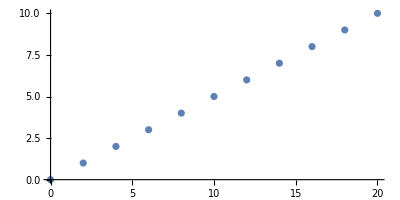

```mathematica
ComplexListPlot[Table[2x+(x*I),{x,0,10}]]
```

```mathematica
Plot[2x+(x),{x,0,10,1}]
```

Plot::pllim: Range specification {x,0,10,1} is not of the form {x, xmin, xmax}.

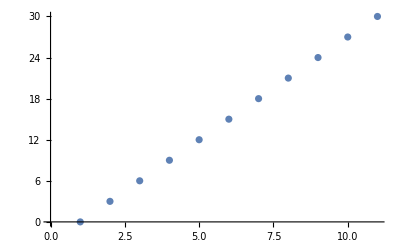

```mathematica
ListPlot[Table[2 x+x,{x,0,10,1}]]
```

```mathematica
?Plot
```

```mathematica
?PlotPoints
```